## Net surgery

In many cases, it is not necessary to build and train a network from scratch but it is possible to modify existing networks and re-train them to address the task we are interested in.

Here, I illustrate how to adapt a neural network originally designed to identify the main object in an image to classify photos from beaches and mountains.

### Get a pre-built model to identify the main object in an image

We will base the surgery on a model designed to identify the main object in an image. This ANN was trained on over 4,000 classes of objects. It is part of the back end for the ImageIdentify function in Wolfram Language 11.1. It was designed to achieve a good balance among classification accuracy, size and evaluation speed.

#### Model retrieval

```mathematica
NetModel["Wolfram ImageIdentify Net V1","Properties"]
```

{AllVersions,ByteCount,ConstructionNotebook,Description,Details,Documentation,DocumentationLink,DOI,DownloadedVersion,EvaluationNet,ExampleNotebook,ExampleNotebookObject,Hash,InputDomains,Keywords,LatestUpdate,Name,Originator,Properties,ReleaseDate,SeeAlso,ShortName,SourceMetadata,TaskType,TrainingSetData,TrainingSetInformation,UninitializedEvaluationNet,UUID,Version,VersionInformation,VersionsAvailable,WolframLanguageVersionRequired}

```mathematica
NetModel["Wolfram ImageIdentify Net V1","Description"]
```

Identify the main object in an image

We get the trained version of the model:

```mathematica
net=NetModel["Wolfram ImageIdentify Net V1"]
```

NetChain[<>]

Before proceeding further, let us explore the usage of the network and some features.

#### Basic usage of this model

Let us use the neural net on the image of a lion:

```mathematica
pred=net[-Graphics-]
```

lion

The prediction is an Entity object, which can be queried:

```mathematica
pred["Definition"]
```

large gregarious predatory feline of Africa and India having a tawny coat with a shaggy mane in the male

Get a list of available properties of the predicted Entity:

```mathematica
pred["Properties"]
```

{alternate names,broader concepts,definition,entity classes,equivalent entity,image,name,narrower concepts,similar entities,subset concepts,superset concepts,WordData senses,WordNet ID}

Obtain the probabilities of the ten most likely entities predicted by the net:

```mathematica
net[-Graphics-,{"TopProbabilities",10}]
```

{art→0.00016875,mountain lion→0.000180933,painting→0.000186271,Shetland sheepdog→0.000204208,wall clock→0.000257065,sky→0.000347166,liger→0.000349928,analog clock→0.000458668,chow chow→0.000709368,lion→0.995338}

Interestingly, besides lion, chow chow is the most likely. Did you realise how similar this dog is to a lion?

```mathematica
Entity["Concept","ChowChow::7x292"]["Image"]
```

-Graphics-

```mathematica
Entity["Concept","ChowChow::7x292"]["Definition"]
```

breed of medium-sized dogs with a thick coat and fluffy curled tails and distinctive blue-black tongues; believed to have originated in northern China

The classifier is very comprehensive. It classify to 4315 classes!

```mathematica
classesnet=EntityValue[NetExtract[net,"Output"][["Labels"]],"Name"]
```

{Azadi Tower,Colosseum,Eiffel Tower,Elizabeth Tower,Gateway Arch,Great Pyramid of Giza,Great Wall,Leaning Tower of Pisa,Lincoln Memorial,Machu Picchu,Monticello,Parthenon,Space Needle,Statue of Liberty,Stonehenge,Taj Mahal,The Pentagon,White House,Washington Monument,aardvark,common mullein,abacus,abaya,white poplar,abelia,okra,musk okra,black Angus,silver fir,Pacific silver fir,balsam fir,white fir,Fraser fir,grand fir,subalpine fir,desert sand verbena,absinth,sergeant major,velvetleaf,Abyssinian banana,earleaf acacia,silver wattle,sweet acacia,blackwood,golden wattle,fever tree,academic dress,wahoo,bear's breech,accelerator,Cooper's hawk,northern goshawk,Eurasian sparrowhawk,accordion,hedge maple,vine maple,Japanese maple,bigleaf maple,California box elder,Norway maple,sycamore maple,red maple,silver maple,sugar maple,death's-head hawkmoth,common yarrow,hot water plant,cheetah,beluga,Venus' chariot,acorn barnacle,acorn,acorn squash,acoustic guitar,common myna,sedge warbler,acropolis,red baneberry,luna moth,sea anemone,kiwi,wingstem,common sandpiper,spotted sandpiper,acuminate leaf,two-spotted ladybug,Adam's needle,baobab,adapter,addax,adderstongue,adélie penguin,red beadtree,desert-rose,great barracuda,common maidenhair,northern maidenhair,adjutant bird,admiral butterfly,yellow fever mosquito,Asian tiger mosquito,black mangrove,barbed goatgrass,cinereous vulture,impala,aerial photograph,cable tramway,aerides orchid,wind generator,spotted eagle ray,monkey dog,afghan,Afghan hound,Common chameleon,African clawed frog,Nile crocodile,African daisy,African bush elephant,African grey parrot,African wild dog,Africanized bee,African lily,African marigold,Nile monitor,African violet,agama,blue giant hyssop,kauri,American century plant,maguey,cantala,red-winged blackbird,bluemink,copperhead,cottonmouth,churchsteeples,ocellated turkey,common corncockle,cane toad,avocado,agueweed,tree of heaven,giant panda,red panda,air compressor,air conditioner,aircraft carrier,aircraft engine,hangar,Airedale terrier,airplane propeller,airport terminal,mandarin duck,pale-throated sloth,roseate spoonbill,blue bugle,pyramid bugle,common bugle,northern fur seal,brown bear,Alaskan malamute,skylark,silktree,raintree,bonefish,razorbill,hollyhock,common kingfisher,moose,alderfly,red-legged partridge,brush turkey,ground ivy,alfalfa,common bugloss,golden trumpet,lollipop,Allegheny plum,chinkapin,Allen wrench,garlic mustard,alligator clip,alligator lizard,American alligator,Chinese alligator,alligator snapping turtle,wild onion,nodding onion,wild chive,Chinese chive,bear garlic,angler fish,mountain bike,European alder,white alder,alpenstock,alpine ash,greater galangal,shellplant,German shepherd,ditabark,altarpiece,marsh mallow,altocumulus,altostratus,aluminium foil,madwort,tumbleweed,Prince-of-Wales feather,Amazon parrot,dogtooth violet,almaco jack,marine iguana,podium,cuman ragweed,ambulance,spotted salamander,axolotl,tiger salamander,pronghorn,white cedar,American basswood,American beech,American bison,American bittern,Carolina anole,American chestnut,American cockroach,American coot,American copper butterfly,cranberry,brown creeper,American crow,American dog tick,redosier dogwood,bald eagle,great egret,American elm,purple gallinule,gray birch,American holly,American kestrel,tamarack,mountain laurel,American lotus,American merganser,American pennyroyal,pit bull terrier,American sycamore,American red squirrel,American redstart,American robin,sweetgum,American toad,paper birch,white oak,eastern white pine,American widgeon,American wisteria,American woodcock,bowfin,ammeter,Barbary sheep,Amniota,desert false indigo,amorphophallus,amphibious aircraft,amphibian,orange clownfish,amphora,vial,cashew,green anaconda,scarlet pimpernel,analog clock,analog watch,analytical balance,pineapple,pineapple,pearly everlasting,northern pintail,squash bug,northern shoveler,green-winged teal,blue-winged teal,mallard,garganey,American black duck,ancient pine,Andean condor,cabbagebark tree,andiron,mining bee,big bluestem,little bluestem,anechoic chamber,anemometer,Canada anemone,rue anemone,wood anemone,wood anemone,snowdrop windflower,aneroid barometer,dill,angelfish,garden angelica,angelica,woodland angelica,angel shark,scarlet begonia,oriental vessel fern,earthworm,Angora goat,Angora rabbit,New Zealand longfin eel,slow worm,water turkey,Australian sword lily,porkfish,ankle brace,Asian longhorned beetle,greylag goose,swan goose,answering machine,spiny anteater,short-beaked echidna,antechamber,corn chamomile,stinking chamomile,roman chamomile,golden chamomile,polyphemus moth,wild chervil,flamingo flower,meadow pipit,common kidneyvetch,springbok,blackbuck,antiperspirant,garden snapdragon,tail rotor,antlion,pallid bat,anvil,apartment building,purple emperor,Guinea pig,surfbird,Aplysia punctata,spotted cardinalfish,Appenzeller,apple mint,apple turnover,apricot,apron,apse,emperor penguin,king penguin,kiwi,common swift,scuba,aquarium,aqueduct,tawny eagle,blue columbine,red columbine,European columbine,dromedary,Arabian coffee,spikenard,limpkin,limpkin,garden spider,barn spider,monkeypuzzle tree,bunya bunya,catapult,arboretum,strawberry tree,flying buttress,arch,ruby-throated hummingbird,architecture,archive,arch,southern sheeps head,galosh,Arctic ground squirrel,Iceland poppy,parasitic jaeger,binturong,Arctic wolf,greater burdock,guadalupe fur seal,great blue heron,great egret,greenland stitchwort,ruddy turnstone,black turnstone,arena theater,sugar palm,dragon's mouth,Mexican poppy,black and gold garden spider,greater argonaut,argyle,marguerite,orange tortrix,silversword,wheel bug,jack in the pulpit,neem,Virginia snakeroot,Arizona cypress,glossy snake,western kingbird,ark shell,armadillo,armguard,armoire,armored car,tank,armored personnel carrier,arm,army worm,mountain arnica,arnica,Swiss stone pine,tall oatgrass,arrival gate,arroz con pollo,silver sagebrush,common wormwood,art gallery,arthrogram,globe artichoke,elbow,knee,artificial horizon,breadfruit,jackfruit,art,cuckoo pint,water vole,largeflower heartleaf,virginia heartleaf,tailed frog,swamp milkweed,showy milkweed,butterfly milkweed,garbage can,ashtray,Asian crocodile,Asiatic black bear,oriental cockroach,pawpaw,long-eared owl,common asparagus fern,garden asparagus,sweetscented bedstraw,fire extinguisher,cast-iron plant,black spleenwort,walking fern,Hart's tonguefern,asp viper,Indian rubberplant,assault rifle,assembly line,bushy aster,asterism,New England aster,New York aster,prairie aster,dwarf astilbe,spiraea,greater masterwort,astrolabe,Central American spider monkey,little owl,athletic field,jockstrap,Atlantic bonito,bottlenose dolphin,Atlantic halibut,giant oceanic manta ray,Atlantic puffin,Atlantic ridley sea turtle,Atlantic white cedar,Atlas cedar,atlas moth,attack submarine,attic,auditorium,Audubon's warbler,auklet,trumpetfish,ear,otoscope,beach sheoak,Australian pitcher plant,Australian sea lion,Australian terrier,Australian turtledove,bus,autogyro,automat,ATM,automatic pistol,washing machine,io moth,automobile engine,field pumpkin,common oat,carambola,gray mangrove,white mangrove,avocet,awning,awning deck,axe head,axe,axle,crown vetch,lesser scaup,redhead,pochard,greater scaup,canvasback,azalea,chinaberry tree,babbler,baby's breath,bird's-foot trefoil,baby,baby blue eyes,baby grand piano,weeping willow,baby shoe,baby-walker,back brace,backgammon board,backhoe,backseat,bacon and eggs,BLT,bacteria,Bactrian camel,badlands,badminton racket,baggage claim,baguette,baked Alaska,baking sheet,balaclava,shoebill,common minke whale,blue whale,fin whale,balance beam,bulletwood,balcony,balcony,bald-faced hornet,sea hibiscus,queen triggerfish,rafter,tutu,ball gown,spiny puffer,Palmer's penstemon,balloon vine,ballpark,ballpoint pen,ballroom,balsam apple,balsampear,balsam poplar,balsamroot,Baltimore oriole,baluster,balusters,bamboo,banana,banana split,bandana,banded anteater,banded gecko,white admiral,common water snake,bandsaw,band-tailed pigeon,bangle,Indian banyan,banjo,bank bill,bank swallow,vault,bantam,baptismal font,bar,garden yellowrocket,Barbary ape,spareribs,barbecued wing,barbecue,barbecue,barbecue sauce,barbell,barber chair,Barberton daisy,barbet,bar chart,bar code,baritone horn,barking deer,mouse barley,barn,yellow star-thistle,barnacle goose,barn door,barn owl,barn swallow,barque,snoek,barred owl,barrel cactus,barrel vault,barrette,Barrow's goldeneye,bar soap,upland sandpiper,baseball,baseball bat,baseball cap,baseball glove,basement,basenji,basil,basilisk,basinet,backboard,basketball hoop,basketball,chestnut oak,purpleosier willow,basking shark,ringtail,bass clarinet,bass drum,basset hound,double bass,bass guitar,bassinet,bastion,swimming cap,bathtub,bathroom,batter's box,battery charger,batting cage,batting helmet,battle cruiser,battle dress,battlement,mountain ebony,baya weaver,sweet bay,bay leaf,bobcat,bayrumtree,laurel willow,bazaar,bazooka,dune buggy,beach chair,beach,beach pea,beach strawberry,station wagon,beaded lizard,sensitive fern,beagle,beaker,beam scale,beanie,bearded vulture,manzanita,bechamel sauce,southern crab apple,bedbug,bedroom,zonal geranium,Bedlington terrier,bedpan,bee eater,bee-fly,beefsteak geranium,beef Wellington,robber fly,bee orchid,beer keg,beer can,beer glass,beer mat,wax begonia,blackberry lily,tropical white morning-glory,bell jar,lawndaisy,currawong,belt buckle,belted kingfisher,common barberry,beret,berg,bergamot orange,elephant-ear,african woodsorrel,Easter lily,Bernese mountain dog,beetroot,yellow birch,water birch,river birch,European white birch,downy birch,Bewick's swan,gaur,bicycle chain,bicycle pump,bicycle rack,bicycle seat,bicycle wheel,crowned beggartick,sour orange,bighorn sheep,bikini,billboard,wallet,pool table,bing cherry,binoculars,biplane,birchbark canoe,birdbath,birdcage,locoto,germander speedwell,birdfoot violet,bird vetch,European bison,puff adder,Gaboon viper,sour orange,bitter root,great black-backed gull,blackberry,chalkboard,Blackburnian warbler,black-capped chickadee,black raspberry,black cherry,black-crowned night heron,blackeyed susan vine,black fly,black-footed ferret,black guillemot,mountain hemlock,black henbane,black kite,black sallee,black marlin,black medick,black-necked cobra,eared grebe,black-necked stilt,black-necked stork,black oak,black olive,black pepper,blackpoll,black rat,black rat snake,black rhinoceros,black spruce,black squirrel,black stork,black swan,blacktail deer,arizona black-tailed prairie dog,blacktip shark,black walnut,black widow,black willow,black-winged stilt,German cockroach,deer fern,blender,Blenheim spaniel,bletia,urn orchid,blimp,blindfold,block plane,bloodhound,bloodtwig dogwood,hair dryer,blucher,blue ash,blueback salmon,western fence lizard,blueberry,bluebird,salmon catfish,blue daisy,blue-eyed grass,blue butterfly,bluegill,blue gum,blue-headed vireo,coho salmon,bluejack oak,blue jay,blue marlin,blue orchid,blue peafowl,blue pea,blue poppy,blue shark,common viper's bugloss,bluethroat,blue tit,boa constrictor,bull thistle,boat-billed heron,boat deck,boatswain bird,bobby pin,bobsled,bobolink,bobsled,bocce ball,China grass,Bofors gun,buckbean,bog rein orchid,pestilence wort,marsh grass of parnassus,Bohemian waxwing,kettle,bolo tie,bolero,bolt cutter,red silk cottontree,kapoktree,bomber jacket,fire-bellied toad,cedar waxwing,ruffed grouse,bone marrow,castanets,bongo,shovelhead,bonobo,television,booby,bongo,bookcase,bookend,book jacket,bookmark,book,bookshelf,boom box,bootie,American beech,borage,common borage,toddy palm,Border collie,Border terrier,borsch,borzoi,yak,Boston terrier,Boston swordfern,Boston ivy,European bittern,fer-de-lance,peepul tree,bottlecap,bottle cork,bottled water,closed bottle gentian,bottle gourd,green bristlegrass,north atlantic bottle-nosed whale,corkscrew,bouncingbet,Bouvier des Flandres,Bowie knife,bowler hat,bowling alley,bowling ball,bowling shoe,bowsprit,bay window,box camera,box end wrench,boxer,boxers,boxing glove,boxing ring,post oak,boysenberry,braces,flame bottletree,broad-leaved bottletree,currajong,Swan River daisy,brachyuran,brain coral,brake disk,brambling,brandy snifter,brandy,bran muffin,common brant goose,Canada goose,brassavola,spider orchid,spider orchid,charlock mustard,rape,romanesco,brussels sprout,sprouting broccoli,pak choi,field mustard,brass knuckles,Brazilian rosewood,breadbasket,breadbox,bread dough,breadfruit,breathalyzer,Bren gun,purple mountainheath,brewery,briard,bricks and mortar,wedding dress,bridge,brig,brioche,bristle brush,bristlecone pine,bristly oxtongue,Brittany spaniel,brittle bladderfern,brittlebush,brittle-star,fava bean,broadbill,tenweeks stock,brook,broom,broom palm,cusk,paper mulberry,browallia,brown algae,brown bat,brown garden snail,Brown Swiss,brown thrasher,angel's trumpet,angel's trumpet,rusk,great horned owl,cattle egret,bufflehead,bucket seat,buckskin,buckthorn berry,butterflybush,budgerigar,takin,Missouri gourd,buffalo wing,buffet car,western toad,European toad,natterjack,bufo,Texas toad,Eurasian green toad,bug,buggy,bugle,built-in bed,bulbul,southern magnolia,bullet train,bullfinch,American bullfrog,bullhorn,bull mastiff,Bullock's oriole,ponderosa pine,bullring,bull shark,bumblebee,buckthorn bully,bumper car,bunchberry dogwood,bunk bed,bunker,bunting,thin-tailed burbot,Burchell's zebra,stone curlew,burial chamber,burial ground,burka,burlap bag,bur oak,machine pistol,elephant tree,gumbo limbo,bearskin,bushbaby,bushbuck,bush hibiscus,dwarf nasturtium,bushtit,business office,butcherbird,butcher's broom,buzzard,rough-legged hawk,red-shouldered hawk,sieva bean,butter churn,butter dish,butterflyfish,wing nut,buttermilk biscuit,butternut,butt hinge,button pink,button,fanny pack,cabbage palmetto,small white butterfly,caber,cabin,caboose,cabinet,cable car,cacao bean,sulphur-crested cockatoo,cactus wren,bird-of-paradise shrub,Caesar salad,muscovy duck,cairn terrier,strawberrytree,feather reed grass,lesser calamint,Calamus,marsh gentian,slipper flower,cauldron,hookah,pot marigold,red knot,curlew sandpiper,pectoral sandpiper,California laurel,California condor,hairy cat's ear,poison hemlock,California four o'clock,hummingbird trumpet,California Lady's slipper,California live oak,California newt,California poppy,California quail,California redbud,California sea lion,California sycamore,Coulter's matilija poppy,valley oak,whispering bells,water arum,stickpea,cinnabar moth,blue crab,golden tickseed,bluebottle,China aster,sapote,incense cedar,feathered pink,yellow marsh marigold,eastern sweetshrub,fairy slipper,calyx tube,small camas,camberwell beauty butterfly,camcorder,giraffe,truck,camisole,tussock bellflower,Dane's blood,canterbury bells,peachleaf bellflower,rampion bellflower,rampion,camp chair,bloodwoodtree,camper trailer,bivouac,camphor tree,spruce grouse,Canada lily,Canada lynx,common porcupine,Canada thistle,Canadian fleabane,Canadian goldenrod,eastern hemlock,red pine,golden shower,canal,ilang-ilang,tulip tree,atlantic rock crab,Dungeness crab,lyreleaf sage,candied apple,candy cane,candy corn,candytuft,wicker,golden jackal,dingo,gray wolf,red wolf,Christmas fern,canister,cannon,cannon ball,western red cedar,canopic jar,cantaloupe,cantaloupe,canteen,garden ginger,sail,canyon live oak,canyon treefrog,capacitor microphone,African buffalo,lion's tail,Peruvian groundcherry,cape jasmine,cape marigold,Cape May warbler,Madagascar periwinkle,western capercaillie,capybara,capitol,caper,ibex,head,carabao,carabiner,caracal,sticky bun,carancha,copernicia,crevalle jack,crucian carp,caravan,carbine,carburetor,carcass,sandbar shark,spotted sand tiger shark,oceanic whitetip shark,great white shark,crinkleroot,cuckoo flower,cardamom,cardcase,house of cards,cardigan,Cardigan Welsh corgi,northern cardinal,cardinal tetra,common cockle,linnet,european goldfinch,common redpoll,hoary redpoll,siskin,musk thistle,loggerhead turtle,cargo container,crested cariama,piranha,papaya,stemless carline thistle,carline thistle,carnauba wax palm,saguaro,carob tree,Carolina chickadee,evening trumpetflower,Carolina wren,carrousel,car park,carpenter ant,carpenter bee,carpenter's hammer,carpenter's kit,carpet moth,carpet snake,worm snake,European hornbeam,Hottentot fig,house finch,purple finch,carriage house,black vulture,car transporter,common plantain,caryatid,jaggery palm,casbah,case knife,cash register,great egret,cassava,Cassegrainian telescope,cassette recorder,cassette tape,cassia,cassia bark,Cassin's kingbird,cassowary,chinquapin,caster,desert paintbrush,giant red Indian paintbrush,castle,castorbean,catacomb,catalytic converter,catamaran,European wildcat,catboat,great skua,turkey vulture,cathode-ray oscilloscope,catnip,willet,CAT scanner,tomato ketchup,ketchup bottle,cattle pen,cattleya,Caucasian walnut,king mackerel,cavern,Guinea pig,cayenne pepper,C-clamp,CD drive,pygmy marmoset,white-headed capuchin,cecropia moth,cedar elm,cedar of Lebanon,deodar cedar,crybaby tree,celandine poppy,celery stick,cello,cellphone,crested cock's comb,European hackberry,cembalo,cement mixer,cenotaph,censer,dusty miller,garden cornflower,greater knapweed,red valerian,centrifugal pump,greater sage grouse,spurred butterfly pea,red helleborine,pigeon guillemot,horned viper,snow in summer,white rhinoceros,blue paloverde,eastern redbud,vervet monkey,cereal box,American elk,sika deer,night jessamine,rose chafer,chacma baboon,Maule's quince,chaetodon,chaffinch,chafing dish,chainsaw,chain,chair lift,chaise longue,chalice vine,challah,Port Orford cedar,Nautilus,red drum,greater roadrunner,San Luis purple sage,piping plover,Eurasian dotterel,killdeer,charge card,Charolais,chassis,dwarf checkerbloom,milk snake,chequered lily,checkout counter,cheddar pink,cheeseburger,wallflower,celandine,green sea turtle,common snapping turtle,chemise,white croaker,cherimoya,Siberian crab apple,cherry plum,chervil,Chesapeake Bay retriever,chesterfield,chestnut,chestnut,chicken coop,chicken sandwich,Douglas squirrel,chickpea,chick pea,chicory,chicory root,Kentucky coffee tree,Chihuahua,chili dog,desert willow,mantelpiece,china cabinet,chinchilla,jujube,Chinese hound's tongue,fried rice,Chinese lantern,Chinese parasol tree,coriander,Japanese pagoda tree,chinkapin oak,chin rest,chipmunk,chipping sparrow,french fries,chives,Frill-necked lizard,chocolate egg,chocolate kiss,chocolate truffle,cholla,Linnaeus's two-toed sloth,Hoffmann's two-toed sloth,chorus frog,chough,chow chow,Christmas cactus,poinsettia,Christmas stocking,Christ plant,chronograph,chrysalis,pyrethum daisy,crowndaisy,Tibetan terrier,oxeye daisy,max chrysanthemum,shasta daisy,Florist's daisy,feverfew,dusty miller,corndaisy,painted turtle,golden pheasant,Australasian snapper,chuckwalla,black-legged seriema,pew,church,cicada killer wasp,white stork,water hemlock,cigar band,cigar cutter,cigarette case,cigarette holder,cigarette lighter,dusty miller,common ragwort,cinnamon bark,cinnamon roll,cinquefoil,English walnut,Judas tree,circuit breaker,circuitry,marsh harrier,northern harrier,Montagu's harrier,cirrocumulus,cirrostratus,cirrus,field thistle,cottongrass,marsh wren,sedge wren,mantled ground squirrel,rock squirrel,citron,key lime,shaddock,bitter orange,grapefruit tree,sweet orange tree,long-tailed duck,clapperboard,Clark's nutcracker,clary sage,clary sage,classroom,spring beauty,clavichord,Virginia spring beauty,clayware,clean room,cleats,cleat,meat cleaver,horse-fly,scarlet leather flower,western blue virginsbower,clementine,desert pea,click beetle,cliff,American cliff swallow,crampoon,flame lily,wild basil,Atlantic pigeonwings,cloche hat,clock radio,flat cap,clothesbrush,clothes closet,clothes hanger,clothes pin,coat rack,cloud bank,carnation,club-head,clumber spaniel,Clydesdale horse,six-lined racerunner,spurge nettle,white-nosed coati,chiton,hazelnut,haw-finch,cockatiel,cockchafer,English cocker spaniel,cockpit,orchardgrass,cocktail shaker,coconut,coconut palm,longbract frog orchid,coffee bean,coil spring,coin,colander,northern flicker,red-shafted flicker,cold chisel,cold frame,stuffed tomato,common coleus,northern bobwhite,coliseum,tent,collar,collared peccary,college,springtail,collet chuck,collie dog,taro,Colorado potato beetle,blue spruce,rock dove,common wood pigeon,feather star,combination lock,combine,eastern comma,command key,dayflower,common,apricot,European bird cherry,long-finned pilot whale,Scotch broom,canary,common chickweed,common comfrey,tall cottongrass,common dandelion,ram's horn,short-beaked common dolphin,common duckweed,European ash,common European earwig,common evening primrose,marvel of Peru,purple foxglove,common garter snake,starch grape hyacinth,field horsetail,garden hyacinth,common iguana,common jasmine,common kingsnake,showy lady's slipper,garden lettuce,common lilac,common limpet,common lynx,common mallow,common milkwort,common mosquito,common murre,myrtle,common newt,English oak,Virginia opossum,basket willow,common plum,common privet,common raccoon,crimsoneyed rosemallow,common sage,black scoter,harbor seal,common gypsyweed,common spoonbill,common spotted orchid,elkhorn fern,European starling,sweet-amber,common sunflower,Fuller's teasel,garden valerian,common European viper,common wasp,flowering dogwood,suckling clover,common yellowthroat,communion table,community,compass,compound microscope,computer keyboard,computer monitor,computer mouse,elephant-ear tree,concertina wire,Concord grape,condensation trail,purple coneflower,holarrhena,Conestoga wagon,dixie rosemallow,conference center,conference room,American conger,conker,blue mistflower,console table,doubtful knight's-spur,container ship,western wood-pewee,control room,convertible,field bindweed,cooker,cookie cutter,cooking pan,cooling tower,heartleaf foamflower,coonskin cap,river cooter,European beech,European roller,coracle,mescal bean,trumpet honeysuckle,spotted coralroot,Spanish elm,cabbage tree,cork oak,snailflower,great cormorant,cornelian cherry,cornetfish,Stokes' aster,corn,corn poppy,corn snake,corn speedwell,corn stalk,correctional institution,corridor,bouquet,pampas grass,raven,rook,Eurasian jackdaw,fumewort,dobsonfly,coscoroba,cosmea,tea cozy,crib,feathered pink,cotton thistle,mountain lion,general store,coupe,courthouse,courtroom,courtyard,couscous,cowbell,cowbird,cowboy boot,cowboy hat,scrawled cowfish,hogweed,blackeyed pea,nutria,crabapple,false christmas cactus,crabeater seal,cradle,European cranberry bush,electric ray,cranberry,crane fly,smoky jungle frog,crepe myrtle,crash helmet,blackthorn,crayon,cream violet,credenza,creeping buttercup,creeping Jenny,creeping woodsorrel,creeping St. John's wort,creeping thyme,creme caramel,crenate leaf,croissant,crested penguin,crevasse,cricket ball,bat,crimson clover,potato chip,sanderling,crochet hook,saffron crocus,spotted hyena,dolmen,croquet ball,croquet mallet,croquette,red crossbill,crossbow,hot cross bun,cross of Lorraine,crossword puzzle,cross,eastern diamondback rattlesnake,western diamondback rattlesnake,horned rattlesnake,rock rattlesnake,speckled rattlesnake,Mojave rattlesnake,prairie rattlesnake,crouton,crown imperial,crow's nest,cruise ship,crutch,hellbender,Japanese cedar,submarine sandwich,cuckoo clock,common cuckoo,winter melon vine,net melon,cushaw pumpkin,crookneck squash,cue ball,cue,cuirass,cumulonimbus,cumulus,dhole,cupola,Monterey cypress,Italian cypress,cup,hair curler,curling iron,currant,cuttlefish,queen sago,Cyclamen hederifolium,cyclamen,quince,trumpeter swan,whistling swan,whooper swan,mute swan,cylinder,cymbidium,cardoon,spotted weakfish,umbrella plant,nutgrass,tiger cowrie,cypress spurge,cypress vine,moccasin flower,large yellow lady's slipper,mountain lady's slipper,hard shield fern,little grebe,dace,laughing kookaburra,rimu,dahlia,daikon,sundew,daishiki,eastern daisy fleabane,dallis grass,Dall sheep,fallow deer,topi,damask rose,dames rocket,damselfly,dam,monarch butterfly,dancing-lady orchid,Dandie Dinmont,yawl,February daphne,water flea,whole wheat bread,dark-eyed junco,dashboard,dashboard,data system,date,date palm,Queen Anne's lace,dawn redwood,mayfly,hearing aid,electric chair,deerhound,deer mouse,deer tick,house martin,royal poinciana,beluga,dendrobium,yellow-rumped warbler,yellow warbler,copperhead,dental plate,leatherback sea turtle,derrick,desert,desert iguana,desert sunflower,desert tortoise,pride-of-rochester,deviled egg,octopus,tiger lily,puncturevine,dhow,dial,dialog box,dial phone,diamondback terrapin,sweet William,China pink,maiden pink,diaper,walkingstick,Pacific giant salamander,Dutchman's breeches,bleeding heart,soft tree fern,digital clock,digital watch,dik-dik,dill pickle,dill,longan,dinette,dining room,dinner table,spotted porcupinefish,wandering albatross,venus flytrap,Dioon,Japanese persimmon,dipper,dirndl,disa,dish antenna,dish rack,dishwasher,disk clutch,floppy disk,distributor cap,royal fern,loon,diving suit,Doberman pinscher,dock,dog house,dogsled,houndstooth check,dog violet,doily,dolmas,domestic cat,dungeon,donut,door,doorknocker,door latch,door,door,dormer,livingstone daisy,double bed,double door,doublet,douglas-fir,dovekie,dovefoot geranium,dovetail joint,downy woodpecker,drafting table,dragee,trawler,dragonet,dragonfly,Komodo dragon,drawer,zebra mussel,dresser,dress hat,vanity,oil rig,drinking fountain,driving range,driving wheel,emu,poached egg,fruit fly,drumhead,eightpetal mountain-avens,dry fly,male fern,marginal wood fern,mountain fern,long beech fern,dry-stone wall,platypus,duffel bag,dugong,dulcimer,dumbbell,gray catbird,dump truck,dump,dumpster,dune,dunlin,dunnock,durian,durian,dusky salamander,garbage truck,dustpan,scarlet runner,white clover,Dutch elm,Dutch oven,Dutch oven,edible banana,mugo pine,moss phlox,dwarf tulip,dyer's greenweed,dyer's woad,imperial moth,earflap,earless lizard,early purple orchid,early spider orchid,earmuff,earplug,earplug,earring,outhouse,earthenware,earth,easel,stemless townsend daisy,Easter egg,eastern chimpanzee,eastern chipmunk,eastern coral snake,eastern cottontail,eastern cottonwood,eastern fence lizard,eastern fox squirrel,eastern gray squirrel,hophornbeam,eastern kingbird,eastern lowland gorilla,eastern meadowlark,eastern narrow-mouthed toad,eastern red-backed salamander,red spruce,restaurant,squirting cucumber,golden barrel cactus,sea urchin,sonogram,edelweiss,edible banana,blue mussel,escargot,eft,egg roll,eggs Benedict,egg,eggbeater,yolk,little blue heron,little egret,snowy egret,Egyptian vulture,water hyacinth,eider,eight ball,ejection seat,rainbow runner,swallow-tailed kite,white-tailed kite,rubber band,elbow pad,elderberry,electrical relay,switch,electric battery,electric drill,electric eel,electric fan,electric guitar,electric hammer,electric-light bulb,electric meter,electric organ,garbage disposal,electric range,electric razor,electric toothbrush,cardiograph,electronic balance,elephant seal,elevator,elevator car,elevator shaft,elf cup,Norwegian elkhound,umbrella-tree,linear leaf,yellowhammer,ortolan bunting,reed bunting,embroidery hoop,emerald creeper,grinding wheel,Emmental,emperor moth,enamelware,bread palm,Tampa butterfly orchid,butterfly orchid,engine room,English saddle,English elm,English lavender,English muffin,English primrose,English setter,house sparrow,English springer spaniel,English yew,sea otter,entablature,northern plains gray langur,entertainment center,envelope,envelope,epee,saddle-billed stork,fireweed,stream orchid,broadleaf helleborine,climbing cactus,Epipremnum aureum,equalizer,equatorial,scouringrush horsetail,Przewalski's horse,Grevy's zebra,Cape mountain zebra,winter aconite,burnweed,hawksbill turtle,briar root,spring heath,scotch heath,orange daisy,Philadelphia fleabane,west european hedgehog,loquat,European robin,Erlenmeyer flask,white-tailed sea eagle,least sandpiper,seaside eryngo,Tiger's claw,cork tree,patas monkey,fawn lily,yellow avalanche-lily,gray whale,secretary,Eskimo dog,northern pike,muskellunge,sainfoin,espresso maker,ethernet cable,peppermint gum,red gum,snow gum,mountain ash,sour cherry,Surinam cherry,western skink,Steller sea lion,bursting-heart,burning bush,common hoopoe,spotted Joe-Pye weed,common boneset,sweetscented joe pye weed,rusty blackbird,euphonium,wood spurge,snow on the mountain,Eurasian otter,European blackbird,European black currant,eurasian black grouse,whortleberry,brooklime,wels catfish,European curlew,field elm,European fire salamander,purple gallinule,European hare,European ladies' tresses,European magpie,European mountain ash,European nuthatch,stone pine,European olive tree,European perch,European quaking aspen,European rabbit,European raspberry,red elderberry,northern shrike,European spider crab,spur-thighed tortoise,European turkey oak,European white waterlily,European wolf spider,showy prairie gentian,assai palm,evening grosbeak,bladder campion,inkberry,pitcher,excavation,exercise bike,Exmoor,extension cord,eyeglasses,monocle,half mask,eyepatch,facade,factory,weeping beech,meadow saxifrage,fairway,fairy-bluebird,fairy light,merlin,gyrfalcon,eurasian hobby,eurasian kestrel,fall armyworm,panicled hydrangea,fall webworm,wingleaf soapberry,Santa Ynez goldenbanner,fan blade,turbojet engine,field pennycress,spigot,fawn,meadow false fleabane,feather ball,feather boa,fedora,nursing bottle,highchair,jungle cat,Pallas's cat,jaguar,ocelot,serval,margay,felucca,fencing mask,fennel,fen orchid,bamboo palm,ferret,Ferris wheel,ferrule,fescue,fez,strangler fig,fiddler crab,field,field artillery,fieldfare,field hockey ball,field lens,field pansy,field scabious,field sparrow,green field speedwell,blue fiestaflower,fig,green June beetle,figure skate,filament,file folder,filling station,filmy fern,finger,fingerprint,fire ant,fire beetle,fire bell,fireboat,dragon,fire truck,firehouse,fire pink,fire salamander,fire screen,hearth,firethorn,firing range,first-aid kit,fish and chips,osprey,Pallas's fish-eagle,fishing pole,flagon,flag,snowflake,flamingo,flaming poppy,flan,flash bulb,flat bench,flat-coated retriever,flathead,flathead,flathead catfish,flat-leaf parsley,flat panel display,flats,flax,flea beetle,flesh fly,fleur-de-lis,flight deck,Australian teak tree,wood stork,flip-flop,pontoon plane,floe,floor joist,floor lamp,Florida gallinule,goat willow,floss,flounder,flower garden,flowering hazel,flowering maple,petal,fluegelhorn,fluorescent lamp,flush toilet,flying boat,flying fox,fly orchid,flyswatter,sweet fennel,skunk cabbage,foil,food processor,football helmet,football stadium,footrest,forest tent caterpillar,forget-me-not,fork,forklift,formal garden,wood ant,Formica sanguinea,forsythia,fortified wine,witchalder,fountain,crimson fountaingrass,fountain pen,lingonberry,fragrant orchid,fragrant water lily,frame,bridal-wreath,hotdog bun,loblolly pine,horned puffin,white ash,Oregon ash,flowering ash,Texas ash,pumpkin ash,freewheel,freighter,French bulldog,French horn,French marigold,French toast,fried egg,frigate bird,Frisbee,frittata,frogfish,froghopper,frogmouth,front projector,living room,fuel gauge,fuji cherry,eurasian coot,northern fulmar,striped killifish,common gorse,tiger shark,brittlestem hempnettle,yellow spring bedstraw,common snipe,great snipe,common moorhen,suspender,bass viol,casino,mosquitofish,garage,common balm,rose campion,woodland forget-me-not,nasturtium,garden pea,garden rhubarb,long-nose gar,American pokeweed,Oregon white oak,gas gage,gasmask,gas meter,gas pump,gas ring,gavial,treasure-flower,gazebo,Thomson's gazelle,gazelle hound,gearset,paper clip,gemsbok,common genet,gentian,bottle gentian,yellow gentian,geodesic dome,geoduck,longleaf pine,spotted geranium,meadow geranium,Robert geranium,gerenuk,wild chamomile,German short-haired pointer,clog,prairie smoke,giant anteater,giant conch,giant granadilla,European Hornet,eastern grey kangaroo,giant salamander,giant schnauzer,giant sunflower,giant water bug,lar gibbon,gig,Gila monster,gingko,nurse shark,ginseng,gypsy moth,greenhouse,yellow hornpoppy,honey locust,GPS,common globe amaranth,pufferfish,globe thistle,glockenspiel,glove compartment,Canterbury bells,wildebeest,winged bean,goalpost,meadow salsify,gudgeon,goblet,go-kart,goldcrest,common tansy,bracted strawflower,golden hamster,golden oriole,golden plover,golden retriever,goldenseal,white willow,golf bag,golf ball,golfcart,golf course,golf glove,tee,golliwog,peanut,common merganser,buoy barnacle,European gooseberry,gopher tortoise,Gordon setter,gorget,western lowland gorilla,gosling,gouge,grab bar,hill myna,graduated cylinder,graffiti,grain,grandfather clock,grapefruit,European grass frog,grass skirt,grate,grater,gravestone,gray horse,gray fox,gray kingbird,gray partridge,grazing land,grease-gun,great crested grebe,Great Dane,greater kudu,greater prairie chicken,Greater Swiss Mountain dog,whitethroat,greater yellowlegs,great gray owl,Great Pyrenees,great St. John's wort,greenbottle fly,sweet corn,green fringed orchid,green frog,helmet orchid,European green lizard,green olive,green peafowl,green plover,green salad,greenshank,green snake,green woodpecker,torrey pine,griddle,griffon vulture,grinder,grindstone,grizzly bear,groats,groenendael,hovercraft,rare clubmoss,woodchuck,ground rattler,domestic pig,whooping crane,guacamole,guanabana,guanaco,guardrail,guava bush,guillotine,guinea hen,guitar pick,wolverine,gun turret,guppy,gym,western oakfern,Australian magpie,gyro,gyroscope,lesser purple fringed orchid,hemostat,hairbrush,hair slide,mountain silverbell,Stellar's sea eagle,green ormer,mallet,hammock,washbasin,handbell,pocket calculator,handcar,handcuff,hand-held computer,handlebar,handle-bar mustache,hand luggage,hand mirror,hand pump,hang glider,ivyleaf geranium,harmonica,harmonium,harness,harness,harpy eagle,harp,harp seal,short-toed eagle,hartebeest,stag,daddy longlegs,hasp,hatbox,hatchback,hatchback door,Hawaiian guitar,northern hawk owl,hawkweed,hay bale,hayfield,head gasket,foreland,hearse,heat sink,hedgehog cactus,hedge mustard,hedge trimmer,swamp sunflower,prairie sunflower,Jerusalem artichoke,oxeye,heliport,swordtail,skullcap,kamraj,rinkhals,yellow daylily,henbit deadnettle,herb garden,Hereford,looking-glass plant,opalescent sea slug,hermit crab,hermit thrush,herringbone pattern,herring gull,Texas purple spike,table mountain pine,high altar,highball glass,high bar,hill,lizard orchid,hipflask,barbados lily,hippopotamus,forest fly,hip pocket,convergent lady beetle,sable antelope,medicinal leech,tree martin,hoatzin,hoary marmot,hockey puck,hockey stick,odometer,hoe,hognose snake,lacebark,common velvetgrass,halibut,hollyleaved barberry,rock beauty,trepang,blessed milkthistle,American lobster,home plate,home theater,tea tortrix,Honduras mahogany,kinkajou,honey buzzard,honeycomb,honeydew,king protea,hooded merganser,wicket,hornbill,horned violet,horse barn,horseshoe,horseshoe,horseshoe crab,hospital,hospital bed,hospital room,hospital ship,hot-air balloon,hotel,hot line,hot plate,hot spring,stuffed tomato,hourglass,house,houseboat,house centipede,housefly,house mouse,house wren,howitzer,howler monkey,wax plant,hubcap,Hudsonian godwit,hula-hoop,foot,human skeleton,Humvee,Hungarian pointer,hunting knife,hurdle,hurricane,hurricane lamp,striped hyena,hybrid petunia,hortensia,hydrofoil,spring peeper,pacific treefrog,siamang,veery,wood thrush,common St. John's wort,hypodermic needle,night snake,hyssop,I-beam,wood ibis,Ibizan hound,polar bear,ice cream cone,popsicle,common iceplant,ice rink,ice shelf,ichneumon fly,yellow-breasted chat,orchard oriole,igloo,igneous rock,possumhaw,star anise,jewelweed,peacock butterfly,inchworm,sundial lupine,Indian cobra,Indian crocus,ghost plant,Indian python,Indian rhinoceros,Asian tapir,indigo bunting,indri,industrial park,inhaler,interceptor,interior live oak,involucre,red morning-glory,whiteedge morning-glory,tree swallow,dwarf crested iris,German iris,Irish setter,Irish terrier,Irish wolfhound,Japanese iris,dwarf violet iris,Spanish iris,ironwood,ironweed,isle,Italian greyhound,risotto,ivory gull,least bittern,castor bean tick,jabiru,jabuticaba,jabuticaba tree,jabot,jacamar,jack,African penguin,jack-in-the-box,jack mackerel,jack-o'-lantern,jack pine,cell,jackfruit,golden bellapple,Japanese apricot,Japanese banana,Japanese beech,Japanese beetle,Japanese black pine,japanese flowering cherry,Japanese honeysuckle,loquat,Japanese umbrella pine,Japanese wistaria,winter jasmine,Java sparrow,coffee,javelin,jawfish,jeep,Jeffrey pine,jelly bean,Jerusalem artichoke,Jerusalem cricket,jetliner,jeweler's loupe,jewelry dealer,jigsaw puzzle,rickshaw,joinery,wild radish,strap hinge,jonquil,Joshua tree,joystick,jug,juicer,jukebox,jumbo jet,jungle gym,juniper berry,juniper berry,junk,Jupiter,kaiser roll,pink cockatoo,oppositeleaf Russian thistle,kameez,koala,oceanic bonito,kayak,kazoo,kea,keeshond,kelpie,kepi,Kerry blue terrier,ketch,tympanum,keyhole,key lime,key thatch palm,khukuri,killer whale,kilt,kimono,king chess piece,King Charles spaniel,king cobra,kingfish,lion,king vulture,booth,kitchen garden,kitchen,kittiwake,kiwi fruit,knee brace,knee-high,knee pad,red-hot poker,double-pointed knitting needle,knot,sweet marjoram,kob,komondor,koto,kowhai,kudzu,kumquat,kurta,kuvasz,Labrador retriever,maze,lace,sand lizard,leaf lettuce,ladder-back chair,laelia,silver pine,pride of India,salt-water bream,white mangrove,lake,Lakeland terrier,lake salmon,alpaca,white deadnettle,porbeagle shark,lamppost,lamp shade,lancet window,landing net,lanyard,northern shrike,loggerhead shrike,laptop,northern largemouth bass,bigleaf periwinkle,large white butterfly,lasso,western larch,larkspur,mew gull,black-headed gull,laryngoscope,lasagna,laser printer,laser,latch,laundry cart,bathroom,broadleaved lavender,french lavender,lavender cotton,coastal tidytips,white leadtree,leaf-cutter bee,leaf-foot bug,leatherfish,lectern,lychee,boater,legless lizard,leg,lemon,lemon balm,lemon shark,ring-tailed lemur,lens cap,lentil,lenticular,mastic tree,Leonberg,common motherwort,northern leopard frog,leopard lizard,olive ridley sea turtle,silverfish,kiver,marabou stork,snowshoe hare,southern tamandua,fig buttercup,lesser whitethroat,lesser yellowlegs,leucocyte,lever tumbler,garden lovage,Lhasa,mountain pine,library,library,library,rosy boa,lido deck,liger,surge protector,lightning,lightship,whipping cream,mountain lily,pine lily,martagon lily,leopard lily,Turk's cap lily,viceroy,red-spotted purple,white admiral butterfly,short-billed dowitcher,limousine,Linotype machine,lionfish,lip,false twayblade,lipstick,liqueur glass,eggleaf twayblade,lychee,Japanese oak,San Francisco woodland star,litter basket,comb shell,liver chestnut,liverleaf,cabbage tree,lizardfish,loach,dock,lobster pot,sweet alyssum,lock chamber,locker room,locket,locomotive engine,migratory locust,lodgepole pine,loggia,logo,African daisy,London planetree,longbow,upright prairie coneflower,longhorn,vaulting horse,long johns,long sleeve,yellow honeysuckle,European honeysuckle,sustaining pedal,lounge suit,lovage,lovebird,love seat,lingonberry,long play record,loofah,Luger,luggage rack,tufted puffin,Texas bluebonnet,Texas bluebonnet,thrush nightingale,lute,schoolmaster,northern river otter,maltese cross,ragged robin,red catchfly,Carolina desert-thorn,groundcedar,lyrebird,skunk cabbage,purple loosestrife,rhesus monkey,macadamia nut,macaw,machete,rose bug,macrozamia,seventeen-year locust,star magnolia,sweetbay,cascade barberry,false lily of the valley,Canada mayflower,Malcolm stock,malinois,wild crapemyrtle,Maltese,southern crab apple,paradise apple,European crab apple,musk mallow,globe cactus,manakin,antillean manatee,mandola,arbor,mandrill,mango tree,mangle,mango,mangosteen,red mangrove,manhole cover,mantilla,praying mantis,mobile home,hand,weka,map,maraca,marble,marimba,marjoram,marker,market square,Eastern poison ivy,sea lavender,European waterclover,pine marten,mascara,masdevallia,mason bee,mason wasp,mason wasp,massasauga rattler,mast,black pine,match,matchstick,mathematical notation,sledgehammer,song thrush,mayapple,maypole,purple passionflower,tall buttercup,introduced sage,meadow froghopper,mealie,measuring cup,meat counter,meat grinder,meat thermometer,player piano,poppy,medicine ball,medina,medlar,medlar,medlar tree,megaphone,red-headed woodpecker,swamp sparrow,song sparrow,sloth bear,Menorah,Hanukkah menorah,water mint,peppermint,pennyroyal,spearmint,striped skunk,Mercury,smew,red-breasted merganser,Virginia bluebell,metamorphic rock,metronome,Mexican hat,Mexican sunflower,micrometer,smallmouth bass,midge,garden mignonette,mihrab,milk can,millipede,millet,millstone,millstone,mill wheel,tomatillo,northern mockingbird,mincer,miniature pinscher,miniature poodle,miniature schnauzer,miniskirt,minnow,mint,mint,miro,mistle thrush,bigfruit evening primrose,mitten,mixer,Ford Model T,bluntleaf sandwort,sandwort,pepper tree,spiny lizard,motmot,scarlet beebalm,wild bergamot,spotted beebalm,mongoose,unicycle,tarovine,Monterey pine,water minerslettuce,moorhen,mop,moray,Morgan,morning coat,mortarboard,mortar,white mulberry,mosque,mosquito net,moss campion,mother-of-pearl cloud,moth mullein,motorcycle,motor scooter,moufflon,mount,mountain goat,mourningbride,mourning dove,mousetrap,moussaka,mouth,cinema,wave,mud dauber,splash guard,mudskipper,mug,mulberry,mulch,pestle,mulloway,Murphy bed,plantain tree,tassel grape hyacinth,spotted flycatcher,scissortail,museum,mushroom coral,mushroom,music box,musical notation,music stand,muskox,musk rose,musk turtle,muskbeaver,smoothhound shark,muzzle,soft-shell clam,rockfish,nutmeg tree,anise,naan,nacho,nail polish,nail,lesser rhea,nanny-goat,jonquil,proboscis monkey,Nasturtium,viperine grass snake,navel orange,nebule,neckerchief,necklace,necklet,nectar,nectarine,fivespot,rambutan tree,Norway lobster,Neptune,nerita,oleander,Newfoundland dog,Newtonian telescope,goldfinch,love-in-a-mist,night-blooming cereus,night-blooming cereus,nightgown,night-light,night lizard,nimbostratus,nimbus,nipple,niqab,Quonset hut,nopal,Norfolk terrier,noria,northern parula,pitch pine,northern red oak,Norway spruce,Norwich terrier,noseband,tiger snake,eastern newt,North Island takahē,nougat,nut and bolt,nyala,yellow-crowned night-heron,pygmy slow loris,blackgum,oast,oast house,obelisk,objective lens,observatory,ocarina,ocean,eye,white-tailed deer,odontoglossum,narrowleaf evening primrose,office building,ohmmeter,oil filter,oil refinery,okapi,okra,Old English sheepdog,hop hornbeam,Old World scops owl,great white pelican,nose,olive,butterfly orchid,Chinook salmon,onion dome,openbill stork,operating table,rough green snake,smooth green snake,fly orchid,opium poppy,Texas prickly pear,orangutan,orange peel,grove,butterfly orchid,organdy,organization chart,Oriental arborvitae,Japanese bush cherry,Oriental poppy,Oriental spruce,tailorbird,oscillograph,monstrance,eastern screech-owl,outrigger,side mirror,ovenbird,overhead projector,owlet,violet woodsorrel,oxcart,oximeter,oxlip,sourwood,oxygen mask,ruddy duck,taipan,oyster catcher,patchouli,Pacific bottlenose dolphin,western hemlock,pack,packing box,paddlefish,paddle wheel,paddymelon,padlock,peony,paintball gun,paintbrush,painted beauty,painting,pair of pincers,pair of pliers,scissors,paisley,picket fence,pallasite,palomino,Panama tree,panpipe,pangolin,panicle,switchgrass,red spider,pansy orchid,pan,leopard,tiger,snow leopard,panty,buttery,panty girdle,pantyhose,dwarf poppy,long pricklyhead poppy,pawpaw,papaya,paper chain,paper towel,Continental Toy spaniel,red king crab,parasol,parking meter,parrotfish,parsley,tufted titmouse,tree sparrow,fetid passionflower,patch pocket,path,patio,cruiser,swampmallow,pay-phone,peace lily,peach,peach tree,peacock,peahen,peanut,common pear,pecan,sharp-tailed grouse,pedometer,peeler,peg,Pekinese,sweet scented geranium,American white pelican,valance,Pembroke Welsh corgi,pencil,pencil sharpener,penny arcade,pennywhistle,yellow perch,perch,potto,persimmon,person,pestle,Petri dish,sea lamprey,nun's-hood orchid,red phalarope,ring-necked pheasant,amur corktree,sweet mock orange,philodendron,lampwick plant,eastern phoebe,telephone cord,telephone jack,phonograph needle,Texas horned lizard,wood warbler,tomatillo,keyboard,piazza,white spruce,Sitka spruce,pickerel frog,pickup,picnic area,picture frame,pie chart,pied-billed grebe,pieta,pine nut,pigs in blankets,pile driver,pill bug,pillory,pilothouse,pinata,pinball machine,pin cherry,pineapple guava,pine siskin,pine grosbeak,table tennis ball,table tennis paddle,table tennis table,pinnule,painted mackerel,pinto,whitebark pine,spruce pine,singleleaf pinyon,western white pine,black pine,pond pine,scots pine,pinwheel,pipe cutter,pipe organ,common pipistrelle,western tanager,scarlet tanager,summer tanager,pistachio nut,water lettuce,piston,piston rod,pitahaya,pita,pitcher's mound,pith helmet,Pitta bird,pine snake,pizza,plane seat,planetarium,plaster bandage,plastron,southern platyfish,roble,playground slide,stone fly,plectranthus,snow bunting,plaice-fluke,plot,plow,plughole,plumb bob,leadwort,plunger,plush toy,Pluto,pluviometer,pocket knife,pocket watch,red-necked grebe,zebra finch,pogonia,poison sumac,tuberose,buffer,pollock,tadpole,elatior hybrid primroses,bluefish,pomegranate,pomegranate tree,pomelo,Pomeranian,pommel horse,pompadour,poncho,pontoon,vesper sparrow,poolroom,poop deck,popcorn,popover,black cottonwood,porcelain,portcullis,Portuguese man o'war,rose moss,spotted crake,water oak,potato salad,potato worm,potentiometer,Pothos,potter's wheel,potty seat,pouffe,powder horn,power cord,powerhouse,swift fox,pressure cooker,prickly pear,cowslip primrose,Primus stove,rock hyrax,purple martin,projector,protractor,Carolina cherry laurel,Japanese flowering cherry,flowering almond,red-bellied turtle,pond slider,Peruvian guava,ring-necked parakeet,satin bowerbird,puffbird,pug,pulsar,pumpkin seed,punching bag,red clover,common grackle,purple mountain saxifrage,purse,green,vermillion flycatcher,wild lily of the valley,desert cardinal,reticulated python,rock python,QR code,quadcopter drone,queen croaker,Southern red oak,shingle oak,pin oak,swamp chestnut oak,pin oak,live oak,quesadilla,quill pen,quince,quiver,racecourse,racquetball,radar dome,grille,radiator,bamboo palm,raft,rail,railroad,railroad tunnel,rainbow lorikeet,rain forest,rake,rambotan,wood frog,range hood,woodland caribou,white water crowfoot,cultivated radish,steenbok,raspberry,green prairie coneflower,taillight,rearview mirror,reception desk,reception room,jigsaw,lounger,recreation room,recycling bin,red admiral butterfly,redbone,red-breasted nuthatch,red-breasted sapsucker,red currant,Red Delicious,red-eyed vireo,red junglefowl,Mars,redshank common,redstart,red wine,reef,reef whitetip shark,film reel,reel,refractometer,ruby-crowned kinglet,remote control,community,resistor,retractor,revolving door,red-berry,greater rhea,whale shark,rhinoceros beetle,Rhode Island red,Rhodesian ridgeback,rosebay,swamp azalea,staghorn sumac,riband,ribbed vault,ribbon snake,ridge,ridge rope,riding mower,binder,ring ouzel,ringlet butterfly,ring-necked snake,river,rivet,rivulus,road,steamroller,roan,black locust,striped bass,rock,rock wallaby,vedalia,roller blind,roller skate,rolling pin,crucifix,rose apple,rosebud,rose hip,rosemary,rosette,rosemary,Rottweiler,rough-skinned newt,roulette wheel,rove beetle,rowanberry,Florida royal palm,cabbage palm,thimbleberry,blackeyed susan,rugby ball,ruin,rule,rumble seat,garden sorrel,runway,chamois,Andean cock-of-the-rock,Guianan cock-of-the-rock,saber,sacred ibis,safe,hard hat,safety pin,safety razor,saffron,secretary bird,sail,common squirrel monkey,Saint Bernard,bridalwreath spirea,salade,pussy willow,rainbow trout,saloon,rock wren,salsa,salt shaker,brook trout,American lake char,clary sage,wild clary,samisen,samosa,samovar,Samoyed,sandbag,sand bar,sandbox,sand cat,sand dollar,sand trap,sanitary landfill,viper's bowstring hemp,sarcophagus,Tasmanian devil,sarong,window lock,sassafras tree,satchel,satellite television,Saturn,saucepot,sauerkraut,dachshund,Sauvignon grape,savoy cabbage,saw,saw palmetto,saxhorn,whinchat,stonechat,yellow mountain saxifrage,starry saxifrage,saxophone,scaffolding,scallop shell,scalpel,scarab,sling,schipperke,school,sea-onion,red squirrel,altantic chub mackerel,sconce,sconce,scoreboard,scorpion,scorpion fly,Scotch egg,Scottish terrier,scouring pad,scrambled eggs,screech owl,desktop,screw,nodding lady's tresses,screw propeller,scrub brush,scrub-bird,scrubs,scull,coast,crawfish,sea fan,sea feather,seahorse,sea pen,harbor,searchlight,seashell,sea snake,sea squirt,sea star,common tern,sea trout,cereal rye,sectional,sedimentary rock,seeder,Segway,ovenbird,butterweed,sentry box,serin,yellowtail,kingfish,servo,settee,settee,shackle,Sharpie,shaving brush,shaving cream,shawl,sheath knife,shed,sheepskin coat,shelduck,shelf bracket,Shetland pony,Shetland sheepdog,Shih-Tzu,shin guard,shire horse,shoebox,shoehorn,shoe,shofar,shoji,store,shopfront,shopping cart,shopping center,Durham,jigger,shotgun shell,shoulder holster,shoulder patch,shovel,shower cap,shower curtain,shower,shredder,shrimp cocktail,shuttlecock,Siberian husky,side-blotched lizard,sidecar,side drum,sticky catchfly,maidenstears,silk,silkworm,silky terrier,compassplant,silver lime,blackcap,single-breasted jacket,single-breasted suit,undershirt,sitar,white-breasted nuthatch,skateboard,skein,ski binding,ski boot,ski mask,skimmer,ski pole,skirt,ski slope,sky,skyscraper,sleeping bag,slender salamander,meerkat,slide rule,sloe,Sloppy Joe,slug,slum,small white butterfly,smocking,fire alarm,snap pea,snood,snook,snorkel,snowbell,snow blower,snowboard,snow chain,snowdrift,snowfield,snow goose,snowmobile,snowplow,snowshoe,snuffbox,soap dish,soap dispenser,sobralia,soccer ball,soda can,soft-coated wheaten terrier,soft drink,soft pretzel,solan goose,jasmine nightshade,solar panel,solar collector,soldering iron,soldierfish,sombrero,common sowthistle,checkertree,sorrel,sorus,soybean,space capsule,space station,spaceship,space shuttle,spacesuit,spaghetti and meatballs,spaghetti,spaghetti squash,Spam,spark plug,spatula,tuatara,sphygmomanometer,yellow-bellied sapsucker,spice rack,spider web,spin dryer,spinning wheel,American tree sparrow,Spork,sport utility vehicle,spotted owl,spray gun,sprinkler,sprocket,sputnik,squash racket,common beargrass,marsh hedgenettle,Staffordshire bull terrier,stag beetle,stage,stagecoach,staghorn coral,stained-glass window,stair,staircase,stall,standard poodle,standard schnauzer,manual transmission,stanhopea,staple gun,stapler,star anise,star fruit,statue,steak knife,stealth bomber,stealth fighter,steamer,steam iron,steam room,steel drum,steering wheel,Wilson's phalarope,stegosaur,stele,leach orchid,sternwheeler,stevia,stick cinnamon,stinging nettle,stirrup,stoop,stonefish,stopwatch,storage warehouse,storm cloud,stovepipe,straitjacket,straight razor,stratocumulus,stratus,strawberry,strawflower,streamer fly,streetcar,street lamp,European turtle dove,tawny owl,ostrich,gray hairstreak,hostel,stuffed peppers,stupa,western meadowlark,substation,subway station,subway train,subwoofer,sulfur butterfly,sulky,sun,sundial,sunflower seed,supermarket,supernova,suricate,acerola,sushi,Sussex spaniel,swallow shrike,sweet woodruff,swizzle stick,synagogue,synthesizer,Tabasco sauce,table lamp,table saw,tacheometer,tailpipe,tamale,tamarind,tamarind,tambourine,gong,tangerine,tangerine,tankard,tank car,tank top,tape measure,tavern,tarantula,silver tree,tautog,cab,tea,tea bag,tea bag,tea cart,teapot,tea-strainer,tea urn,teak,atlas,telegraph key,telescopic sight,television antenna,telferage,waratah,waratah,temple,tench,tennis ball,tennis racket,Western box turtle,Tesla coil,testudo,leash,tetra,text,theremin,thermos,yellow oleander,thick-billed murre,thimble,thong,thong,thornbill,three-piece suit,yellowfin tuna,atlantic bluefin tuna,thyme,tiara,Tibetan mastiff,tiger beetle,tile roof,forest,tinamou,tiramisu,titi monkey,toaster oven,toaster,tobacco hornworm,toe,toll plaza,tomahawk,toolbox,toothpick,topiary,tornado,torpedo,tortoiseshell butterfly,totem pole,touraco,tugboat,tow truck,tower,toy poodle,toy,permit,horse mackerel,trackball,tractor,tragopan,yellow salsify,salsify,trampoline,transom,treadmill,tree frog,treehopper,tree house,tree kangaroo,tree lizard,trench coat,triceratops,tricycle,bird clover,trilobite,trimaran,triskele,winter wren,tropical pitcher plant,trowel,trundle bed,true bug,Didier's tulip,tumbleweed,tuning fork,redwing,tureen,turmeric,turnstile,turntable,coltsfoot,twist bit,wayfaringtree,pinto violet,tyrannosaur,tangelo,ukulele,wych elm,umbrella,uneven bars,upright piano,Uranus,largeflower bellwort,vacuum cleaner,valley,van,medlar,vanilla bean,vanilla,videocassette recorder,velvet ant,Venetian blind,Venn diagram,ventilator,Venus,Venus' slipper,gallery,vervain,blue water speedwell,vertical tail,yellowjacket,vibraphone,vicugna,videocassette,vine snake,viola,virus,yolk,fox grape,muscadine,crater,volleyball net,volleyball,red fox,kit fox,waffle iron,wagon wheel,wagtail,waiting area,Walkman,wall clock,wand,warthog,wasps' nest,watch cap,water bottle,falls,watermelon,water meter,water mill,water moccasin,water thrush,water tower,wattmeter,wax bean,weapons carrier,weigela,Weimaraner,doormat,Welsh springer spaniel,welwitschia,West Highland white terrier,wetland,wet suit,wheatear,whelk,whippet,whisk,whistle,white-crowned sparrow,white-throated sparrow,white wine,desert zinnia,wigwam,wild boar,wild cherry,Wilson's warbler,windmill,window box,window seat,windshield,windshield wiper,Windsor chair,wind turbine,wine cooler,wine cellar,wing chair,wire cutter,wolffish,Wollemi pine,wombat,wood chisel,wood-creeper,wood drake,wooden shoe,woofer,tiger moth,work-shirt,wort,wren warbler,wrestling ring,wringer,wristwatch,wryneck,rock wren,Xerox machine,yagi,yam,yam,yard,yarmulke,yellow squash,Yorkshire pudding,Yorkshire terrier,banana yucca,soapweed yucca,moundlily yucca,Zamboni,zebu,ziggurat,zoot suit,Grampa Simpson,Adam Warlock,Barbie,Bart Simpson,Batman,Beavis,Bob the Builder,Bugs Bunny,Butt-Head,Buzz Lightyear,Charlie Brown,Chewbacca,Cookie Monster,Darth Vader,Donald Duck,Doomsday,Dora the Explorer,Garfield,Goofy,Hal Jordan,Hello Kitty,Hobbes,Homer Simpson,Iron Man,Mario,Marge Simpson,Mickey Mouse,Minnie Mouse,Optimus Prime,Pac-Man,Ash's Pikachu,R2-D2,Santa Claus,Snoopy,Spider-Man,SpongeBob SquarePants,Stewie Griffin,Superman,Flash,The Grinch,Hulk,Pink Panther,Tweety,Wile E. Coyote,Winnie-the-Pooh,Wonder Woman,Yoda}

```mathematica
classesnet//Length
```

4315

To see the list of classes, we extracted the Output layer of the network which is a “class” decoder (expected since we are dealing with classification). In particular, we looked at the list of classes which are entities (we looked at the name of the entities).

```mathematica
NetExtract[net,"Output"]
```

NetDecoder[<>]

#### Exploring the interior of the network

```mathematica
net
```

NetChain[<>]

```mathematica
BatchNormalizationLayer
```

Obtain the total number of parameters (many!):

```mathematica
Information[net,"ArraysTotalElementCount"]
```

14713147

Obtain the layer type counts:

```mathematica
Information[net,"LayerTypeCounts"]
```

<|ConvolutionLayer→69,BatchNormalizationLayer→69,ElementwiseLayer→69,PoolingLayer→13,CatenateLayer→10,LinearLayer→1,SoftmaxLayer→1|>

Display the summary graphic:

```mathematica
Information[net,"SummaryGraphic"]
```

-Graphics-

Or the full summary graph:

```mathematica
Information[net,"FullSummaryGraphic"]
```

-Graphics-

The summary graph is good but the network topology (layout of layers and edges) can be better visualised with the “LayersGraph” property.

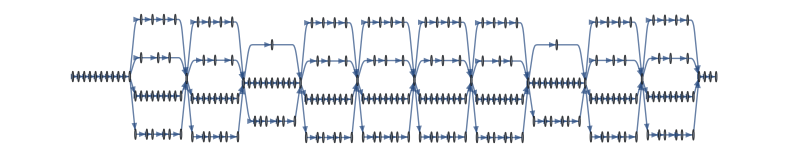

```mathematica
Information[net,"LayersGraph"]
```

How many layers of each type?

```mathematica
Information[net,"LayerTypeCounts"]
```

<|ConvolutionLayer→69,BatchNormalizationLayer→69,ElementwiseLayer→69,PoolingLayer→13,CatenateLayer→10,LinearLayer→1,SoftmaxLayer→1|>

```mathematica
Information[net,"Properties"]
```

{Arrays,ArraysByteCounts,ArraysCount,ArraysDimensions,ArraysElementCounts,ArraysLearningRateMultipliers,ArraysList,ArraysPositionList,ArraysSizes,ArraysTotalByteCount,ArraysTotalElementCount,ArraysTotalSize,FullSummaryGraphic,InputForm,InputPortNames,InputPorts,Layers,LayersCount,LayersGraph,LayersList,LayerTypeCounts,MXNetNodeGraph,MXNetNodeGraphPlot,OutputPortNames,OutputPorts,Properties,RecurrentStatesCount,RecurrentStatesPositionList,SharedArraysCount,SummaryGraphic,TopologyHash}

Do you really want to list all the layers?

```mathematica
layersnet=Information[net,"Layers"]
```

<|{conv_1}→ConvolutionLayer[<>],{bn_1}→BatchNormalizationLayer[<>],{relu_1}→ElementwiseLayer[<>],{pool_1}→PoolingLayer[<>],{conv_2_red}→ConvolutionLayer[<>],{bn_2_red}→BatchNormalizationLayer[<>],{relu_2_red}→ElementwiseLayer[<>],{conv_2}→ConvolutionLayer[<>],{bn_2}→BatchNormalizationLayer[<>],{relu_2}→ElementwiseLayer[<>],{pool_2}→PoolingLayer[<>],{3a,conv1x1}→ConvolutionLayer[<>],{3a,bn1x1}→BatchNormalizationLayer[<>],{3a,relu1x1}→ElementwiseLayer[<>],{3a,conv3x3_reduce}→ConvolutionLayer[<>],{3a,bn3x3_reduce}→BatchNormalizationLayer[<>],{3a,relu3x3_reduce}→ElementwiseLayer[<>],{3a,conv3x3}→ConvolutionLayer[<>],{3a,bn3x3}→BatchNormalizationLayer[<>],{3a,relu3x3}→ElementwiseLayer[<>],{3a,convdouble_3x3_reduce}→ConvolutionLayer[<>],{3a,bndouble_3x3_reduce}→BatchNormalizationLayer[<>],{3a,reludouble_3x3_reduce}→ElementwiseLayer[<>],{3a,convdouble_3x3_0}→ConvolutionLayer[<>],{3a,bndouble_3x3_0}→BatchNormalizationLayer[<>],{3a,reludouble_3x3_0}→ElementwiseLayer[<>],{3a,convdouble_3x3_1}→ConvolutionLayer[<>],{3a,bndouble_3x3_1}→BatchNormalizationLayer[<>],{3a,reludouble_3x3_1}→ElementwiseLayer[<>],{3a,avg_poolpool}→PoolingLayer[<>],{3a,convproj}→ConvolutionLayer[<>],{3a,bnproj}→BatchNormalizationLayer[<>],{3a,reluproj}→ElementwiseLayer[<>],{3a,ch_concatchconcat}→CatenateLayer[<>],{3b,conv1x1}→ConvolutionLayer[<>],{3b,bn1x1}→BatchNormalizationLayer[<>],{3b,relu1x1}→ElementwiseLayer[<>],{3b,conv3x3_reduce}→ConvolutionLayer[<>],{3b,bn3x3_reduce}→BatchNormalizationLayer[<>],{3b,relu3x3_reduce}→ElementwiseLayer[<>],{3b,conv3x3}→ConvolutionLayer[<>],{3b,bn3x3}→BatchNormalizationLayer[<>],{3b,relu3x3}→ElementwiseLayer[<>],{3b,convdouble_3x3_reduce}→ConvolutionLayer[<>],{3b,bndouble_3x3_reduce}→BatchNormalizationLayer[<>],{3b,reludouble_3x3_reduce}→ElementwiseLayer[<>],{3b,convdouble_3x3_0}→ConvolutionLayer[<>],{3b,bndouble_3x3_0}→BatchNormalizationLayer[<>],{3b,reludouble_3x3_0}→ElementwiseLayer[<>],{3b,convdouble_3x3_1}→ConvolutionLayer[<>],{3b,bndouble_3x3_1}→BatchNormalizationLayer[<>],{3b,reludouble_3x3_1}→ElementwiseLayer[<>],{3b,avg_poolpool}→PoolingLayer[<>],{3b,convproj}→ConvolutionLayer[<>],{3b,bnproj}→BatchNormalizationLayer[<>],{3b,reluproj}→ElementwiseLayer[<>],{3b,ch_concatchconcat}→CatenateLayer[<>],{3c,conv3x3_reduce}→ConvolutionLayer[<>],{3c,bn3x3_reduce}→BatchNormalizationLayer[<>],{3c,relu3x3_reduce}→ElementwiseLayer[<>],{3c,conv3x3}→ConvolutionLayer[<>],{3c,bn3x3}→BatchNormalizationLayer[<>],{3c,relu3x3}→ElementwiseLayer[<>],{3c,convdouble_3x3_reduce}→ConvolutionLayer[<>],{3c,bndouble_3x3_reduce}→BatchNormalizationLayer[<>],{3c,reludouble_3x3_reduce}→ElementwiseLayer[<>],{3c,convdouble_3x3_0}→ConvolutionLayer[<>],{3c,bndouble_3x3_0}→BatchNormalizationLayer[<>],{3c,reludouble_3x3_0}→ElementwiseLayer[<>],{3c,convdouble_3x3_1}→ConvolutionLayer[<>],{3c,bndouble_3x3_1}→BatchNormalizationLayer[<>],{3c,reludouble_3x3_1}→ElementwiseLayer[<>],{3c,max_poolpool}→PoolingLayer[<>],{3c,ch_concatchconcat}→CatenateLayer[<>],{4a,conv1x1}→ConvolutionLayer[<>],{4a,bn1x1}→BatchNormalizationLayer[<>],{4a,relu1x1}→ElementwiseLayer[<>],{4a,conv3x3_reduce}→ConvolutionLayer[<>],{4a,bn3x3_reduce}→BatchNormalizationLayer[<>],{4a,relu3x3_reduce}→ElementwiseLayer[<>],{4a,conv3x3}→ConvolutionLayer[<>],{4a,bn3x3}→BatchNormalizationLayer[<>],{4a,relu3x3}→ElementwiseLayer[<>],{4a,convdouble_3x3_reduce}→ConvolutionLayer[<>],{4a,bndouble_3x3_reduce}→BatchNormalizationLayer[<>],{4a,reludouble_3x3_reduce}→ElementwiseLayer[<>],{4a,convdouble_3x3_0}→ConvolutionLayer[<>],{4a,bndouble_3x3_0}→BatchNormalizationLayer[<>],{4a,reludouble_3x3_0}→ElementwiseLayer[<>],{4a,convdouble_3x3_1}→ConvolutionLayer[<>],{4a,bndouble_3x3_1}→BatchNormalizationLayer[<>],{4a,reludouble_3x3_1}→ElementwiseLayer[<>],{4a,avg_poolpool}→PoolingLayer[<>],{4a,convproj}→ConvolutionLayer[<>],{4a,bnproj}→BatchNormalizationLayer[<>],{4a,reluproj}→ElementwiseLayer[<>],{4a,ch_concatchconcat}→CatenateLayer[<>],{4b,conv1x1}→ConvolutionLayer[<>],{4b,bn1x1}→BatchNormalizationLayer[<>],{4b,relu1x1}→ElementwiseLayer[<>],{4b,conv3x3_reduce}→ConvolutionLayer[<>],{4b,bn3x3_reduce}→BatchNormalizationLayer[<>],{4b,relu3x3_reduce}→ElementwiseLayer[<>],{4b,conv3x3}→ConvolutionLayer[<>],{4b,bn3x3}→BatchNormalizationLayer[<>],{4b,relu3x3}→ElementwiseLayer[<>],{4b,convdouble_3x3_reduce}→ConvolutionLayer[<>],{4b,bndouble_3x3_reduce}→BatchNormalizationLayer[<>],{4b,reludouble_3x3_reduce}→ElementwiseLayer[<>],{4b,convdouble_3x3_0}→ConvolutionLayer[<>],{4b,bndouble_3x3_0}→BatchNormalizationLayer[<>],{4b,reludouble_3x3_0}→ElementwiseLayer[<>],{4b,convdouble_3x3_1}→ConvolutionLayer[<>],{4b,bndouble_3x3_1}→BatchNormalizationLayer[<>],{4b,reludouble_3x3_1}→ElementwiseLayer[<>],{4b,avg_poolpool}→PoolingLayer[<>],{4b,convproj}→ConvolutionLayer[<>],{4b,bnproj}→BatchNormalizationLayer[<>],{4b,reluproj}→ElementwiseLayer[<>],{4b,ch_concatchconcat}→CatenateLayer[<>],{4c,conv1x1}→ConvolutionLayer[<>],{4c,bn1x1}→BatchNormalizationLayer[<>],{4c,relu1x1}→ElementwiseLayer[<>],{4c,conv3x3_reduce}→ConvolutionLayer[<>],{4c,bn3x3_reduce}→BatchNormalizationLayer[<>],{4c,relu3x3_reduce}→ElementwiseLayer[<>],{4c,conv3x3}→ConvolutionLayer[<>],{4c,bn3x3}→BatchNormalizationLayer[<>],{4c,relu3x3}→ElementwiseLayer[<>],{4c,convdouble_3x3_reduce}→ConvolutionLayer[<>],{4c,bndouble_3x3_reduce}→BatchNormalizationLayer[<>],{4c,reludouble_3x3_reduce}→ElementwiseLayer[<>],{4c,convdouble_3x3_0}→ConvolutionLayer[<>],{4c,bndouble_3x3_0}→BatchNormalizationLayer[<>],{4c,reludouble_3x3_0}→ElementwiseLayer[<>],{4c,convdouble_3x3_1}→ConvolutionLayer[<>],{4c,bndouble_3x3_1}→BatchNormalizationLayer[<>],{4c,reludouble_3x3_1}→ElementwiseLayer[<>],{4c,avg_poolpool}→PoolingLayer[<>],{4c,convproj}→ConvolutionLayer[<>],{4c,bnproj}→BatchNormalizationLayer[<>],{4c,reluproj}→ElementwiseLayer[<>],{4c,ch_concatchconcat}→CatenateLayer[<>],{4d,conv1x1}→ConvolutionLayer[<>],{4d,bn1x1}→BatchNormalizationLayer[<>],{4d,relu1x1}→ElementwiseLayer[<>],{4d,conv3x3_reduce}→ConvolutionLayer[<>],{4d,bn3x3_reduce}→BatchNormalizationLayer[<>],{4d,relu3x3_reduce}→ElementwiseLayer[<>],{4d,conv3x3}→ConvolutionLayer[<>],{4d,bn3x3}→BatchNormalizationLayer[<>],{4d,relu3x3}→ElementwiseLayer[<>],{4d,convdouble_3x3_reduce}→ConvolutionLayer[<>],{4d,bndouble_3x3_reduce}→BatchNormalizationLayer[<>],{4d,reludouble_3x3_reduce}→ElementwiseLayer[<>],{4d,convdouble_3x3_0}→ConvolutionLayer[<>],{4d,bndouble_3x3_0}→BatchNormalizationLayer[<>],{4d,reludouble_3x3_0}→ElementwiseLayer[<>],{4d,convdouble_3x3_1}→ConvolutionLayer[<>],{4d,bndouble_3x3_1}→BatchNormalizationLayer[<>],{4d,reludouble_3x3_1}→ElementwiseLayer[<>],{4d,avg_poolpool}→PoolingLayer[<>],{4d,convproj}→ConvolutionLayer[<>],{4d,bnproj}→BatchNormalizationLayer[<>],{4d,reluproj}→ElementwiseLayer[<>],{4d,ch_concatchconcat}→CatenateLayer[<>],{4e,conv3x3_reduce}→ConvolutionLayer[<>],{4e,bn3x3_reduce}→BatchNormalizationLayer[<>],{4e,relu3x3_reduce}→ElementwiseLayer[<>],{4e,conv3x3}→ConvolutionLayer[<>],{4e,bn3x3}→BatchNormalizationLayer[<>],{4e,relu3x3}→ElementwiseLayer[<>],{4e,convdouble_3x3_reduce}→ConvolutionLayer[<>],{4e,bndouble_3x3_reduce}→BatchNormalizationLayer[<>],{4e,reludouble_3x3_reduce}→ElementwiseLayer[<>],{4e,convdouble_3x3_0}→ConvolutionLayer[<>],{4e,bndouble_3x3_0}→BatchNormalizationLayer[<>],{4e,reludouble_3x3_0}→ElementwiseLayer[<>],{4e,convdouble_3x3_1}→ConvolutionLayer[<>],{4e,bndouble_3x3_1}→BatchNormalizationLayer[<>],{4e,reludouble_3x3_1}→ElementwiseLayer[<>],{4e,max_poolpool}→PoolingLayer[<>],{4e,ch_concatchconcat}→CatenateLayer[<>],{5a,conv1x1}→ConvolutionLayer[<>],{5a,bn1x1}→BatchNormalizationLayer[<>],{5a,relu1x1}→ElementwiseLayer[<>],{5a,conv3x3_reduce}→ConvolutionLayer[<>],{5a,bn3x3_reduce}→BatchNormalizationLayer[<>],{5a,relu3x3_reduce}→ElementwiseLayer[<>],{5a,conv3x3}→ConvolutionLayer[<>],{5a,bn3x3}→BatchNormalizationLayer[<>],{5a,relu3x3}→ElementwiseLayer[<>],{5a,convdouble_3x3_reduce}→ConvolutionLayer[<>],{5a,bndouble_3x3_reduce}→BatchNormalizationLayer[<>],{5a,reludouble_3x3_reduce}→ElementwiseLayer[<>],{5a,convdouble_3x3_0}→ConvolutionLayer[<>],{5a,bndouble_3x3_0}→BatchNormalizationLayer[<>],{5a,reludouble_3x3_0}→ElementwiseLayer[<>],{5a,convdouble_3x3_1}→ConvolutionLayer[<>],{5a,bndouble_3x3_1}→BatchNormalizationLayer[<>],{5a,reludouble_3x3_1}→ElementwiseLayer[<>],{5a,avg_poolpool}→PoolingLayer[<>],{5a,convproj}→ConvolutionLayer[<>],{5a,bnproj}→BatchNormalizationLayer[<>],{5a,reluproj}→ElementwiseLayer[<>],{5a,ch_concatchconcat}→CatenateLayer[<>],{5b,conv1x1}→ConvolutionLayer[<>],{5b,bn1x1}→BatchNormalizationLayer[<>],{5b,relu1x1}→ElementwiseLayer[<>],{5b,conv3x3_reduce}→ConvolutionLayer[<>],{5b,bn3x3_reduce}→BatchNormalizationLayer[<>],{5b,relu3x3_reduce}→ElementwiseLayer[<>],{5b,conv3x3}→ConvolutionLayer[<>],{5b,bn3x3}→BatchNormalizationLayer[<>],{5b,relu3x3}→ElementwiseLayer[<>],{5b,convdouble_3x3_reduce}→ConvolutionLayer[<>],{5b,bndouble_3x3_reduce}→BatchNormalizationLayer[<>],{5b,reludouble_3x3_reduce}→ElementwiseLayer[<>],{5b,convdouble_3x3_0}→ConvolutionLayer[<>],{5b,bndouble_3x3_0}→BatchNormalizationLayer[<>],{5b,reludouble_3x3_0}→ElementwiseLayer[<>],{5b,convdouble_3x3_1}→ConvolutionLayer[<>],{5b,bndouble_3x3_1}→BatchNormalizationLayer[<>],{5b,reludouble_3x3_1}→ElementwiseLayer[<>],{5b,max_poolpool}→PoolingLayer[<>],{5b,convproj}→ConvolutionLayer[<>],{5b,bnproj}→BatchNormalizationLayer[<>],{5b,reluproj}→ElementwiseLayer[<>],{5b,ch_concatchconcat}→CatenateLayer[<>],{global_pool}→PoolingLayer[<>],{linear}→LinearLayer[<>],{softmax}→SoftmaxLayer[<>]|>

Convolution layer

We are dealing with a convolutional neural network (CNN).

Roughly speaking, convolution layers use filters to scan the image and capture essential features. It is inspired from vision in biological systems which capture patterns based on strong local correlations in images.

Let as look at the first layer:

```mathematica
conv1=layersnet[[1]]
```

ConvolutionLayer[<>]

How does this transform the image of the lion?

In order to explore this, we first need to identify the encoder used to transform the image into a numerical tensor before feeding it as an input to the convolutional layer.

This can be obtained from the information on “InputPorts”:

```mathematica
Information[net,"InputPorts"]
```

<|Input→NetEncoder[<>]|>

We can then define an encoder:

```mathematica
encoder=Values[Information[net,"InputPorts"]][[1]]
```

NetEncoder[<>]

At this point, we can apply the convolutional layer to the encoded image

```mathematica
conv1Lion=conv1[ encoder[-Graphics-]]
```

{1}
 |  |  |  |

In order to visualise the image after convolution, we need to use an image decoder as follows:

```mathematica
decodedAfterConvolution=NetDecoder["Image"][conv1Lion]
```

-Graphics-

```mathematica
Information[decodedAfterConvolution]
```

Image

The image features of the neurons in the first convolution layer are simply given by their convolution kernels (this is what I referred as “scanning filters” above).

```mathematica
kernels=NetExtract[net,{"conv_1","Weights"}];
```

```mathematica
NetExtract[net,{"conv_1"}]
```

ConvolutionLayer[<>]

Alternative way to extract the weights:

```mathematica
kernels=NetExtract[conv1,"Weights"];
```

```mathematica
kernels
```

NumericArray[…]

```mathematica
Map[ImageAdjust@Image[#,Interleaving->False]&,Normal@kernels]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

These neurons encode low-level features, such as edges and lines of grayscale and color with varying orientations.

Batch normalization

Represents a trainable net layer that normalizes its input data by learning the data mean and variance. This is done here after convolution.

```mathematica
bnlayer1=layersnet[[2]]
```

BatchNormalizationLayer[<>]

Let us see what happens to the lion image after this layer. The output from the convolution layer was called conv1Lion:

```mathematica
bn1Lion=bnlayer1[conv1Lion]
```

{1}
 |  |  |  |

This is an array of size 64x112x112.

```mathematica
bn1Lion//Dimensions
```

{64,112,112}

Can we visualise the output as an image?

```mathematica
NetDecoder["Image"][bn1Lion]
```

-Graphics-

Ramp

“RectifiedLinearUnit” or “ReLU”. This is one of the basic layers mentioned in previous sections.

Remember that the plot of the Ramp acting on a scalar looks like this:

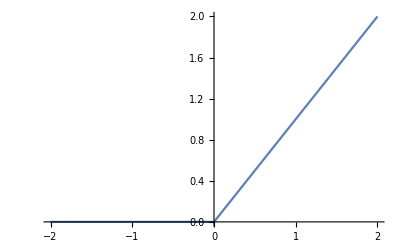

```mathematica
Plot[Ramp[x], {x,-2,2}]
```

It acts as an activation function.

```mathematica
ramplayer1=layersnet[[3]]
```

ElementwiseLayer[<>]

Let us apply it to the input bn1Lion obtained after batch normalization layer:

```mathematica
ramp1Lion=ramplayer1[bn1Lion]
```

{{1},62,{{27.0097,22.1571,23.0991,22.3616,22.2543,22.08,21.4716,21.8285,96,18.9851,18.0954,18.5873,19.2433,19.2133,19.4267,19.8362,15.6184},110,{1}}}
 |  |  |  |

This is an array of size 64x112x112.

```mathematica
ramp1Lion//Dimensions
```

{64,112,112}

One can look at a summary of the values by plotting a histogram.

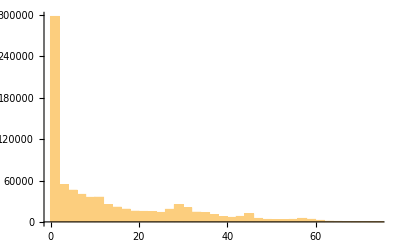

```mathematica
Histogram[Flatten[ramp1Lion]]
```

There are many zeros in the data due to the nature of the Ramp function, hence the peak at low values in the histogram.

As an image:

```mathematica
ramp1LionImage=NetDecoder["Image"][ramp1Lion]
```

-Graphics-

```mathematica
ramp1LionImage//Information
```

Image

I am not sure if I would be able to interpret this image...

Pooling layer

Reduce the number of neurons in subsequent layer.

Has no trainable parameters.

```mathematica
pool1=layersnet[[4]]
```

PoolingLayer[<>]

Here, the input array of size 64x112x112 is reduced to an array of size 64x55x55. To see this, we input an array of size 64x112x112 with random numbers:

```mathematica
RandomReal[1,{64,112,112}]
```

{{1},62,{{0.145036,0.244916,0.21497,0.840179,0.808396,0.426179,0.668336,0.977126,96,0.672608,0.538176,0.418351,0.683765,0.218653,0.263679,0.681439,0.203378},110,{1}}}
 |  |  |  |

```mathematica
pool1out=pool1[RandomReal[1,{64,112,112}]]
```

{1}
 |  |  |  |

The dimensions of the output are as expected:

```mathematica
pool1out//Dimensions
```

{64,55,55}

One can apply the output of the ramp layer for the lion example:

```mathematica
pool1Lion=pool1[ramp1Lion]
```

{{1},62,{{31.2176,23.0991,22.2543,21.8285,20.8921,21.9611,21.6286,21.4023,39,22.6971,20.458,18.9251,16.2769,18.9851,18.9851,19.2433,19.8362},53,{1}}}
 |  |  |  |

```mathematica
pool1Lion//Dimensions
```

{64,55,55}

The histogram looks like a coarse-grained version of the histogram obtained after the ramp.

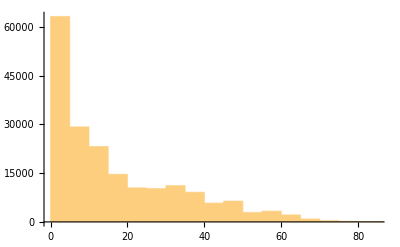

```mathematica
Histogram[Flatten[pool1Lion]]
```

NetGraph layers

The network has several layers that are nested within a graph.

```mathematica
net
```

NetChain[<>]

```mathematica
NetTake[net,"3a"]
```

NetChain[<>]

LinearLayer

The penultimate layer is a linear layer that transforms an array of size 1024x1x1 into a vector of 4315 components - one component for each class.

```mathematica
llayerEnd=layersnet[[-2]]
```

LinearLayer[<>]

The input to the linear layer is what results after the following network in which I have removed the last two layers in the original network:

```mathematica
changedNet=NetDrop[net,-2]
```

NetChain[<>]

I can now apply this to our image of the lion

```mathematica
beforeLinear=changedNet[-Graphics-]
```

{{{0.231257}},{{0.381772}},{{0.0868864}},{{0.107648}},{{0.34095}},{{0.229273}},{{0.281348}},{{0.00327543}},{{0.0225976}},{{0.118917}},{{0.0414447}},{{0.0675815}},{{0.}},{{0.}},{{1.57466}},{{0.166701}},{{0.38087}},{{0.110964}},{{0.22246}},{{0.}},{{1.5254}},{{0.0807903}},{{0.103366}},{{0.524022}},{{0.26886}},{{0.}},{{0.0625461}},{{0.0131607}},{{0.0612862}},{{0.380761}},{{0.137609}},{{0.37249}},{{0.0605095}},{{0.0254447}},{{0.0810264}},{{0.0438981}},{{0.295473}},{{0.0999119}},{{0.0544267}},{{0.453531}},{{0.0542361}},{{0.042398}},{{0.}},{{0.0632409}},{{0.0633892}},{{0.0731521}},{{0.196452}},{{0.0318398}},{{0.}},{{0.}},{{0.129632}},{{0.189839}},{{0.264164}},{{0.0247426}},{{0.146695}},{{0.086266}},{{0.544721}},{{0.}},{{0.806856}},{{0.0469196}},{{0.0042171}},{{0.11061}},{{0.0918034}},{{0.06316}},{{0.062068}},{{0.}},{{0.338403}},{{0.}},{{0.00996839}},{{0.167103}},{{1.15965}},{{0.56948}},{{1.1378}},{{0.0676578}},{{0.}},{{0.268308}},{{0.765746}},{{0.}},{{0.}},{{0.}},{{0.0177051}},{{0.159788}},{{0.512488}},{{0.000312314}},{{0.0421277}},{{0.}},{{0.134298}},{{0.108037}},{{0.0100804}},{{0.048142}},{{0.0683836}},{{0.0794478}},{{0.121568}},{{0.36499}},{{0.236864}},{{0.033216}},{{0.0673661}},{{0.}},{{0.0988357}},{{0.636422}},{{0.}},{{0.212734}},{{0.183805}},{{0.339313}},{{0.347425}},{{0.00794444}},{{0.0879542}},{{0.0550369}},{{1.0408}},{{0.170503}},{{0.00320093}},{{0.0398354}},{{0.160563}},{{0.0307157}},{{0.809574}},{{0.000375247}},{{0.00475674}},{{0.430802}},{{0.00701942}},{{0.}},{{0.0468203}},{{0.264279}},{{0.0991896}},{{0.19249}},{{0.549092}},{{0.}},{{0.407929}},{{0.}},{{0.125487}},{{0.56089}},{{1.56985}},{{0.630145}},{{0.212718}},{{0.}},{{0.0127505}},{{0.}},{{0.101765}},{{0.0742359}},{{0.111838}},{{0.133763}},{{0.0408304}},{{0.0734743}},{{0.}},{{0.801533}},{{0.0710638}},{{0.127248}},{{0.}},{{0.104826}},{{0.}},{{0.0489839}},{{0.0125214}},{{0.00462888}},{{0.0604849}},{{0.28811}},{{0.0931215}},{{0.0071058}},{{0.577875}},{{0.}},{{0.00418414}},{{0.}},{{0.}},{{0.234634}},{{0.120161}},{{0.382572}},{{0.}},{{0.69809}},{{0.311102}},{{0.}},{{0.136281}},{{0.0725147}},{{0.}},{{0.0158745}},{{0.264652}},{{0.32675}},{{0.713338}},{{0.335152}},{{0.0159856}},{{1.23731}},{{0.00842856}},{{0.165094}},{{0.}},{{0.0296263}},{{0.0905253}},{{0.22717}},{{0.}},{{0.0405658}},{{0.086132}},{{0.216459}},{{0.0403554}},{{0.000526847}},{{0.}},{{0.0605365}},{{0.29528}},{{0.198287}},{{0.33573}},{{0.184438}},{{0.}},{{0.00225688}},{{0.0276452}},{{0.0408433}},{{0.}},{{0.279894}},{{0.00720545}},{{0.}},{{0.217571}},{{0.0588096}},{{0.}},{{0.0114267}},{{0.135394}},{{0.}},{{0.}},{{0.115512}},{{0.0899136}},{{0.497719}},{{0.0363561}},{{0.}},{{0.21954}},{{0.0221977}},{{0.00298364}},{{0.547301}},{{0.0524985}},{{0.}},{{0.}},{{0.775197}},{{0.749901}},{{0.0215295}},{{0.358756}},{{0.0924366}},{{0.0121779}},{{0.0908187}},{{0.0161024}},{{0.28193}},{{0.00679162}},{{0.0625006}},{{0.0137291}},{{0.0740253}},{{0.155142}},{{0.118025}},{{0.468665}},{{0.061738}},{{0.}},{{0.141764}},{{0.393968}},{{1.03373}},{{0.0876427}},{{0.0104634}},{{0.}},{{0.118383}},{{0.443801}},{{0.00707575}},{{0.150612}},{{0.17262}},{{0.133728}},{{0.0788892}},{{0.24606}},{{0.}},{{0.}},{{0.0223486}},{{0.0523987}},{{1.28949}},{{0.508733}},{{0.00123389}},{{0.232945}},{{0.739346}},{{0.0191727}},{{0.102379}},{{0.146092}},{{1.4804}},{{0.0508045}},{{0.0712216}},{{0.0509486}},{{0.114276}},{{0.209252}},{{0.00986582}},{{0.399712}},{{0.630927}},{{0.}},{{0.}},{{0.0443406}},{{0.}},{{0.}},{{0.485625}},{{0.363382}},{{0.437911}},{{0.0458114}},{{0.612891}},{{0.217463}},{{0.028902}},{{0.524319}},{{0.}},{{0.3884}},{{0.056366}},{{1.29304}},{{0.16281}},{{0.122287}},{{0.290763}},{{0.337948}},{{0.}},{{0.0132089}},{{0.129251}},{{0.}},{{0.}},{{0.329783}},{{0.30751}},{{0.453274}},{{0.0834273}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.0439618}},{{0.140043}},{{0.}},{{0.}},{{0.00408683}},{{0.180446}},{{0.0827954}},{{0.}},{{0.00356263}},{{0.19592}},{{0.0475062}},{{0.}},{{0.370116}},{{0.259097}},{{0.118335}},{{0.}},{{0.}},{{0.0854913}},{{0.765577}},{{0.127435}},{{0.}},{{0.0971924}},{{0.12357}},{{0.062655}},{{0.00109845}},{{0.0835946}},{{0.0888438}},{{0.148085}},{{0.282745}},{{0.0547524}},{{0.}},{{0.006197}},{{0.0778044}},{{0.0695026}},{{0.0450415}},{{0.181429}},{{0.00422522}},{{0.139334}},{{0.}},{{0.0401143}},{{0.00217001}},{{0.203807}},{{0.329053}},{{0.0117241}},{{0.608111}},{{0.}},{{0.}},{{0.}},{{0.00446927}},{{0.0439999}},{{0.230603}},{{0.59818}},{{0.127625}},{{0.}},{{0.144389}},{{0.0185397}},{{0.22174}},{{0.0111657}},{{0.}},{{0.}},{{0.}},{{0.85723}},{{0.}},{{0.0163376}},{{0.}},{{0.}},{{0.407332}},{{0.290792}},{{0.}},{{0.395896}},{{0.0322327}},{{1.65026}},{{0.36476}},{{0.152178}},{{0.128139}},{{0.}},{{0.132436}},{{0.00813721}},{{0.118749}},{{0.60224}},{{0.114894}},{{0.}},{{0.0100628}},{{0.}},{{0.397213}},{{0.508178}},{{0.00130512}},{{0.0102111}},{{0.}},{{0.00981167}},{{0.17201}},{{0.}},{{0.489111}},{{0.0307268}},{{0.164845}},{{0.}},{{0.129719}},{{0.445143}},{{0.181107}},{{0.0355335}},{{0.259374}},{{0.164729}},{{0.0106627}},{{0.}},{{0.311167}},{{0.681502}},{{0.0544077}},{{0.126284}},{{0.949975}},{{0.}},{{0.0435391}},{{0.00115183}},{{0.0652775}},{{0.}},{{0.}},{{0.190404}},{{0.221333}},{{0.542543}},{{0.132728}},{{0.}},{{1.32043}},{{0.193198}},{{0.}},{{0.6416}},{{0.}},{{0.267382}},{{0.0812033}},{{0.}},{{0.}},{{0.0488232}},{{0.0514398}},{{0.0452416}},{{0.0215511}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.340097}},{{0.112259}},{{0.0439591}},{{0.0201396}},{{0.0209415}},{{0.420789}},{{0.358374}},{{0.}},{{0.0156808}},{{0.129201}},{{0.253877}},{{0.508009}},{{0.}},{{0.}},{{0.423298}},{{0.049319}},{{0.154052}},{{0.195076}},{{0.100401}},{{0.568215}},{{0.}},{{0.}},{{0.}},{{0.470868}},{{0.}},{{0.}},{{0.078593}},{{0.0877386}},{{0.00994826}},{{0.00932444}},{{0.157329}},{{1.70454}},{{0.209853}},{{0.}},{{0.664061}},{{0.}},{{0.193243}},{{0.}},{{0.716037}},{{0.}},{{0.179219}},{{0.}},{{1.36943}},{{0.0395807}},{{0.537775}},{{0.0316607}},{{1.05641}},{{0.140248}},{{0.0519028}},{{0.0742065}},{{0.}},{{0.}},{{1.12015}},{{0.295672}},{{0.128816}},{{0.}},{{0.397296}},{{0.0394292}},{{0.124383}},{{0.}},{{0.}},{{0.203792}},{{0.}},{{0.0829117}},{{0.848609}},{{0.}},{{0.51361}},{{0.167733}},{{0.}},{{0.0582415}},{{0.0473158}},{{0.0906766}},{{0.0697212}},{{0.184385}},{{0.0372195}},{{0.655057}},{{0.279921}},{{0.}},{{0.0066919}},{{0.312785}},{{0.}},{{0.}},{{0.127977}},{{0.}},{{0.0423017}},{{0.43572}},{{0.000481995}},{{0.}},{{0.}},{{0.0146934}},{{0.146049}},{{0.}},{{0.013358}},{{0.0228253}},{{0.375608}},{{0.586804}},{{0.223663}},{{0.24545}},{{0.}},{{0.287981}},{{0.}},{{0.}},{{0.}},{{0.190195}},{{0.236212}},{{0.}},{{0.560096}},{{1.75395}},{{0.0477236}},{{0.0346109}},{{0.000715752}},{{0.}},{{0.28612}},{{0.118831}},{{0.216653}},{{0.0296608}},{{0.402336}},{{0.00893412}},{{0.0898876}},{{0.389543}},{{0.274884}},{{0.0825409}},{{0.232426}},{{0.00569863}},{{0.441465}},{{0.}},{{0.}},{{0.0143046}},{{0.00910978}},{{0.148106}},{{0.200603}},{{0.00595819}},{{0.}},{{0.}},{{0.885561}},{{0.405445}},{{0.}},{{0.}},{{0.}},{{0.0329876}},{{0.0367591}},{{0.}},{{0.0518034}},{{0.173128}},{{0.266631}},{{0.0257082}},{{0.196988}},{{0.0489388}},{{0.0201958}},{{0.111809}},{{0.0247858}},{{0.}},{{0.}},{{0.0319877}},{{0.00165768}},{{0.}},{{0.}},{{0.}},{{0.240329}},{{0.00190497}},{{0.0553088}},{{0.0411244}},{{0.}},{{0.777198}},{{0.134149}},{{0.00349912}},{{0.}},{{0.}},{{0.205158}},{{0.227467}},{{0.}},{{0.}},{{0.444774}},{{0.118482}},{{0.12329}},{{1.69093}},{{0.00357352}},{{0.}},{{0.00488051}},{{0.289231}},{{0.0241429}},{{0.}},{{0.0274652}},{{0.}},{{0.0618855}},{{0.}},{{0.181046}},{{0.806063}},{{0.027625}},{{0.122671}},{{0.162379}},{{0.20766}},{{0.0186619}},{{0.}},{{0.161154}},{{0.}},{{0.}},{{1.06677}},{{0.}},{{0.}},{{0.}},{{1.52324}},{{0.0102011}},{{0.}},{{0.119539}},{{1.45371}},{{0.049929}},{{0.0404445}},{{0.06629}},{{0.222816}},{{0.396235}},{{0.}},{{0.}},{{0.}},{{0.0921444}},{{0.010225}},{{0.214756}},{{0.00734319}},{{0.144877}},{{0.110609}},{{0.605159}},{{0.0271307}},{{0.}},{{0.}},{{0.00471512}},{{0.128781}},{{0.97897}},{{0.0125434}},{{0.132433}},{{0.244553}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.00414966}},{{0.000933258}},{{0.153181}},{{0.}},{{0.0431937}},{{0.}},{{0.001564}},{{0.}},{{0.304036}},{{0.}},{{0.0450952}},{{0.}},{{1.78119}},{{0.}},{{0.00342001}},{{0.}},{{0.0505448}},{{0.191392}},{{0.000774914}},{{0.}},{{0.}},{{1.78354}},{{0.}},{{0.323152}},{{0.549248}},{{0.05819}},{{0.}},{{0.103171}},{{0.0142742}},{{0.}},{{0.816133}},{{0.}},{{0.501504}},{{0.275197}},{{0.}},{{0.85007}},{{0.00784303}},{{0.0263976}},{{0.0110642}},{{0.}},{{0.}},{{0.0176206}},{{1.33299}},{{0.337092}},{{0.00177735}},{{0.0339093}},{{0.429946}},{{0.}},{{0.}},{{0.}},{{0.16877}},{{0.}},{{0.200098}},{{0.215253}},{{0.1931}},{{0.0246658}},{{0.539659}},{{0.74522}},{{0.32333}},{{0.00493127}},{{0.}},{{0.029454}},{{0.}},{{0.247192}},{{0.}},{{0.}},{{0.0485781}},{{0.0295501}},{{0.00842194}},{{0.0953023}},{{0.0625289}},{{0.223231}},{{0.}},{{0.234428}},{{0.0980495}},{{0.0095446}},{{0.186888}},{{0.}},{{0.}},{{0.106693}},{{0.}},{{0.}},{{0.00812494}},{{0.}},{{0.}},{{0.}},{{1.01127}},{{0.}},{{0.0293531}},{{0.}},{{0.536408}},{{0.595992}},{{0.}},{{0.301546}},{{0.121503}},{{0.00569787}},{{0.}},{{0.}},{{0.}},{{0.00434605}},{{0.0263468}},{{0.}},{{0.164499}},{{0.00308349}},{{0.438492}},{{0.357869}},{{0.}},{{0.}},{{0.}},{{0.375701}},{{0.315856}},{{0.}},{{0.241914}},{{0.463956}},{{0.}},{{0.}},{{0.0555394}},{{0.}},{{0.272891}},{{0.}},{{0.286302}},{{0.0431462}},{{0.}},{{0.00928913}},{{0.}},{{0.}},{{0.127843}},{{0.0387816}},{{0.}},{{0.}},{{0.166683}},{{0.}},{{0.}},{{0.0152769}},{{0.0127055}},{{0.00931164}},{{1.69277}},{{0.}},{{0.}},{{0.113899}},{{0.}},{{0.00658126}},{{0.}},{{0.0446089}},{{0.0493934}},{{0.}},{{0.000348573}},{{0.520705}},{{0.}},{{0.0318818}},{{0.00494047}},{{0.0255383}},{{0.}},{{0.0043884}},{{0.203996}},{{0.}},{{0.0376281}},{{0.0130063}},{{0.721719}},{{0.}},{{0.}},{{0.02062}},{{0.}},{{0.123442}},{{0.019738}},{{0.96197}},{{0.}},{{0.}},{{0.184161}},{{0.15424}},{{0.}},{{0.390376}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.00599218}},{{0.}},{{0.00111198}},{{0.431459}},{{0.478195}},{{0.}},{{0.0739771}},{{0.397133}},{{0.}},{{0.145449}},{{0.000519743}},{{0.102197}},{{0.}},{{0.}},{{0.}},{{1.63202}},{{0.000993933}},{{0.688524}},{{0.96749}},{{0.}},{{0.}},{{0.000979146}},{{0.0158933}},{{0.0781271}},{{0.0122507}},{{0.}},{{0.0453839}},{{0.0277355}},{{0.}},{{0.}},{{0.198822}},{{0.00659282}},{{0.}},{{0.}},{{0.234518}},{{0.127431}},{{0.}},{{0.026595}},{{0.306551}},{{0.0518976}},{{0.662281}},{{0.234436}},{{0.0388045}},{{1.48599}},{{0.220655}},{{0.}},{{0.172581}},{{0.}},{{0.391427}},{{0.283933}},{{0.236229}},{{0.15135}},{{0.}},{{0.61836}},{{0.265792}},{{0.47291}},{{0.336087}},{{0.0372989}},{{0.258369}},{{0.0404452}},{{0.0654294}},{{0.0931135}},{{0.432267}},{{0.177798}},{{0.}},{{0.262267}},{{0.571062}},{{0.11144}},{{0.393598}},{{0.363158}},{{0.189705}},{{0.0800326}},{{0.}},{{0.00339834}},{{0.}},{{0.}},{{0.137434}},{{0.790604}},{{0.367845}},{{0.0293192}},{{0.197937}},{{0.85321}},{{0.0938498}},{{0.193511}},{{0.992863}},{{0.}},{{0.350711}},{{0.}},{{0.00263726}},{{0.}},{{1.10413}},{{0.}},{{0.0366454}},{{0.}},{{0.021449}},{{0.064815}},{{0.709865}},{{0.545678}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.132986}},{{0.}},{{0.}},{{0.240742}},{{0.449737}},{{1.32102}},{{0.37311}},{{1.20199}},{{0.30016}},{{0.}},{{0.133336}},{{0.0396424}},{{0.109666}},{{0.0136755}},{{0.943341}},{{0.}},{{0.700012}},{{0.116499}},{{0.0377933}},{{0.}},{{0.01859}},{{0.162331}},{{0.304248}},{{0.381381}},{{0.0822387}},{{0.}},{{0.114313}},{{1.1038}},{{0.641838}},{{1.06997}},{{0.0204308}},{{0.309065}},{{0.18583}},{{0.00395773}},{{0.0150349}},{{0.0650715}},{{0.171328}},{{0.}},{{0.0447879}},{{0.00566742}},{{0.00684943}},{{0.}},{{1.0396}},{{0.975877}},{{0.}},{{0.}},{{0.0612127}},{{0.101191}},{{0.0165326}},{{0.}},{{0.}},{{0.}},{{0.102756}},{{0.0319175}},{{0.651074}},{{0.208469}},{{1.01459}},{{0.}},{{0.178753}},{{0.}},{{0.579506}},{{0.393235}},{{0.0104894}}}

```mathematica
llayerEnd[beforeLinear]
```

{2.14819,-1.81134,1.25185,7.4308,1.59621,-3.4083,-1.76123,-1.80557,1.21503,-4.1108,-1.44891,-2.86928,1.59431,0.75955,-0.118298,0.775672,-0.339949,0.643102,-1.65462,1.00765,-3.18468,-1.2723,-3.14109,0.241175,0.709687,-2.75854,-2.29193,4.56766,0.633017,3.3422,-0.0143661,2.51296,0.0557488,0.68717,-1.89261,-5.69462,0.0437578,-2.35539,-1.37582,-1.91168,2.94185,4.99302,3.04998,2.67022,0.0988208,3.98565,0.272789,-1.96553,-1.16083,-6.90498,-1.08522,1.67493,0.45847,3.8988,1.67202,-0.359856,1.6186,1.91061,5.27441,0.884619,1.33042,2.95559,1.74676,3.59473,0.551229,1.76646,-2.61551,6.79615,-2.83409,-1.74052,0.601661,1.33629,-1.28687,1.03529,-2.72388,-0.30835,0.854701,-1.02603,6.08549,5.14861,-0.0919167,1.3134,-2.53934,-1.92807,0.751689,-4.96338,-0.743078,4.72517,-1.91553,0.630744,-1.07571,-5.81793,-1.08973,-5.1837,-0.0131961,0.00159295,-3.12046,-3.06281,1.10696,-2.24297,-2.43921,4.5912,1.969,2.82938,0.40017,2.24398,5.75211,-1.89576,2.91997,-1.72042,-0.722169,1.64759,6.12903,-9.21408,-3.57424,-2.01126,-1.68554,-0.531896,-4.85978,-0.736353,0.775714,-0.500197,-1.40659,-4.57983,-5.74739,-4.52339,-3.76766,-1.70466,-1.696,0.479221,0.449548,-1.45446,-0.384861,-1.63922,-3.45316,-4.87234,-0.791781,-2.80611,-1.78266,-1.82276,3.25013,1.80183,3.77232,4.87499,0.0554974,3.42395,2.59959,2.43307,1.5671,-0.101446,-1.78382,3.62042,-1.17185,1.20215,-0.0571952,0.296067,-2.03426,-1.58611,-1.21117,3.68798,4.57548,-0.726395,3.01918,5.04398,-3.75206,-4.45081,4.73863,1.10347,5.32794,-5.21856,-1.08476,-5.34164,1.71459,-0.251597,-0.921622,-1.47517,2.39182,5.21967,2.69269,-1.5756,-0.616374,-5.6703,-4.30034,0.210147,-3.96002,-1.85978,-0.416217,0.162345,-1.40875,-0.495446,-3.57916,2.61707,1.98361,1.05731,2.91353,-0.458784,5.75807,-3.82215,1.2613,6.0068,2.9119,2.35696,5.94307,1.98802,4.23243,-3.8643,-1.21984,0.999878,-0.899475,-3.21122,-2.99269,-1.11414,-5.56803,0.543321,-2.29251,4.02438,-3.24428,-5.09373,-5.14195,-1.38812,-0.10388,2.19788,3.25872,3.55221,-1.20795,-1.55317,-0.0713651,-2.09819,-1.71383,3.07838,1.84755,-3.6922,1.57532,5.35571,-0.451613,2.08541,1.0315,3.80547,0.0184615,1.7319,1.53901,1.51932,4.50133,-2.04534,-1.46063,-2.67984,-2.80171,-1.99122,-0.700823,3.72245,-2.66089,-1.78227,-0.592098,-1.34714,-2.21603,1.54825,5.25461,-0.522622,-0.0141998,0.356634,-2.71932,1.2094,3.26686,5.82397,-0.175096,-0.547368,-5.43754,-0.845062,0.254814,-0.785162,0.88338,1.62833,0.46254,-2.82329,11.2732,4.33867,-4.35103,-3.87605,-1.02005,-3.67018,-2.37614,-2.01161,2.92383,-1.18629,-3.31617,1.90249,-3.42584,0.889787,1.69258,0.367374,1.83739,-4.80234,0.285868,2.54006,4.50125,0.399337,3.51626,-1.31633,-1.22674,-0.0341615,-0.389523,-2.12761,2.96636,3.33776,-2.32664,-1.51735,0.732188,-2.27138,-0.212798,-4.08391,-1.09295,1.16022,2.23793,1.05285,0.984064,-2.51133,-0.0718493,-6.21209,-3.90178,-2.62795,-2.77823,-3.44003,-2.74758,-2.63164,-2.23349,-1.86987,-3.75825,-3.05388,-3.77324,-2.60065,-1.59189,5.8548,-1.38573,-3.64967,-3.42079,-5.08045,-0.345803,3.57067,1.38306,-3.92428,-3.16708,1.56372,0.472677,1.44237,-0.661653,1.01175,3.04959,-2.63572,-0.249324,0.0520562,1.36301,-5.18532,-1.50031,0.584529,0.128195,0.2158,-2.65284,-1.04166,3.36224,-2.19623,-0.613096,4.3154,-3.25863,-1.32648,-0.0707282,0.956588,-2.65496,0.54436,-3.70961,0.249196,-0.566878,-0.433243,4.11859,2.3035,-1.67854,1.42686,0.576063,-1.97552,-0.205895,-3.2395,-1.41508,-0.995147,3.2601,-4.15344,-1.11854,-2.80204,-2.9227,-0.909787,-0.272272,-4.50403,0.129289,3.53065,-4.09597,-4.68726,2.20963,0.182859,-0.22782,-3.36678,-2.7726,0.368028,3.03466,3.29475,0.428912,-0.0064172,1.97722,-0.294999,-0.351167,-1.42144,-3.74617,-3.58712,-1.38409,5.33373,3.07192,1.98055,-1.52689,-2.45016,-3.23725,-2.20479,0.671618,6.23541,0.815194,-2.05521,0.943921,-1.30464,1.17973,1.60248,0.737074,3.19134,2.31124,-3.69711,-2.4732,0.993081,-3.56925,2.49203,-1.11951,3.11752,-0.218841,-2.83195,2.96308,-2.658,-5.9877,10.2733,-2.9956,-1.64183,-1.25105,1.96473,-2.50588,-2.74765,-1.81743,0.171979,6.38926,0.507409,-0.507143,6.7898,-0.273306,1.22635,2.53796,-1.69715,2.44429,-0.924472,4.55789,-1.58841,0.425447,1.75935,-3.45354,-4.36117,0.917412,-2.2077,-0.644168,-1.10112,4.9715,0.212512,0.182452,-1.96144,-3.33586,-2.09254,-5.84101,6.67167,-0.541622,0.174345,-3.83162,0.595047,-0.745114,-3.30594,-1.60503,-2.20129,-4.18222,-2.9051,4.46685,-2.35877,1.45876,3.09058,-4.72175,3.69426,0.24341,-3.56659,0.374249,-2.10112,-2.70691,3.83462,-4.53957,-0.329818,4.54308,2.91458,0.32236,-7.38147,-0.353188,5.07067,-0.297162,0.55402,2.07872,-4.86639,5.93525,-2.29402,-2.39818,1.52143,2.89559,-0.100533,3.72221,2.91854,3.60902,2.15742,0.994361,-4.42692,-2.05525,-1.0192,-4.13436,-2.19428,-3.57247,0.932146,4.46319,-2.75254,-1.11764,-1.77768,-0.0742704,-0.530513,1.80544,5.81589,-3.32819,-0.442356,1.97512,-0.123988,-2.02818,-2.90189,-1.6336,-3.3515,0.547959,4.9149,-0.335501,0.705303,-3.88935,0.728708,-4.15042,1.1128,-3.36787,-0.464973,0.0101872,0.0952502,1.62347,0.301239,-4.71066,-1.46017,-2.99613,-1.00519,1.70735,-1.12155,0.992855,4.67114,4.04999,0.408112,4.13874,-1.56302,2.53429,0.492781,3.02607,-1.46378,-3.23044,0.152059,-3.49289,-1.34508,-2.46111,3.83811,-2.27086,0.345763,-5.76922,2.22557,-3.25221,-1.29358,-0.377024,-1.04636,-1.71712,-4.61913,1.25388,2.82181,1.35292,-1.48202,-1.30648,6.16362,0.144453,0.182094,-0.271161,-1.89606,2.83471,3.43575,0.979075,1.18222,4.00274,2.94126,-1.3947,-1.33494,-1.15937,0.308341,-1.11817,0.286572,-5.93919,2.40066,3.34147,1.89069,1.46041,-3.83597,4.66369,-0.183999,-5.1886,2.85936,-0.605656,0.126205,1.15043,-0.28328,3.9715,-0.132079,1.43149,-2.59633,2.81099,-0.47902,0.38763,-1.06119,-6.54253,0.220293,-4.87889,-8.75127,-0.105364,1.52685,4.92638,1.04203,7.0521,3.28601,-2.24845,-3.6145,-1.92368,3.67301,0.346796,0.509818,0.489086,-1.59975,1.75303,3.11477,2.73844,-0.119842,-2.82413,1.84297,3.27677,0.912611,0.271167,-2.09699,1.29159,-0.498725,-2.95877,-3.26301,1.48381,5.06201,6.67564,0.94557,-3.28055,-3.44253,-4.20152,-1.87542,5.07855,-0.798489,-1.74472,-2.38452,-4.01698,-2.14254,-0.194519,2.80982,0.281355,-1.37823,-2.22687,-0.0317227,-1.21785,2.03283,-0.980156,1.07522,-2.75099,-9.63119,0.839051,-1.69246,-0.94139,-2.00614,-5.59896,-1.89766,-1.90888,5.42001,4.44503,4.56953,2.38747,-5.46268,1.18115,2.10827,3.95866,-2.82024,0.141982,1.83252,-2.11378,-4.73964,2.6547,-0.0462271,-0.642165,-1.14593,-0.822509,-1.01318,2.36297,-0.904975,1.35363,0.8002,2.58839,-0.456456,-1.26888,-1.09198,4.71149,0.631164,-1.01872,-2.01871,3.21981,6.15298,-3.07647,1.19603,2.65555,1.82724,3.83109,-3.28899,6.52795,-1.78469,3.92634,-1.7483,-0.50318,1.19719,2.72428,-4.29892,-3.05084,1.57281,-3.23954,2.42209,-3.23126,-1.88457,3.31649,-0.52038,-5.61503,1.18338,7.37725,-1.62086,-3.51445,-1.18116,2.13807,-0.881915,-4.26113,-0.345615,-3.21515,-3.69969,-0.178842,-2.31095,-3.31089,4.44324,-1.42915,-4.03286,-5.21437,-1.89887,0.516825,-4.61894,4.94453,-2.38916,-1.73721,-2.32371,0.13596,-2.34783,-1.43616,5.04835,0.677257,-1.08257,-2.63848,1.65654,-1.9276,-1.49198,-1.46045,-1.40134,5.94003,-7.07301,-2.27183,2.47268,2.07729,0.813132,-0.441316,0.630365,0.573191,1.01102,-6.83518,0.407527,3.02181,2.37278,-2.97779,4.91128,2.64374,-0.855879,1.18143,-0.217135,1.13584,1.64109,-1.42801,0.405919,-0.877452,0.0659839,-2.14805,0.980875,2.22235,-1.83595,-2.17066,1.92745,3.21561,1.37657,4.223,0.704613,-0.261919,0.83523,0.714248,1.40488,-0.694524,0.570276,0.676997,-1.01547,1.58111,-2.63715,-1.62969,-2.7111,0.543981,3.41847,-4.98961,-2.43187,3.08276,-1.82584,-2.56768,-4.30761,-0.64151,0.431748,-4.66766,-1.84185,-2.86168,1.21859,4.90646,-3.25054,-0.60669,-0.491979,-2.39064,0.702458,-0.908566,-4.08223,2.82346,6.83933,-6.76508,4.32665,4.33744,-1.18008,2.18589,2.90778,2.20765,2.955,2.63275,-5.63764,4.10791,-2.69407,-0.81595,1.07983,6.92653,0.835921,-0.77223,1.82319,4.30898,-2.8196,-2.18312,0.853663,-2.15946,-2.63627,4.37572,0.518989,2.86013,1.36299,1.92157,-0.55539,-0.621227,-2.15024,0.54674,-2.50795,1.17902,-2.37604,3.0497,2.29777,3.7071,-0.772643,1.53654,-1.31956,-0.0662781,-3.71793,0.45149,0.922241,-2.79467,-0.828735,5.15218,1.10342,2.45139,-0.482164,1.57363,3.88217,-1.71999,-3.08656,1.14734,3.83515,-2.28403,0.970722,2.84005,-1.79844,-5.68103,1.08088,0.218832,1.56413,2.21632,1.37024,2.60312,2.028,-0.899668,-0.618888,-0.173745,1.75823,3.8993,2.50609,-2.30793,4.01114,-1.49803,-0.561223,-2.46651,-3.80586,3.17783,1.95229,2.96425,-0.940588,-0.884835,-0.414299,3.1101,1.64135,2.07328,4.35557,0.05929,-0.46548,-2.07592,-3.74591,0.577484,-1.05833,1.35387,-1.845,-2.88626,3.89344,0.0403309,-2.53948,1.85781,1.92528,2.19732,-1.58054,-2.11992,2.59293,0.944938,-0.887875,-0.212686,-0.94267,0.591258,3.29854,-2.52378,-0.0444351,4.04316,-0.295459,-0.441132,-5.3879,2.3667,7.49077,0.405941,-2.88032,-3.01827,-2.76962,-1.22901,-0.0102463,-2.57134,-5.382,3.39309,2.92727,-1.54903,-0.279594,-1.74476,-3.37275,-3.86874,-1.69833,-3.04788,0.264283,-0.416592,-3.35862,7.69092,-2.07298,-1.76024,-0.703357,1.28764,-0.15567,0.884368,-0.498671,2.75556,-0.914516,-2.82113,-1.34019,-1.64976,-0.718251,0.97236,0.204021,-1.81054,2.98294,-1.11411,4.02164,3.00194,2.65545,-0.882992,2.69963,3.24687,-1.49714,-3.81068,0.260323,-1.58116,-3.09501,0.504026,-5.44082,0.206767,-3.86708,1.98278,1.59174,1.1713,-3.23327,-2.72672,0.614509,-2.56841,0.145937,0.928441,-2.23225,0.481915,-3.64762,-5.45147,-2.07191,1.38176,1.93015,0.953681,-0.466367,-3.57741,-2.27235,-4.00772,-5.40207,-0.630949,0.129857,3.11749,-0.971736,-0.375496,-1.4957,0.657017,2.93225,4.3796,2.29492,-1.34331,0.75656,-0.0617985,-0.950628,2.32681,6.62854,0.999593,-2.20869,0.460768,-0.829753,0.529463,1.79254,-3.54654,1.76239,-4.14845,-1.86253,2.16199,1.14838,-0.541357,4.82571,-0.977156,-0.564863,3.85014,1.45878,-2.50081,-0.543372,-0.342825,-1.88971,-1.72832,5.92194,2.71645,-3.63252,-5.77531,0.968837,2.84207,-4.38247,-0.938079,0.311971,-0.358213,0.208996,2.50725,-0.723324,-4.44126,0.119967,2.13465,-1.40491,-0.564589,1.32528,4.21543,4.9632,4.72804,3.30112,-2.98175,0.697702,5.74218,0.839548,0.00336071,-0.313655,-4.06955,1.90471,4.5618,0.577174,1.54156,-2.18506,-0.151442,-4.0031,0.524287,-0.0442387,2.02629,-1.17917,4.02028,2.05975,0.210835,1.20789,4.64565,9.79162,9.30687,-2.65289,0.619617,1.77719,0.894627,3.30317,2.57273,-0.269792,3.45208,-0.903105,-2.53615,3.24529,3.07045,-1.64123,-2.95073,3.37644,-0.47522,-2.02542,-6.11488,-1.1314,-2.12791,1.60406,0.255165,4.45966,1.85743,-2.28131,1.02809,3.53805,3.19108,-1.03411,2.01404,-1.5129,0.763337,1.26369,-0.905705,-5.72412,-0.0178268,-2.77892,-5.03784,6.17727,-3.98751,0.401557,-4.54833,-1.26808,-0.758219,-0.700288,-1.997,-0.134892,-0.448327,2.60754,1.60114,1.5716,-2.60644,0.86333,-4.65312,-4.95587,-4.06113,-2.9914,-5.59292,-0.561715,-0.796271,4.77297,0.558195,-2.63987,-0.914748,-5.43313,-1.53887,1.0821,-0.260858,1.8878,-1.30173,-2.02352,-1.2717,-0.387636,-2.7641,-0.135845,-3.36346,-6.93273,-0.740811,-1.12414,-5.68811,-0.852052,-0.758378,-3.59149,-1.42548,-6.07364,5.94788,2.10416,-0.951171,-3.50005,2.68158,-0.442938,0.253849,-2.92856,-0.709713,1.94925,-4.44623,0.851328,-1.7245,0.242638,0.733308,-3.70496,-2.28374,0.68264,3.65597,-0.688188,-2.29567,0.0364781,1.2485,-3.84083,0.529426,-4.6805,-3.45483,4.01784,1.22793,-4.46388,-0.282815,1.00083,2.09383,-1.58954,0.554619,3.94905,3.99102,3.27036,-2.73201,-0.547828,-2.3992,6.34987,3.39475,-0.50404,-3.37742,0.295956,-1.23532,1.32735,1.93664,4.28184,1.78071,3.14989,-1.26457,-0.54603,-1.56592,2.10832,6.1633,-4.36871,0.96841,-0.922101,-2.03161,0.14795,1.85108,-0.225548,0.71036,-3.26512,-3.56718,0.678204,-3.9522,1.47627,-4.78496,-0.888185,-3.02948,2.85512,-1.29977,2.69056,1.77732,-6.00506,1.04493,6.87206,4.65296,3.71864,-2.22846,1.23304,-2.34051,-5.84921,-2.71016,-0.218928,-2.30179,6.96441,-0.967296,-3.52393,0.965623,1.23406,2.91795,0.969771,0.198651,-3.19078,1.00303,-4.32381,-2.5891,-1.34826,1.98244,0.22489,-3.5867,0.593056,0.499318,-2.16934,2.00755,0.101028,-5.74007,0.80708,-2.58237,1.67545,-3.9684,-0.651486,-2.49884,-3.42553,0.700361,1.91224,-0.97233,-2.11481,1.8331,3.16858,5.43525,-1.96682,-2.77443,0.634647,1.35947,1.47962,-1.221,-0.633721,0.645528,0.547169,-2.09965,1.73916,1.07528,2.76592,-3.35536,0.714887,-1.35632,-0.932998,5.45094,5.67463,0.858001,2.76297,4.20228,-2.46031,0.365045,-3.47879,3.58422,-1.03101,-0.960792,2.17972,-1.95381,-6.16912,-3.6739,1.15407,2.67901,-3.79647,-5.43033,11.7093,-4.0107,-2.22229,-0.388209,-8.24228,3.75343,1.6155,0.579985,-0.585964,3.27946,-3.31031,-5.41596,-2.14832,-1.03723,-1.9835,1.18651,-1.64932,-1.94968,-1.72956,1.02654,-7.68249,-0.498647,2.73343,6.25143,-1.11128,-0.846968,-1.02962,3.00908,2.42053,1.79763,2.97035,0.211286,-0.537205,-3.36083,1.58588,-0.864664,2.10271,1.02936,1.19438,0.387078,-1.91862,-3.53637,-0.0760331,-1.26256,3.3393,3.17944,3.04491,0.0621967,-2.60808,-3.04692,-2.41152,-2.00683,-0.0335959,2.80504,3.72055,1.95477,-0.425395,2.47611,0.478975,-0.856319,-1.53926,-3.79061,-0.0868504,-1.39927,-2.86929,0.401956,-1.71314,-1.94014,0.390468,-1.49359,-2.48333,1.08794,2.41971,1.09384,-3.89753,-0.724341,1.9366,-3.7827,-2.67207,1.44347,-3.18424,-3.39417,-2.31998,-1.14973,2.77815,-0.449511,2.4018,-1.58188,-5.15325,0.595408,5.71077,0.887468,3.15139,5.82134,-1.45551,-3.01633,-1.2843,7.45255,-3.29088,1.5077,0.101947,-1.27711,2.13648,-1.37979,-3.56989,-4.23041,4.50679,-2.32739,1.85831,3.84064,2.39784,1.50888,-0.455651,-0.0798562,4.23465,-3.10177,0.878024,-1.27788,-1.21852,-3.96013,-2.13845,-1.56254,-1.31229,-1.29049,3.0991,1.8799,3.38354,2.5004,1.1712,-5.2159,1.54092,9.87556,-0.371745,-1.7225,0.266901,-3.68747,0.213254,1.36708,2.93674,-3.22694,1.69542,-2.39787,-0.230128,-0.650115,-1.99655,-2.23557,-3.00209,-1.89042,-2.14321,-3.7584,0.905325,1.14828,3.22857,2.11883,-2.19353,1.68315,0.586186,-1.22111,-3.30479,-3.83077,1.62731,-2.13987,-2.22212,0.211171,-2.58235,-5.04786,0.829773,-4.46684,0.142113,-1.47182,-4.05446,-1.14608,7.98676,-2.49404,-2.66372,-1.15025,-4.47499,-2.02534,-1.71743,3.14373,2.20711,0.964741,0.393063,0.391013,5.10727,4.52188,-1.83133,-2.55651,0.484231,0.439532,-4.62553,0.43708,0.068206,-1.68022,-1.51674,0.0556256,-2.39624,0.630833,-4.49523,3.45983,-3.39304,-1.54139,-7.61966,3.55375,-4.8163,0.548927,-4.10873,2.22448,5.59052,3.25391,3.18889,-4.12135,0.853045,3.88189,-1.94541,4.67557,0.0211338,-1.56275,-3.54873,1.93472,1.67967,1.61767,3.47614,2.40452,-1.76971,2.53114,-1.70058,3.32102,3.69849,-1.02513,3.14795,-2.4234,-0.143179,7.52325,-1.67466,1.62403,-0.453059,1.87513,-0.147221,-2.42861,2.40018,2.17078,0.947443,5.04386,2.51018,3.4682,0.626351,-3.67461,-1.91856,-1.50458,-0.443817,2.40384,0.0398615,-0.25649,-1.71349,0.885657,-2.60049,-3.84776,-0.309848,2.28796,0.847375,0.466527,-1.21843,-3.57764,-3.84616,-4.10814,-1.43163,-1.89655,-3.25049,1.95885,-0.901922,10.343,2.04871,1.66845,3.04443,1.12933,-2.94498,-0.819494,0.721694,-2.6431,-1.44085,-2.67285,1.00716,-0.566207,-2.38018,1.86644,1.26305,-4.17876,-2.56311,0.272443,0.558104,-0.284205,2.37996,-1.19421,1.39923,-0.563039,2.1954,1.03752,2.04174,1.43777,4.92132,-3.41351,-0.991614,-4.68688,-1.40472,-4.25844,-2.57356,0.988696,2.39416,-2.40493,-3.61704,-1.74961,0.742444,-0.229839,-1.13392,-5.92294,-0.305741,3.08764,2.50586,-3.12526,3.40959,1.35752,-2.17404,-4.40133,0.863939,0.542585,4.51811,-2.28139,7.86974,-0.936864,-2.80346,-3.5048,-5.66856,-4.01102,-4.83251,-5.34057,-2.33802,2.19187,4.14091,2.28916,3.15698,-1.53051,0.96963,-1.3271,3.31449,-5.94193,1.14627,-4.70863,3.21481,-1.37712,1.32373,6.69787,-2.06464,1.36362,0.799761,5.26037,2.94864,1.46986,2.40385,3.90964,2.74705,-1.16152,-1.14743,0.745292,0.689583,-4.42726,-5.58104,-3.17836,-0.570711,-1.3552,-0.499844,-1.28409,6.2636,1.64165,1.41675,-1.44661,0.120688,1.43442,-0.977598,-0.178164,-1.37395,-0.129396,-0.15927,1.6327,-2.29755,-1.86683,-3.45552,-3.92935,4.39901,-0.820335,-4.08999,-0.918159,0.905625,-5.15858,0.947607,0.96152,2.41954,-1.97174,-5.4427,2.4983,-3.47659,-1.77671,-1.68725,0.112497,-3.14541,-5.15017,-4.04966,-3.0492,1.6249,-4.18244,3.07386,-1.28824,-0.0347156,-2.48354,-0.693074,-1.95177,5.50885,-3.88347,1.3947,3.19861,2.03185,-2.1985,2.64895,-4.98938,-0.503331,-5.12733,-2.97975,-0.619237,-2.53553,1.30499,-1.8349,-2.43619,-0.14644,-3.71932,-5.79407,-2.43078,-2.13568,-2.41052,-0.630416,2.0571,-2.98158,-0.982356,-3.80035,5.07161,1.52426,1.82307,-3.94003,2.17643,1.23404,-2.30258,-3.32688,-2.08451,-2.74083,-2.10475,-2.7152,-2.84609,3.29696,-0.935959,-6.14492,0.373789,3.15164,0.841273,-2.38316,-1.91891,0.601616,-1.76346,-2.62965,-4.60492,-4.04232,3.644,-1.54889,0.733294,0.571596,-4.44374,-2.61635,0.380755,-5.02441,-0.463428,-2.64012,-1.52956,-1.36367,-2.59117,-1.22992,-1.81673,4.37681,3.23119,-1.56196,-1.62052,2.6651,-6.41092,6.89918,3.35932,2.07257,8.35008,4.55943,0.917253,8.07089,2.20264,0.785529,-4.08512,2.30368,7.3238,1.34208,5.5041,-7.3452,0.339969,1.28287,-2.32109,3.26551,-0.694885,2.44661,-1.10634,-0.848882,-3.65937,3.2754,-1.15579,2.32839,4.46024,-1.13649,1.8381,2.04078,-3.08378,4.37698,0.272136,-1.54615,-5.46165,2.03597,0.112236,2.2156,-1.58085,-4.31935,0.393639,-2.96143,-1.282,-0.519693,3.23783,-3.3386,0.00116961,0.611182,-1.16235,0.685699,-2.35142,4.94137,-1.20937,-1.89111,0.725895,-4.78825,-4.2973,-3.38833,1.87665,3.11847,-6.74872,-2.28589,0.821878,2.48061,1.2992,-3.11958,1.02144,1.59052,-1.89608,-1.78063,0.22824,4.79919,-2.32409,-2.24254,-2.87936,-2.36024,-1.25135,3.8235,1.23949,3.12583,4.54283,3.3199,7.12945,1.09204,-1.00928,-0.331405,4.13992,-1.25197,-2.12933,-2.40968,1.66735,-4.92923,3.09823,3.5415,1.54395,-1.8889,2.0028,-1.66299,-1.65257,-4.00445,2.15709,4.95569,-2.43932,-2.03616,1.58769,0.73778,-3.3736,-3.09149,-2.29141,0.929635,-0.943271,-1.05261,-5.5772,5.59177,2.83423,-0.697353,0.867861,-0.551673,0.594424,0.556837,0.989963,-1.1227,4.85596,-4.22599,0.17254,-1.70275,-6.35577,4.8172,-5.98804,0.762778,-1.92481,2.02021,-0.791363,-1.72967,-0.0535942,3.84289,-0.202184,-3.96666,5.93714,-0.549745,-0.398678,4.50206,1.85652,0.259753,0.102978,-0.890215,-3.4713,-0.876117,6.4786,3.97552,2.62458,-5.96297,-2.08413,0.60607,2.40532,-1.4276,-0.774624,-2.39763,1.55256,-1.88521,2.58364,-2.21302,3.06007,-0.709815,-6.06699,1.09519,-1.54683,4.12675,-2.29864,2.52732,1.96158,-5.04899,-0.519162,-0.637691,0.914759,-0.867882,-1.17901,-3.28358,1.28836,3.40785,2.41358,1.97061,0.312622,-1.54939,-2.11325,1.13215,1.49415,-0.498352,0.384856,-1.41852,-2.00131,-2.89812,1.78804,5.36418,1.00033,-0.126241,-1.68235,1.6443,-0.234933,5.3846,-1.70746,-1.59542,-1.77971,-3.8214,-6.11112,-3.2716,1.48598,0.0964785,3.13206,-3.4268,-2.94562,-2.76016,3.60797,3.81296,0.144397,-1.77693,-1.23414,4.05157,5.92071,-1.44724,-0.416089,-3.45586,1.46678,-1.57931,3.49712,1.79812,1.47048,3.44181,-2.23712,-0.504965,-4.27025,4.37078,-0.300749,2.17929,-3.48816,0.587906,-0.41408,-0.322561,-2.7957,-4.79111,-0.407632,0.286299,-1.74753,0.689331,-2.82666,0.792251,2.90956,-0.93327,-4.08014,-3.95485,2.61809,-3.11314,-1.05505,0.233071,-0.95871,0.281953,-2.19722,-2.18969,5.79451,0.928525,-3.05186,1.10189,-3.7483,1.29105,-3.55285,-1.8239,-0.875782,-4.95458,0.874175,-3.02872,1.81055,3.16486,3.49236,1.70896,-1.88109,-0.158453,3.99136,-4.08154,1.73054,7.05218,3.21105,3.79821,4.05293,3.12803,3.2404,-1.7282,-1.41642,0.822522,-0.227635,-1.86813,0.679643,4.37298,1.9419,-5.73758,-3.13143,0.656943,2.05702,-2.9762,2.45908,5.9258,1.18455,3.08934,0.75862,1.12666,1.56633,0.621435,-2.13513,-3.67274,7.13865,5.01897,-0.225828,0.723116,5.52171,2.64174,5.7094,-0.720542,0.63271,1.36552,-5.30351,-3.11887,-0.36692,-0.0227849,3.42096,-0.718881,3.42776,2.3581,1.92665,4.11598,2.22388,-6.47299,-1.63172,-1.98786,-4.00621,-1.45071,4.40582,2.56418,1.77738,-2.02411,-1.02662,2.0613,-1.11617,-0.570107,3.47284,2.55658,-0.96911,-0.972366,4.08222,2.41443,0.65419,-2.0208,-4.7441,1.26586,-1.39424,2.00243,2.19727,-2.49342,2.77787,-3.50458,5.13787,3.81761,-1.72984,-3.50309,-1.0465,-1.01806,4.19395,2.96498,2.80974,5.31177,4.14687,-0.940814,-1.49633,1.70276,2.0061,2.93493,-3.24378,0.516205,-2.07944,-0.229485,-0.708153,-2.29779,6.26339,0.0492985,3.80619,-4.39258,-6.11238,2.63087,-1.47937,1.73627,-2.14429,-3.21867,0.182173,2.24702,-3.76514,2.77771,-1.1757,-1.1165,2.21107,-0.0485019,-2.74944,0.381487,4.09735,5.44247,1.44532,3.25139,0.737704,-2.80411,-0.574849,0.827087,2.27394,-2.46731,-2.10038,-3.89769,-4.04602,1.38868,3.42694,2.55137,3.3562,0.870057,-4.15812,1.27202,-4.15562,-4.09954,-6.38694,0.656381,2.85872,-6.03697,2.03818,1.69452,1.70296,2.20334,0.620455,0.355546,5.38261,-1.89981,0.0231493,4.54752,-1.176,1.78068,3.1597,0.350156,-1.22204,2.8177,1.10954,4.29404,-1.25987,-1.50486,-3.42618,-4.78502,-1.62649,-1.83812,0.400375,-1.02737,0.46268,-2.88921,-0.461638,1.38094,2.27808,1.40309,5.04315,-3.4421,-3.9384,0.0816898,-0.431754,-3.2582,-1.21426,-1.2458,-5.56726,-1.7696,-1.6448,-3.07631,2.45839,6.0504,-1.03309,-3.21766,-2.20485,-0.960409,0.833801,1.96569,-2.0592,2.72538,-2.30725,-3.20725,3.53894,3.43717,0.435237,-3.70035,0.667521,3.07851,-4.91348,1.86194,-0.935463,-3.1848,2.48896,-1.59479,0.605142,-2.35564,4.70553,-0.753746,2.02648,-2.12962,1.39508,-4.30418,7.48688,1.4248,1.81362,-2.18781,-5.15559,-2.89601,-5.60883,0.831573,-1.45706,-2.39958,-1.365,2.33654,2.45709,-0.0591269,-4.77816,0.970384,0.69097,-3.07149,2.26204,0.337172,-5.82232,4.68481,-2.33877,2.91884,1.09461,-4.88594,-4.17524,1.4831,3.39772,-2.21758,-0.376723,2.59468,-2.07988,-0.899057,0.0555218,0.870084,-2.59243,4.74561,2.65965,-1.73501,2.53255,-3.92645,-3.49242,-3.76133,-1.54657,-1.09169,-6.00412,-5.77567,3.9119,5.79192,5.44474,-3.06414,2.35895,-1.23374,-0.433498,-4.00007,0.48001,-0.315813,3.98296,1.72524,-1.06892,-2.62091,-5.2789,3.56057,1.99886,1.36326,-5.08768,-0.929145,-0.617045,0.865659,-0.973218,3.35641,3.74157,6.26175,1.81834,-2.03764,3.55942,2.45356,-0.919299,2.36333,4.3735,6.16889,-0.785536,-0.236423,5.64157,-1.77365,-1.66358,-1.71498,3.23741,-2.67503,-0.228004,-0.535198,-3.66204,0.285838,3.97319,-3.29974,-2.69483,1.61742,1.07127,-2.69206,-2.48424,-3.11268,-1.65424,-0.632514,-0.372481,-1.2466,-2.40648,-2.43679,-6.1996,3.43369,1.38983,-2.09997,-0.63174,-1.99486,3.97947,-0.340884,8.50362,0.815706,1.93069,-2.21347,-5.84402,0.861457,-0.0481146,-2.93149,-4.16379,-1.50786,1.64063,-0.24377,3.2981,-2.39269,-0.141105,4.80455,-1.0173,1.18778,-3.94493,0.479422,-1.38116,-2.81523,1.46284,2.33475,0.651675,3.15758,7.27237,-0.526841,0.885949,-3.36117,0.987271,-0.771751,3.04614,-3.94599,-0.382656,3.05855,3.96254,-0.634808,0.751055,4.68372,0.413919,-0.836526,1.97561,-1.81249,-4.03676,0.923031,1.43005,0.518684,-2.18451,-3.10638,5.16937,-3.46161,0.911089,-0.761314,7.64153,-1.15729,0.80193,4.23223,0.473037,-2.20075,3.88837,1.28249,-0.647114,3.27457,-2.30519,-2.44988,3.05642,2.68817,-1.91636,-3.19411,-0.764511,-6.56369,-2.24324,-0.0204034,0.843519,-4.32029,-0.606373,0.322575,2.60873,1.01279,-1.9008,-2.23181,-1.83949,-5.97391,-0.573005,5.09293,-0.358365,-1.8244,-0.112781,0.410432,-4.23664,2.10579,1.76012,3.01082,0.571751,-1.26842,3.77357,-2.8856,3.2713,-1.12279,0.799378,-0.677352,-0.874897,1.04965,1.90733,-2.66635,-0.757023,1.02665,-2.00441,-0.24407,-1.51617,-0.610521,-3.6837,-0.355123,2.31428,5.62642,-2.56849,-0.57404,-3.19219,-0.831723,-0.139105,-7.26362,2.40295,0.465591,-1.61961,2.56504,-0.228726,-0.720471,-3.28168,-0.953209,-1.95842,-0.27454,1.93259,-0.950922,-0.95357,0.951523,4.10177,7.10123,1.46422,-2.69017,-4.08176,-0.96963,-0.316489,4.3031,0.834268,2.23156,-1.287,-0.797424,-3.18041,0.513746,-1.00385,3.07153,0.137119,-3.64222,-1.45989,-1.23374,0.538922,3.6652,-4.48914,0.849492,-2.04596,4.25806,0.491629,-3.53237,0.143795,-1.13117,-1.70029,0.475011,2.02109,2.4051,0.711931,-1.51441,0.281785,-0.492176,-1.80854,-1.44124,1.41665,-1.17509,2.34451,-1.95766,0.0648456,2.1738,-1.57168,-1.49533,-2.46883,-3.30402,-2.50929,-3.39827,7.7154,0.775565,3.87292,-3.57997,0.23416,-2.6232,-3.6929,-0.21294,-3.28325,3.82921,-4.79105,0.894775,-1.15685,3.03271,-2.04681,-3.82469,1.66043,-2.41261,-1.50472,-2.01871,-4.46946,-0.719683,-3.89661,-2.67671,1.53622,-2.61568,2.31894,1.37085,3.80196,2.51509,-1.24982,-0.182224,-0.5705,2.63437,1.71631,2.08918,0.264295,-0.396508,-1.78164,6.00429,0.770279,0.59446,-3.03389,-2.52496,-4.85709,-2.29072,-1.98026,-1.06091,-3.47451,-3.68711,3.64991,-3.76415,0.623236,-6.15994,-2.45581,-1.10416,5.98503,5.77085,0.630941,-2.46683,3.66979,1.21821,-2.5056,1.50872,-1.97534,6.96323,1.45384,-3.25368,-1.40292,0.631907,-3.03069,-2.4629,-5.16781,5.39366,1.64783,-0.30362,2.96511,7.77461,1.75034,-1.1332,-3.62491,-1.16316,-0.203487,-0.763945,6.42268,-2.83003,0.313943,-2.2552,-2.50918,-0.61406,2.72731,-0.553731,4.27723,-3.834,3.5199,1.29105,2.6228,0.926141,-0.0395039,-2.35111,5.51371,-0.930427,-2.57852,-0.630613,4.5822,1.63677,-2.08235,2.39447,3.57908,-0.781525,6.91592,2.23459,2.39378,-3.53575,2.95731,-0.364833,4.20411,-1.86682,2.0705,-1.77734,-0.840832,2.25128,-0.0614226,-0.648471,2.92861,-3.54827,-0.481401,18.9558,-1.08116,-6.33502,-4.5323,-0.373469,-4.9832,-0.77775,-3.52343,0.0898895,-2.45837,0.589124,-2.09451,-0.665036,-3.02873,2.27961,2.0814,-0.873313,1.75771,-0.780075,-2.42478,1.61991,-1.96805,-0.00992996,2.23309,1.91108,-7.6669,1.8686,-1.86704,-1.92592,7.27132,1.46118,-1.9223,5.65307,-0.0661271,-1.11764,-1.45554,4.01261,-1.60935,-3.03982,6.21481,7.51233,0.304961,-2.74761,1.58199,-2.21606,-2.84866,2.31789,-0.672474,-2.60279,-3.41249,1.40263,5.26578,-1.83717,-3.19073,-3.15096,-1.89321,0.603795,1.38373,4.38741,3.83472,-1.20148,3.0751,-0.232027,-0.940649,-5.73445,-0.64316,1.31864,-2.00828,-3.42484,-0.340681,2.77956,-0.945799,-0.158295,-1.31953,-1.87475,1.31755,-0.612093,-1.70837,-5.05491,4.62192,-1.40508,-0.851062,3.78456,4.15067,0.46475,-2.4512,-4.43679,-2.40374,-4.34642,-2.93829,-2.15428,-0.247141,-1.83168,-2.96852,-0.806485,-4.2124,-0.999774,0.368688,-3.4051,3.33059,4.58768,-0.639637,-0.470161,-3.51403,-4.34722,-1.13562,11.0027,-2.22671,7.13266,3.70725,-3.2803,1.51483,2.59595,-0.0868953,1.81995,0.489406,-1.63185,0.380869,-0.243333,-1.41321,0.36535,-2.81678,1.7974,6.22367,-1.03418,3.24037,5.93116,-4.15937,-1.54119,5.87128,-0.813485,3.34835,-3.05604,0.957652,-0.121099,2.78677,0.179222,-4.09825,-3.74136,0.803633,-2.15922,4.37613,3.36903,3.60204,4.46508,-6.57315,4.17873,-0.736918,0.328453,-1.62291,3.23383,-0.78327,-2.74504,0.994434,0.544128,-2.5639,4.02872,0.453646,-2.85738,-0.223961,-0.0736637,-2.64569,-1.0889,2.35971,-0.683813,5.07502,-0.764624,-1.12156,2.20367,-1.6911,2.67793,3.58107,0.906327,1.69083,-3.06845,2.77926,1.67516,-2.56371,-5.30061,-2.04132,-0.726636,-0.895832,-2.6751,-1.82137,1.71175,0.957114,0.0242811,-2.26701,-2.78276,-1.2205,-1.62869,-4.11665,-0.378894,-1.64562,0.736969,1.63895,1.31677,-3.22627,0.149588,-2.2776,1.79991,3.14967,-2.11486,-2.45703,-1.00793,-1.35673,-1.50254,-0.774057,1.92873,5.99562,1.27441,0.407899,-2.23517,0.754165,1.78175,-0.720036,2.14294,-4.43423,3.11096,1.2792,2.07858,2.61282,3.40291,0.784841,1.07486,1.63908,-1.07451,-5.0112,-1.36449,0.724119,-1.46848,2.4253,1.93798,1.41813,1.97224,-3.64669,-1.73248,-4.72756,6.02692,6.62534,2.64308,-1.45408,3.57752,-3.62029,1.36169,-1.77034,-2.14924,5.77486,0.631565,-4.4298,-4.40607,4.25494,-0.959866,-2.75714,-2.16496,-0.549232,0.694683,0.841006,-2.10869,-2.7522,-1.27216,-0.484041,0.038748,-3.23104,-3.11133,1.1603,-2.27763,5.17185,0.576593,-0.407448,1.79487,0.331625,-2.35458,-1.01565,1.48936,5.10618,-3.78418,-1.08015,0.980803,-7.16643,0.909288,1.67389,-1.35079,0.912775,0.0545616,-0.640204,-0.40909,2.18187,5.41981,-3.3672,-1.16359,-2.39321,-2.03238,3.07839,-1.82959,-2.71782,-4.37639,-2.20268,1.93252,-0.259914,1.63127,-1.22521,1.95664,1.32697,9.01342,-2.36164,-2.51506,-0.409884,-0.856203,-0.483988,-1.64242,-2.58099,4.62263,-2.00704,-1.58468,0.645575,-0.646301,0.685549,-6.28007,6.62375,-5.4339,4.48992,-1.41157,-1.028,4.80265,-0.670887,7.72835,0.70348,3.94256,-1.16829,-2.25909,2.81198,-1.11308,-2.52714,4.36729,-5.14415,1.31663,-2.83288,3.58516,5.84534,2.38855,4.19082,-0.994951,0.219261,-2.08501,0.952309,5.56792,-1.81525,-2.6903,-0.920491,-6.58252,2.10677,-0.675892,-4.42292,-1.77155,0.588661,2.84877,-4.55138,-3.36012,0.718678,-8.4107,0.492396,-1.16689,2.32884,2.07038,0.845192,2.99414,8.63551,-4.019,-0.433838,2.11311,-2.20503,0.147559,-1.03169,-0.988169,-2.36563,-4.56523,0.414558,-1.95147,-0.965754,1.98493,0.387155,5.22117,0.591306,2.6336,0.704127,-2.9117,1.29878,3.26512,-0.892113,5.02168,3.20804,1.12449,4.16668,-2.25722,-0.602491,-2.52836,3.00402,-1.38554,-2.50281,7.48792,0.264242,-4.08,1.2142,-2.71076,-2.13427,2.17048,7.48931,1.38824,1.14494,2.65174,-1.33714,-1.81991,3.31413,-2.39566,-0.752995,1.57136,-2.72949,4.65763,4.85412,0.440253,2.15645,0.379855,-1.93461,-0.94558,1.50717,-7.0916,0.728971,3.95989,-4.32235,-1.02315,2.53364,0.477323,-0.449621,1.29588,4.7194,2.26835,2.17231,7.13127,0.916667,5.66446,-1.53575,-1.4904,5.74781,0.909051,1.58701,4.30515,3.35095,0.183282,-2.12419,2.78219,-0.199649,-0.695537,-3.47629,-1.69263,1.34388,1.9133,1.48324,-4.59888,-0.228595,-1.25717,-3.60204,0.434087,1.85918,-4.64319,9.29018,-1.17901,-3.37806,1.65214,3.87468,-5.9489,-0.160055,-0.191167,-0.43631,-1.67475,-2.86574,-1.59172,3.58492,1.89215,0.804468,-1.79862,0.161209,1.25269,0.175412,-2.07465,0.805603,-4.17871,-1.15353,5.3402,-1.14379,1.24751,-1.30057,-1.83325,1.02294,-3.47774,2.73843,1.95022,-3.61295,-5.01572,-0.645443,0.0432193,4.74157,-1.04548,-2.8002,2.39443,2.9397,10.3721,1.79924,0.0811987,4.80539,0.159037,7.82035,-2.15165,2.76512,3.98137,3.10402,-1.55122,3.28805,5.43999,0.719933,1.32484,-0.566007,3.80978,7.60338,3.69327,-0.107473,-1.98067,-3.87138,-0.0733589,1.61277,-0.258425,-0.227725,-2.09195,4.06345,1.88216,3.12313,0.210681,2.82448,0.2448,-1.22254,1.30206,-2.99973,0.531704,4.30469,1.73214,-3.13912,-3.35233,2.28326,-2.89755,5.25761,-6.1548,1.98874,-0.766469,0.924854,-1.45544,1.76312,-0.244027,0.779994,-5.44038,-1.85057,-1.11369,-0.496894,3.66253,0.201288,-1.13712,-0.157975,0.364982,4.92825,2.0126,-2.75588,3.06186,-1.85039,0.268316,-1.19967,4.93978,5.02605,-2.22132,2.29814,-0.807679,-0.323575,-2.40749,-0.369873,4.82352,0.00542969,-3.15448,-7.66727,-0.0999735,1.0327,-3.01758,-0.521622,-5.59425,-2.33301,-1.69336,0.852181,-2.48644,2.86033,-0.708542,-1.10239,1.78193,-2.42385,6.12774,-1.52729,-1.33626,-1.81364,0.607545,-3.76755,-2.02492,-3.29215,1.42151,-0.384448,4.31175,-0.0190266,3.62489,-0.479981,-4.94188,-2.05929,2.21237,-0.698908,1.24837,-0.532115,-0.051048,3.45577,3.15788,3.40965,1.09933,5.98287,5.06839,7.11338,5.10235,-1.55914,-3.60567,0.819314,-0.72169,-4.52319,-1.49173,-3.73393,-0.756928,3.89064,-4.22293,-6.80056,-4.75868,-0.313439,0.714302,-0.00624843,0.392274,-3.65073,2.72478,-1.41601,2.79563,-0.983072,0.988134,-0.574993,3.37426,2.0015,-2.61429,-4.1161,-3.23531,-1.86822,2.95955,-1.14029,5.96444,-0.957451,-1.23299,2.67453,2.74523,6.955,2.14271,-0.855495,5.50369,-2.4963,-3.61806,-0.0881029,-3.13869,-2.44781,-2.06732,-3.40881,-4.428,1.58052,0.53378,2.35198,-0.225539,1.98208,7.2527,-0.116711,-0.136393,4.99491,-1.86317,-1.71442,2.69481,2.30486,5.78532,-1.35344,6.49701,1.84347,3.54579,2.95328,2.44567,-1.83681,3.92011,-4.14426,0.258307,-1.47583,0.386263,1.54764,-2.00083,1.95638,2.16458,-3.65986,-0.206696,4.12287,0.0600502,-2.42133,-2.62734,0.491106,-1.37477,-6.32835,1.8484,2.82606,-0.938427,0.626338,-1.86459,-3.41616,-1.26311,-0.776736,-6.92164,-1.28684,-0.880989,-1.42446,5.11313,3.91376,0.351657,-1.68018,-1.53652,-2.01846,-1.343,-2.85817,-2.71344,-1.06151,-1.72219,-0.919972,-1.1257,-2.29308,-0.583276,-1.22629,3.87996,2.61932,3.69588,3.17537,2.16525,5.4201,-0.697004,3.64736,-0.0584398,0.656652,-0.77582,-3.10154,-1.71215,-0.772762,2.09472,4.18089,-0.757966,1.38661,-0.0304895,6.20484,0.251397,-0.795212,2.23261,0.845837,1.66869,0.698309,-0.987816,-0.0830534,-0.902902,-1.03798,0.195569,-0.189767,1.32649,1.38883,1.20537,-1.79473,-3.58369,-0.532633,0.123105,4.16413,-0.492582,-2.59945,-2.47576,-4.73965,-3.07456,4.78706,-4.01308,1.30704,5.76489,-2.77121,-2.34117,2.96738,5.42373,-3.66931,3.18511,5.13151,-2.86303,-4.00374,1.27944,-3.94314,-1.37419,-0.466716,3.79394,-1.2276,1.75145,-4.11254,-0.999799,2.89749,-1.23154,-3.23072,0.802798,-2.07754,0.161058,1.74893,-4.6448,-0.445642,2.67666,-3.66854,0.896521,-3.71546,-3.06528,-4.76939,-0.756712,-0.237379,-0.779751,5.69474,1.62522,3.57464,-2.40664,-1.50573,6.27882,-2.59133,2.25225,-2.09331,-0.0458439,2.74327,5.20439,-0.581325,-5.81835,-3.18265,5.09357,6.89451,-0.950751,0.226841,-4.54076,3.45108,-4.72762,-0.0037877,-4.45292,2.54202,-2.1983,-3.59656,0.799267,2.81037,4.19313,-2.23267,-1.7632,1.63515,0.00821534,-1.90812,-0.874872,0.71702,-2.23881,2.65093,4.53216,3.03586,-2.78743,3.3734,-0.748766,4.20415,-0.638252,3.91726,-1.67139,0.19035,-1.78577,-3.59739,1.79005,-2.35198,0.552928,-1.00907,-0.912563,-1.65145,-1.3414,-0.213007,-3.3744,-1.67845,0.861251,6.76964,-0.345278,1.20931,-0.530503,3.71762,0.578958,-0.440191,-2.58561,-6.23446,0.992643,2.27852,2.26042,-3.05862,1.82088,0.734978,2.53484,1.33002,-2.22736,-2.11524,0.103434,-2.55182,-1.60464,4.54443,2.48264,-5.39059,-3.61183,-3.17806,-1.928,-2.13989,0.272315,1.40502,2.25763,-1.75494,-0.575083,-1.67833,1.63953,2.46217,-2.74983,3.05575,-0.131068,5.7681,6.70073,-1.35756,0.502933,0.117753,-2.14095,1.49368,-6.29441,-4.07723,1.05736,9.58146,-3.57031,-1.61775,-2.92686,1.10289,-2.76663,-2.14099,-0.0529388,4.62812,-0.185093,2.38947,3.80504,0.0123103,3.61318,-0.728271,5.87625,5.54397,-0.0426448,0.0888453,2.31644,-2.17543,-0.27902,1.91929,-1.26252,0.691716,-3.72733,0.729698,0.588423,-0.747562,0.274919,-2.68272,-2.97706,-0.75149,-3.65954,1.10717,1.76012,-0.11474,1.31733,1.35524,-0.263191,3.63084,-2.50508,0.935374,3.47038,-0.837503,2.08663,6.80912,10.4641,3.16141,-4.39439,5.71118,2.86902,1.47703,2.23316,1.04041,-0.910965,-2.29171,0.32655,0.778163,-1.14064,1.07186,2.16865,1.03688,-5.68838,-0.800262,1.93073,1.99723,1.64915,1.82874,-0.373005,2.80113,3.26382,3.79582,-6.35542,-2.84401,0.161393,1.23748,-3.08173,-0.962765,-0.547071,1.07727,-2.20502,2.2829,0.317977,0.144975,0.641276,3.74644,0.792839,-1.18363,0.0507939,1.4777,-3.88743,-4.70093,0.465181,-4.22485,-0.780775,4.82581,2.9533,10.9947,1.56571,1.83744,-2.7853,-3.48665,-1.52397,1.72384,-3.93825,-0.603388,-4.74775,-4.7013,1.74912,2.07314,-2.7917,2.68725,-2.34334,-0.431597,-2.4212,-3.13514,2.1274,4.83361,-2.44224,0.813727,0.771202,-2.93121,0.271629,0.957529,2.42831,-0.946588,1.7484,-2.19458,5.00204,4.26395,-1.43149,4.64548,-0.455274,-3.69445,0.316364,0.748563,-2.29732,-4.56951,-3.42271,3.23792,-3.48481,0.461769,3.25481,-1.87437,-0.160641,6.19166,3.48481,1.87608,0.231711,0.887658,0.725782,1.81036,-1.40817,2.71407,-3.91825,-5.0047,-9.64672,-0.761994,-4.91756,2.91733,1.37863,2.87343,-0.570117,1.11928,-2.08598,2.83521,-0.499168,-0.491198,3.03181,1.40271,1.47671,3.16123,1.30816,-1.10928,-0.429029,0.0152009,3.31974,3.7092,-0.532894,6.30957,2.74355,-4.92943,0.0155706,2.92077,-1.81756,-0.623572,-1.23462,-1.99148,-0.796825,-2.2536,-0.684887,5.78271,-3.1145,-2.04661,0.054671,1.68561,2.51749,-2.71276,-1.96569,0.922569,-3.38742,-2.76811,-0.712005,-1.56909,3.36872,-1.30976,0.727072,3.66566,-1.3439,-2.7421,-1.26887,4.85056,1.86016,1.13378,0.00620897,6.6432,-1.04978,0.903415,3.27232,1.86662,1.8605,4.03916,3.34342,7.12408,-0.995665,1.68531,-0.267574,-3.01953,-3.78199,-4.26268,-0.4383,-2.95301,-0.203583,0.274025,-0.681979,-1.31935,-0.0175837,0.249218,7.29977,3.62093,-5.08749,2.63289,7.51804,-6.35351,0.432557,1.00922,2.6774,-3.76753,-0.573103,-0.504795,3.30553,-1.89972,3.55521,4.08672,-3.61175,1.11518,0.691356,1.35603,0.42734,3.23802,2.59172,1.07628,4.27319,2.29542,2.90311,6.28738,1.16771,0.609688,4.47399,3.19593,1.99112,-0.962541,3.24961,2.50963,-3.14266,-2.78276,3.30171,0.0599516,-0.630332,0.396814,1.53099,2.01602,-0.444406,0.0591347,2.11995,1.93617,-0.140076,-1.11072,1.66942,-3.69174,4.93457,-3.12672,-4.42177,4.60312,0.506378,-0.430729,-1.93835,0.271707,1.27535,-2.06883,-3.79725,-2.73597,2.20896,-0.322294,-1.70995,1.49096,1.40394,-2.02452,-0.847363,-0.178231,9.05116,10.2049,-1.62898,-3.24733,-0.128486,-1.24358,-5.07642,-1.08029,-0.268053,1.70169,-1.19417,1.34954,-4.6728,-0.36783,0.832527,2.76186,-0.999381,0.652479,1.19866,-2.82457,2.44955,-0.936611,2.90552,1.16951,8.04419,-0.927468,9.53382,-3.26201,-2.16398,-5.34516,2.71458,-0.0481921,1.93401,2.90676,3.16362,5.49095,2.78382,-2.73346,-3.67442,-0.931653,1.24968,-4.03798,4.26418,-3.91776,1.39416,-2.13641,-6.6002,1.28642,4.8147,-2.82544,-4.1554,-3.44974,-1.55763,-3.37789,1.31715,3.04878,1.51749,0.782037,0.0390621,1.02289,-3.39764,1.38492,2.06771,-3.87727,0.832648,2.22916,-0.84779,0.35904,0.769202,0.465564,3.23835,-0.2269,2.69556,2.00555,0.876807,0.0904411,2.96801,2.12209,0.0125575,-3.57509,-1.28595,0.408818,-3.77133,3.28721,-1.29524,4.49108,7.61191,0.467001,0.26366,-4.25955,-0.284413,-1.21635,1.28673,-0.895332,0.918793,3.43908,-1.93405,0.739561,-1.54197,1.23692,-0.108888,1.18505,1.94021,0.245973,-0.459729,7.46423,2.90904,-4.55994,2.63129,-1.14776,-4.78549,-0.741778,10.6943,4.18986,3.65174,-2.75296,1.02133,4.33612,-2.16615,5.83286,2.48037,2.57175,-1.36935,1.43359,6.48438,-0.62237,-1.6643,-1.77555,-6.14524,-2.54913,4.02204,0.827685,-4.49108,-1.02994,0.927486,1.6807,-6.49088,-0.987573,-3.64984,2.89736,4.2908,-3.91513,-1.84552,2.18178,-2.05352,3.80394,4.08362,-1.75225,-5.81837,-0.376607,2.6972,1.81492,0.0670853,2.20916,-0.459702,0.149437,1.07487,2.88028,-1.06245,-0.877433,-0.481271,-1.09634,0.654048,-2.01007,-1.18703,-0.102093,2.51989,-1.6035,5.05743,2.62768,0.0887223,0.643081,0.831908,0.0171938,4.18181,-6.14514,-4.23539,-0.151451,-0.320304,0.0537059,1.45242,-1.58341,-0.913199,-3.70622,-1.21922,-0.175899,-0.0977225,4.80099,-1.41406,0.95551,3.66454,-2.24085,1.89578,-0.913969,2.39183,2.03596,-0.00313337,3.08691,2.78271,-1.22954,0.732665,4.69816,-0.315985,0.926632,7.00836,0.193033,2.53864,-1.90555,1.1127,1.29142,4.33374,2.20162,3.57692,1.79124,1.61446,-3.49702,1.68033,3.07694,-1.52431,1.09074,-3.71404,-0.891802,0.435272,-1.24984,0.965512,3.78844,0.645781,4.79113,1.21179,2.46198,5.68879,0.257184,3.93866,2.8814,0.915623,-1.61175,-1.52871,-1.26584,1.65106,-2.48208}

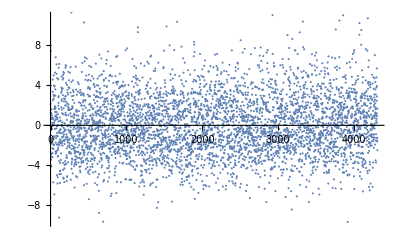

```mathematica
ListPlot[llayerEnd[beforeLinear]]
```

SoftMaxLayer

The last layer of the network should convert neural activities into class probabilities (remember that the aim is to assign a class to the image introduced at the beginning of the networks).

```mathematica
smlayer=layersnet[[-1]]
```

SoftmaxLayer[<>]

It takes the numerical output for each class and normalises it. 

For instance, if we input a signal equal to 1 for each of the 4315 classes:

```mathematica
smlayer[ConstantArray[1,4315]]
```

{0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175,0.00023175}

it outputs a vector of normalised 1’s so that

```mathematica
Total[smlayer[ConstantArray[1,4315]]]
```

1.

If we apply it to the output of the previous layer in the network (i.e. the linear layer described above):

```mathematica
smlayer[llayerEnd[beforeLinear]]
```

{4.99501×10^-8,9.52655×10^-10,2.03827×10^-8,9.83435×10^-6,2.87617×10^-8,1.92923×10^-10,1.00161×10^-9,9.58162×10^-10,1.96458×10^-8,9.5563×10^-11,1.36879×10^-9,3.30732×10^-10,2.8707×10^-8,1.24583×10^-8,5.17861×10^-9,1.26607×10^-8,4.14907×10^-9,1.10888×10^-8,1.11429×10^-9,1.59663×10^-8,2.41268×10^-10,1.63319×10^-9,2.52018×10^-10,7.41873×10^-9,1.18523×10^-8,3.69462×10^-10,5.89138×10^-10,5.61432×10^-7,1.09775×10^-8,1.64849×10^-7,5.74579×10^-9,7.19375×10^-8,6.16311×10^-9,1.15884×10^-8,8.78288×10^-10,1.96085×10^-11,6.08966×10^-9,5.52914×10^-10,1.47258×10^-9,8.61705×10^-10,1.10463×10^-7,8.59077×10^-7,1.23078×10^-7,8.41884×10^-8,6.43438×10^-9,3.13713×10^-7,7.65702×10^-9,8.16523×10^-10,1.82577×10^-9,5.8451×10^-12,1.96918×10^-9,3.11171×10^-8,9.21936×10^-9,2.87617×10^-7,3.10268×10^-8,4.06729×10^-9,2.94129×10^-8,3.93872×10^-8,1.13825×10^-6,1.4118×10^-8,2.20487×10^-8,1.11992×10^-7,3.34346×10^-8,2.12208×10^-7,1.01154×10^-8,3.40998×10^-8,4.26273×10^-10,5.21337×10^-6,3.42577×10^-10,1.02257×10^-9,1.06387×10^-8,2.21786×10^-8,1.60956×10^-9,1.64138×10^-8,3.82494×10^-10,4.28227×10^-9,1.37019×10^-8,2.08924×10^-9,2.56143×10^-6,1.0037×10^-6,5.31704×10^-9,2.16766×10^-8,4.60012×10^-10,8.47697×10^-10,1.23607×10^-8,4.07398×10^-11,2.77252×10^-9,6.57208×10^-7,8.58391×10^-10,1.09526×10^-8,1.98799×10^-9,1.73338×10^-11,1.96031×10^-9,3.26842×10^-11,5.75251×10^-9,5.83822×10^-9,2.57272×10^-10,2.72539×10^-10,1.76335×10^-8,6.18698×10^-10,5.08456×10^-10,5.74809×10^-7,4.17558×10^-8,9.87127×10^-8,8.69722×10^-9,5.49716×10^-8,1.83527×10^-6,8.7553×10^-10,1.08073×10^-7,1.04332×10^-9,2.8311×10^-9,3.0278×10^-8,2.67544×10^-6,5.80718×10^-13,1.63424×10^-10,7.80025×10^-10,1.08036×10^-9,3.42444×10^-9,4.5187×10^-11,2.79123×10^-9,1.26613×10^-8,3.53473×10^-9,1.42795×10^-9,5.9785×10^-11,1.86007×10^-11,6.32563×10^-11,1.34684×10^-10,1.0599×10^-9,1.06911×10^-9,9.41266×10^-9,9.13746×10^-9,1.36121×10^-9,3.96685×10^-9,1.13158×10^-9,1.84459×10^-10,4.4623×10^-11,2.64072×10^-9,3.52298×10^-10,9.80369×10^-10,9.41833×10^-10,1.50349×10^-7,3.53277×10^-8,2.53448×10^-7,7.63432×10^-7,6.16157×10^-9,1.78892×10^-7,7.84469×10^-8,6.64139×10^-8,2.79365×10^-8,5.26661×10^-9,9.79235×10^-10,2.17729×10^-7,1.80576×10^-9,1.93944×10^-8,5.5049×10^-9,7.83734×10^-9,7.6229×10^-10,1.1933×10^-9,1.73615×10^-9,2.32947×10^-7,5.65841×10^-7,2.81916×10^-9,1.19345×10^-7,9.03983×10^-7,1.36801×10^-10,6.80184×10^-11,6.66117×10^-7,1.7572×10^-8,1.20084×10^-6,3.15644×10^-11,1.97007×10^-9,2.79089×10^-11,3.23763×10^-8,4.53234×10^-9,2.31918×10^-9,1.33331×10^-9,6.37298×10^-8,1.07761×10^-6,8.61014×10^-8,1.20591×10^-9,3.14703×10^-9,2.00913×10^-11,7.90636×10^-11,7.19209×10^-9,1.11116×10^-10,9.07609×10^-10,3.84439×10^-9,6.85638×10^-9,1.42488×10^-9,3.55156×10^-9,1.62623×10^-10,7.98303×10^-8,4.23701×10^-8,1.67793×10^-8,1.07379×10^-7,3.68419×10^-9,1.84624×10^-6,1.27542×10^-10,2.05762×10^-8,2.36761×10^-6,1.07204×10^-7,6.15467×10^-8,2.22143×10^-6,4.25572×10^-8,4.01524×10^-7,1.22277×10^-10,1.72115×10^-9,1.58427×10^-8,2.37111×10^-9,2.3495×10^-10,2.92335×10^-10,1.91304×10^-9,2.22549×10^-11,1.00358×10^-8,5.88796×10^-10,3.26103×10^-7,2.27308×10^-10,3.57612×10^-11,3.40777×10^-11,1.45458×10^-9,5.25381×10^-9,5.24949×10^-8,1.51647×10^-7,2.03374×10^-7,1.74173×10^-9,1.23326×10^-9,5.42744×10^-9,7.15087×10^-10,1.05022×10^-9,1.26623×10^-7,3.69804×10^-8,1.4524×10^-10,2.81671×10^-8,1.23465×10^-6,3.7107×10^-9,4.69106×10^-8,1.63518×10^-8,2.61989×10^-7,5.93754×10^-9,3.29417×10^-8,2.71627×10^-8,2.66332×10^-8,5.25402×10^-7,7.53895×10^-10,1.35283×10^-9,3.99714×10^-10,3.53851×10^-10,7.95813×10^-10,2.89218×10^-9,2.41116×10^-7,4.0736×10^-10,9.80749×10^-10,3.22436×10^-9,1.51542×10^-9,6.35592×10^-10,2.74148×10^-8,1.11593×10^-6,3.45635×10^-9,5.74674×10^-9,8.32671×10^-9,3.84241×10^-10,1.95356×10^-8,1.52886×10^-7,1.97201×10^-6,4.89267×10^-9,3.37187×10^-9,2.53568×10^-11,2.5037×10^-9,7.52062×10^-9,2.65826×10^-9,1.41006×10^-8,2.97004×10^-8,9.25694×10^-9,3.46299×10^-10,0.000458668,4.46531×10^-7,7.51557×10^-11,1.20849×10^-10,2.10179×10^-9,1.48474×10^-10,5.4156×10^-10,7.79757×10^-10,1.08491×10^-7,1.77989×10^-9,2.11541×10^-10,3.9069×10^-8,1.89568×10^-10,1.41912×10^-8,3.16715×10^-8,8.41662×10^-9,3.66062×10^-8,4.78586×10^-11,7.75782×10^-9,7.39135×10^-8,5.2536×10^-7,8.68999×10^-9,1.96193×10^-7,1.56284×10^-9,1.70932×10^-9,5.63317×10^-9,3.9484×10^-9,6.94355×10^-10,1.13204×10^-7,1.64119×10^-7,5.69042×10^-10,1.27824×10^-9,1.2122×10^-8,6.01367×10^-10,4.71164×10^-9,9.81677×10^-11,1.95402×10^-9,1.85981×10^-8,5.46399×10^-8,1.67046×10^-8,1.55942×10^-8,4.73078×10^-10,5.42482×10^-9,1.16873×10^-11,1.17779×10^-10,4.21001×10^-10,3.62259×10^-10,1.86897×10^-10,3.73533×10^-10,4.19452×10^-10,6.24591×10^-10,8.98489×10^-10,1.35957×10^-10,2.74984×10^-10,1.33934×10^-10,4.32654×10^-10,1.18643×10^-9,2.03373×10^-6,1.45806×10^-9,1.51551×10^-10,1.90528×10^-10,3.62392×10^-11,4.12486×10^-9,2.07162×10^-7,2.32404×10^-8,1.15159×10^-10,2.45552×10^-10,2.78424×10^-8,9.35126×10^-9,2.46606×10^-8,3.00771×10^-9,1.6032×10^-8,1.23029×10^-7,4.17744×10^-10,4.54264×10^-9,6.1404×10^-9,2.27792×10^-8,3.26311×10^-11,1.30021×10^-9,1.0458×10^-8,6.62618×10^-9,7.23285×10^-9,4.10653×10^-10,2.05685×10^-9,1.68186×10^-7,6.48302×10^-10,3.15736×10^-9,4.3626×10^-7,2.2407×10^-10,1.54706×10^-9,5.4309×10^-9,1.51715×10^-8,4.09786×10^-10,1.00462×10^-8,1.42733×10^-10,7.47847×10^-9,3.30671×10^-9,3.7795×10^-9,3.58319×10^-7,5.83426×10^-8,1.08795×10^-9,2.42811×10^-8,1.03698×10^-8,8.08414×10^-10,4.74427×10^-9,2.28397×10^-10,1.41588×10^-9,2.15477×10^-9,1.51856×10^-7,9.15738×10^-11,1.90465×10^-9,3.53735×10^-10,3.13528×10^-10,2.34678×10^-9,4.43959×10^-9,6.44929×10^-11,6.63343×10^-9,1.99036×10^-7,9.69909×10^-11,5.36957×10^-11,5.31151×10^-8,6.99848×10^-9,4.64139×10^-9,2.01101×10^-10,3.64304×10^-10,8.42213×10^-9,1.21207×10^-7,1.5721×10^-7,8.95082×10^-9,5.79165×10^-9,4.21001×10^-8,4.33982×10^-9,4.10279×10^-9,1.4069×10^-9,1.37609×10^-10,1.61333×10^-10,1.46045×10^-9,1.20781×10^-6,1.25808×10^-7,4.22406×10^-8,1.2661×10^-9,5.02919×10^-10,2.28913×10^-10,6.42776×10^-10,1.14096×10^-8,2.97574×10^-6,1.31712×10^-8,7.46486×10^-10,1.49806×10^-8,1.58121×10^-9,1.89643×10^-8,2.89425×10^-8,1.21814×10^-8,1.41765×10^-7,5.8796×10^-8,1.44529×10^-10,4.91466×10^-10,1.57354×10^-8,1.64242×10^-10,7.04473×10^-8,1.90279×10^-9,1.31677×10^-7,4.68325×10^-9,3.43312×10^-10,1.12833×10^-7,4.08539×10^-10,1.46273×10^-11,0.00016875,2.91485×10^-10,1.12863×10^-9,1.66826×10^-9,4.15779×10^-8,4.75661×10^-10,3.73507×10^-10,9.4687×10^-10,6.92274×10^-9,3.47062×10^-6,9.68176×10^-9,3.51026×10^-9,5.18038×10^-6,4.435×10^-9,1.98695×10^-8,7.37585×10^-8,1.06789×10^-9,6.71633×10^-8,2.31257×10^-9,5.55976×10^-7,1.19056×10^-9,8.91987×10^-9,3.38583×10^-8,1.84389×10^-10,7.43973×10^-11,1.45887×10^-8,6.40911×10^-10,3.06077×10^-9,1.93811×10^-9,8.40785×10^-7,7.20912×10^-9,6.99563×10^-9,8.19873×10^-10,2.07416×10^-10,7.19133×10^-10,1.69383×10^-11,4.6032×10^-6,3.39129×10^-9,6.93915×10^-9,1.26339×10^-10,1.05685×10^-8,2.76688×10^-9,2.13715×10^-10,1.17093×10^-9,6.45034×10^-10,8.89762×10^-11,3.19094×10^-10,5.07596×10^-7,5.51047×10^-10,2.50682×10^-8,1.28177×10^-7,5.18753×10^-11,2.34415×10^-7,7.43534×10^-9,1.6468×10^-10,8.47467×10^-9,7.12993×10^-10,3.89038×10^-10,2.69739×10^-7,6.22414×10^-11,4.19132×10^-9,5.47804×10^-7,1.07492×10^-7,8.04616×10^-9,3.62959×10^-12,4.09451×10^-9,9.28441×10^-7,4.33045×10^-9,1.01437×10^-8,4.6598×10^-8,4.48894×10^-11,2.20412×10^-6,5.8791×10^-10,5.29754×10^-10,2.66894×10^-8,1.0547×10^-7,5.27143×10^-9,2.41059×10^-7,1.07918×10^-7,2.15262×10^-7,5.0413×10^-8,1.57556×10^-8,6.9663×10^-11,7.46459×10^-10,2.10357×10^-9,9.33382×10^-11,6.4957×10^-10,1.63713×10^-10,1.48052×10^-8,5.0574×10^-7,3.71687×10^-10,1.90636×10^-9,9.85262×10^-10,5.4117×10^-9,3.42918×10^-9,3.54555×10^-8,1.95612×10^-6,2.09014×10^-10,3.74521×10^-9,4.20119×10^-8,5.14922×10^-9,7.66943×10^-10,3.2012×10^-10,1.13796×10^-9,2.04197×10^-10,1.00824×10^-8,7.94513×10^-7,4.16757×10^-9,1.18004×10^-8,1.19253×10^-10,1.20799×10^-8,9.18507×10^-11,1.77366×10^-8,2.00882×10^-10,3.66145×10^-9,5.88862×10^-9,6.41145×10^-9,2.95566×10^-8,7.87799×10^-9,5.24538×10^-11,1.35346×10^-9,2.91332×10^-10,2.13324×10^-9,3.21428×10^-8,1.89891×10^-9,1.57319×10^-8,6.22644×10^-7,3.34564×10^-7,8.76657×10^-9,3.65613×10^-7,1.22117×10^-9,7.34877×10^-8,9.54115×10^-9,1.2017×10^-7,1.34858×10^-9,2.30476×10^-10,6.78622×10^-9,1.77275×10^-10,1.51855×10^-9,4.97442×10^-10,2.70681×10^-7,6.01683×10^-10,8.23667×10^-9,1.81991×10^-11,5.39687×10^-8,2.25512×10^-10,1.5988×10^-9,3.99806×10^-9,2.04721×10^-9,1.04678×10^-9,5.74814×10^-11,2.04241×10^-8,9.79683×10^-8,2.25505×10^-8,1.3242×10^-9,1.57832×10^-9,2.7696×10^-6,6.73479×10^-9,6.99313×10^-9,4.44452×10^-9,8.75271×10^-10,9.92398×10^-8,1.81015×10^-7,1.55166×10^-8,1.90117×10^-8,3.19123×10^-7,1.10398×10^-7,1.44504×10^-9,1.53403×10^-9,1.82844×10^-9,7.93413×10^-9,1.90534×10^-9,7.76328×10^-9,1.53544×10^-11,6.42957×10^-8,1.6473×10^-7,3.86105×10^-8,2.51095×10^-8,1.25791×10^-10,6.18023×10^-7,4.84931×10^-9,3.25245×10^-11,1.01717×10^-7,3.18094×10^-9,6.61301×10^-9,1.84168×10^-8,4.39099×10^-9,3.09306×10^-7,5.10772×10^-9,2.43938×10^-8,4.34525×10^-10,9.69137×10^-8,3.61038×10^-9,8.58884×10^-9,2.01706×10^-9,8.3986×10^-12,7.26543×10^-9,4.43315×10^-11,9.2249×10^-13,5.24602×10^-9,2.68344×10^-8,8.0369×10^-7,1.65249×10^-8,6.73409×10^-6,1.55842×10^-7,6.15316×10^-10,1.56976×10^-10,8.51425×10^-10,2.29485×10^-7,8.24519×10^-9,9.70509×10^-9,9.50597×10^-9,1.17714×10^-9,3.36449×10^-8,1.31316×10^-7,9.0132×10^-8,5.17061×10^-9,3.46007×10^-10,3.68113×10^-8,1.54409×10^-7,1.45188×10^-8,7.64462×10^-9,7.15944×10^-10,2.12089×10^-8,3.53994×10^-9,3.0242×10^-10,2.23092×10^-10,2.5704×10^-8,9.20429×10^-7,4.62149×10^-6,1.50053×10^-8,2.19211×10^-10,1.86431×10^-10,8.7275×10^-11,8.93517×10^-10,9.35783×10^-7,2.62307×10^-9,1.01828×10^-9,5.37035×10^-10,1.04963×10^-10,6.84061×10^-10,4.79855×10^-9,9.68009×10^-8,7.72289×10^-9,1.46904×10^-9,6.28739×10^-10,5.64692×10^-9,1.72458×10^-9,4.45079×10^-8,2.18732×10^-9,1.70826×10^-8,3.72262×10^-10,3.82664×10^-13,1.34891×10^-8,1.07291×10^-9,2.27378×10^-9,7.84033×10^-10,2.1577×10^-11,8.73863×10^-10,8.64119×10^-10,1.31665×10^-6,4.96639×10^-7,5.62486×10^-7,6.34533×10^-8,2.47274×10^-11,1.89914×10^-8,4.79954×10^-8,3.05361×10^-7,3.47356×10^-10,6.71816×10^-9,3.64286×10^-8,7.04021×10^-10,5.09554×10^-11,8.28917×10^-8,5.56561×10^-9,3.06691×10^-9,1.85319×10^-9,2.56082×10^-9,2.11626×10^-9,6.19173×10^-8,2.3581×10^-9,2.25666×10^-8,1.29751×10^-8,7.75737×10^-8,3.69277×10^-9,1.63878×10^-9,1.95591×10^-9,6.48282×10^-7,1.09572×10^-8,2.10457×10^-9,7.74237×10^-10,1.45859×10^-7,2.74027×10^-6,2.68841×10^-10,1.92761×10^-8,8.29618×10^-8,3.62368×10^-8,2.68789×10^-7,2.17368×10^-10,3.98697×10^-6,9.7838×10^-10,2.95648×10^-7,1.01464×10^-9,3.5242×10^-9,1.92985×10^-8,8.88649×10^-8,7.9176×10^-11,2.75821×10^-10,2.80965×10^-8,2.2839×10^-10,6.56885×10^-8,2.30288×10^-10,8.85379×10^-10,1.60665×10^-7,3.4641×10^-9,2.1233×10^-11,1.90337×10^-8,9.32159×10^-6,1.15255×10^-9,1.73493×10^-10,1.78902×10^-9,4.94473×10^-8,2.41312×10^-9,8.2225×10^-11,4.12563×10^-9,2.34026×10^-10,1.44157×10^-10,4.87437×10^-9,5.78037×10^-10,2.12661×10^-10,4.9575×10^-7,1.3961×10^-9,1.03309×10^-10,3.16968×10^-11,8.72811×10^-10,9.77334×10^-9,5.74919×10^-11,8.18411×10^-7,5.34552×10^-10,1.02596×10^-9,5.70708×10^-10,6.67783×10^-9,5.57107×10^-10,1.38636×10^-9,9.07944×10^-7,1.14741×10^-8,1.9744×10^-9,4.16591×10^-10,3.05504×10^-8,8.48093×10^-10,1.31108×10^-9,1.35309×10^-9,1.43547×10^-9,2.21468×10^-6,4.94107×10^-12,6.01097×10^-10,6.90972×10^-8,4.65315×10^-8,1.3144×10^-8,3.74911×10^-9,1.09485×10^-8,1.034×10^-8,1.60202×10^-8,6.26768×10^-12,8.76144×10^-9,1.19658×10^-7,6.25278×10^-8,2.96724×10^-10,7.91642×10^-7,8.19882×10^-8,2.47677×10^-9,1.89967×10^-8,4.69125×10^-9,1.81501×10^-8,3.0082×10^-8,1.3977×10^-9,8.74736×10^-9,2.42391×10^-9,6.22653×10^-9,6.80303×10^-10,1.55445×10^-8,5.37953×10^-8,9.29496×10^-10,6.65097×10^-10,4.00561×10^-8,1.45248×10^-7,2.30901×10^-8,3.97753×10^-7,1.17923×10^-8,4.48579×10^-9,1.34377×10^-8,1.19065×10^-8,2.37531×10^-8,2.91045×10^-9,1.031×10^-8,1.14711×10^-8,2.11142×10^-9,2.83307×10^-8,4.17148×10^-10,1.14241×10^-9,3.87411×10^-10,1.00424×10^-8,1.77915×10^-7,3.96851×10^-11,5.122×10^-10,1.27178×10^-7,9.38934×10^-10,4.47157×10^-10,7.84909×10^-11,3.06891×10^-9,8.97624×10^-9,5.47585×10^-11,9.2403×10^-10,3.33256×10^-10,1.97159×10^-8,7.87841×10^-7,2.2589×10^-10,3.17766×10^-9,3.5639×10^-9,5.33762×10^-10,1.17669×10^-8,2.34965×10^-9,9.8333×10^-11,9.81304×10^-8,5.44344×10^-6,6.72282×10^-12,4.41195×10^-7,4.45981×10^-7,1.79096×10^-9,5.18689×10^-8,1.06764×10^-7,5.30104×10^-8,1.11925×10^-7,8.10919×10^-8,2.07584×10^-11,3.54513×10^-7,3.94066×10^-10,2.57766×10^-9,1.71615×10^-8,5.93938×10^-6,1.3447×10^-8,2.69286×10^-9,3.60903×10^-8,4.33467×10^-7,3.47579×10^-10,6.5686×10^-10,1.36877×10^-8,6.72588×10^-10,4.17514×10^-10,4.63384×10^-7,9.79452×10^-9,1.01795×10^-7,2.27786×10^-8,3.98214×10^-8,3.34493×10^-9,3.1318×10^-9,6.78813×10^-10,1.00701×10^-8,4.74681×10^-10,1.89509×10^-8,5.41613×10^-10,1.23043×10^-7,5.80094×10^-8,2.37444×10^-7,2.69175×10^-9,2.70956×10^-8,1.5578×10^-9,5.45512×10^-9,1.4155×10^-10,9.15522×10^-9,1.46593×10^-8,3.56353×10^-10,2.54492×10^-9,1.00729×10^-6,1.75711×10^-8,6.76418×10^-8,3.59905×10^-9,2.81196×10^-8,2.82875×10^-7,1.04378×10^-9,2.66141×10^-10,1.836×10^-8,2.69881×10^-7,5.93811×10^-10,1.53875×10^-8,9.97714×10^-8,9.65016×10^-10,1.98769×10^-11,1.71795×10^-8,7.25482×10^-9,2.78535×10^-8,5.34716×10^-8,2.29445×10^-8,7.87242×10^-8,4.42933×10^-8,2.37065×10^-9,3.13913×10^-9,4.89929×10^-9,3.38203×10^-8,2.87763×10^-7,7.14444×10^-8,5.79788×10^-10,3.21814×10^-7,1.30317×10^-9,3.32547×10^-9,4.94761×10^-10,1.29636×10^-10,1.39863×10^-7,4.10637×10^-8,1.12965×10^-7,2.2756×10^-9,2.40608×10^-9,3.85178×10^-9,1.30703×10^-7,3.00896×10^-8,4.63448×10^-8,4.54141×10^-7,6.18498×10^-9,3.6596×10^-9,7.31188×10^-10,1.37646×10^-10,1.03845×10^-8,2.02284×10^-9,2.25719×10^-8,9.21119×10^-10,3.25163×10^-10,2.86081×10^-7,6.06882×10^-9,4.59948×10^-10,3.73616×10^-8,3.99694×10^-8,5.24654×10^-8,1.19997×10^-9,6.99709×10^-10,7.7926×10^-8,1.49958×10^-8,2.39878×10^-9,4.71216×10^-9,2.27087×10^-9,1.05286×10^-8,1.57807×10^-7,4.67223×10^-10,5.57559×10^-9,3.32286×10^-7,4.33783×10^-9,3.7498×10^-9,2.66473×10^-11,6.21489×10^-8,0.0000104421,8.74756×10^-9,3.27102×10^-10,2.84952×10^-10,3.65391×10^-10,1.70544×10^-9,5.76951×10^-9,4.45522×10^-10,2.68051×10^-11,1.73456×10^-7,1.08864×10^-7,1.23838×10^-9,4.4072×10^-9,1.01824×10^-9,1.99905×10^-10,1.21735×10^-10,1.06663×10^-9,2.76639×10^-10,7.59217×10^-9,3.84296×10^-9,2.02749×10^-10,0.000012756,7.33342×10^-10,1.0026×10^-9,2.88486×10^-9,2.11253×10^-8,4.98864×10^-9,1.41145×10^-8,3.54013×10^-9,9.1688×10^-8,2.33571×10^-9,3.47048×10^-10,1.52599×10^-9,1.11971×10^-9,2.84221×10^-9,1.54127×10^-8,7.14816×10^-9,9.53413×10^-10,1.15097×10^-7,1.91311×10^-9,3.25211×10^-7,1.17304×10^-7,8.29535×10^-8,2.41052×10^-9,8.67006×10^-8,1.4986×10^-7,1.30433×10^-9,1.29012×10^-10,7.56216×10^-9,1.19922×10^-9,2.63902×10^-10,9.64906×10^-9,2.52738×10^-11,7.16782×10^-9,1.21938×10^-10,4.2335×10^-8,2.86333×10^-8,1.88052×10^-8,2.29826×10^-10,3.81407×10^-10,1.07762×10^-8,4.46832×10^-10,6.74479×10^-9,1.47505×10^-8,6.25369×10^-10,9.43804×10^-9,1.51862×10^-10,2.5006×10^-11,7.34123×10^-10,2.32101×10^-8,4.01647×10^-8,1.51275×10^-8,3.65635×10^-9,1.62907×10^-10,6.00787×10^-10,1.0594×10^-10,2.62724×10^-11,3.1015×10^-9,6.6372×10^-9,1.31673×10^-7,2.20581×10^-9,4.00418×10^-9,1.30621×10^-9,1.12442×10^-8,1.09408×10^-7,4.65184×10^-7,5.78445×10^-8,1.52124×10^-9,1.24211×10^-8,5.47962×10^-9,2.25287×10^-9,5.97183×10^-8,4.40888×10^-6,1.58382×10^-8,6.40277×10^-10,9.24055×10^-9,2.54233×10^-9,9.89764×10^-9,3.5001×10^-8,1.68014×10^-10,3.39613×10^-8,9.20327×10^-11,9.05109×10^-10,5.06441×10^-8,1.83791×10^-8,3.39219×10^-9,7.26724×10^-7,2.19389×10^-9,3.31339×10^-9,2.73959×10^-7,2.50685×10^-8,4.78082×10^-10,3.38537×10^-9,4.13716×10^-9,8.80841×10^-10,1.03511×10^-9,2.17498×10^-6,8.81716×10^-8,1.54172×10^-10,1.80886×10^-11,1.53585×10^-8,9.99735×10^-8,7.28294×10^-11,2.28132×10^-9,7.963×10^-9,4.07398×10^-9,7.18381×10^-9,7.15276×10^-8,2.82783×10^-9,6.86712×10^-11,6.57188×10^-9,4.92785×10^-8,1.43036×10^-9,3.3143×10^-9,2.19357×10^-8,3.94754×10^-7,8.3383×10^-7,6.59098×10^-7,1.58215×10^-7,2.95549×10^-10,1.17111×10^-8,1.81713×10^-6,1.34958×10^-8,5.84855×10^-9,4.25962×10^-9,9.95876×10^-11,3.91556×10^-8,5.58153×10^-7,1.03813×10^-8,2.7232×10^-8,6.55588×10^-10,5.00978×10^-9,1.0643×10^-10,9.84654×10^-9,5.57669×10^-9,4.42177×10^-8,1.7926×10^-9,3.24767×10^-7,4.57222×10^-8,7.19703×10^-9,1.95061×10^-8,6.0697×10^-7,0.00010424,0.0000641968,4.10635×10^-10,1.08314×10^-8,3.44678×10^-8,1.426×10^-8,1.5854×10^-7,7.63678×10^-8,4.45061×10^-9,1.83997×10^-7,2.36252×10^-9,4.6148×10^-10,1.49624×10^-7,1.25623×10^-7,1.12931×10^-9,3.04862×10^-10,1.70592×10^-7,3.62413×10^-9,7.69058×10^-10,1.28805×10^-11,1.88031×10^-9,6.94147×10^-10,2.89884×10^-8,7.52325×10^-9,5.0396×10^-7,3.73475×10^-8,5.95425×10^-10,1.6296×10^-8,2.00514×10^-7,1.41729×10^-7,2.07244×10^-9,4.36794×10^-8,1.28394×10^-9,1.25055×10^-8,2.06254×10^-8,2.35639×10^-9,1.90386×10^-11,5.72595×10^-9,3.6201×10^-10,3.78166×10^-11,2.80766×10^-6,1.08103×10^-10,8.70929×10^-9,6.16986×10^-11,1.64009×10^-9,2.73086×10^-9,2.89373×10^-9,7.91227×10^-10,5.09338×10^-9,3.72292×10^-9,7.9073×10^-8,2.89038×10^-8,2.80626×10^-8,4.30157×10^-10,1.38206×10^-8,5.55602×10^-11,4.1047×10^-11,1.0043×10^-10,2.92711×10^-10,2.17077×10^-11,3.32384×10^-9,2.62889×10^-9,6.8939×10^-7,1.01861×10^-8,4.16013×10^-10,2.33517×10^-9,2.54688×10^-11,1.25102×10^-9,1.72004×10^-8,4.49056×10^-9,3.84988×10^-8,1.58582×10^-9,7.7052×10^-10,1.63417×10^-9,3.95586×10^-9,3.67416×10^-10,5.08853×10^-9,2.0177×10^-10,5.68516×10^-12,2.77881×10^-9,1.89401×10^-9,1.97368×10^-11,2.48626×10^-9,2.73042×10^-9,1.60629×10^-10,1.40123×10^-9,1.34227×10^-11,2.23214×10^-6,4.77982×10^-8,2.25165×10^-9,1.7601×10^-10,8.51498×10^-8,3.74303×10^-9,7.51336×10^-9,3.11697×10^-10,2.86658×10^-9,4.09388×10^-8,6.83304×10^-11,1.36558×10^-8,1.03908×10^-9,7.4296×10^-9,1.21356×10^-8,1.43399×10^-10,5.93984×10^-10,1.1536×10^-8,2.2561×10^-7,2.92895×10^-9,5.86939×10^-10,6.04549×10^-9,2.03146×10^-8,1.25181×10^-10,9.89726×10^-9,5.40594×10^-11,1.84151×10^-10,3.23978×10^-7,1.99009×10^-8,6.71351×10^-11,4.39303×10^-9,1.58578×10^-8,4.73074×10^-8,1.18922×10^-9,1.01498×10^-8,3.02441×10^-7,3.15404×10^-7,1.53423×10^-7,3.79396×10^-10,3.37031×10^-9,5.29213×10^-10,3.33658×10^-6,1.73745×10^-7,3.52117×10^-9,1.98973×10^-10,7.83648×10^-9,1.69472×10^-9,2.19811×10^-8,4.04262×10^-8,4.21858×10^-7,3.45894×10^-8,1.3601×10^-7,1.64587×10^-9,3.37638×10^-9,1.21764×10^-9,4.79977×10^-8,2.7687×10^-6,7.38387×10^-11,1.5352×10^-8,2.31807×10^-9,7.64312×10^-10,6.75839×10^-9,3.71111×10^-8,4.65195×10^-9,1.18603×10^-8,2.2262×10^-10,1.64582×10^-10,1.14849×10^-8,1.11988×10^-10,2.55108×10^-8,4.86977×10^-11,2.39803×10^-9,2.81774×10^-10,1.01286×10^-7,1.58894×10^-9,8.5918×10^-8,3.44722×10^-8,1.43755×10^-11,1.65728×10^-8,5.62453×10^-6,6.11429×10^-7,2.402×10^-7,6.2774×10^-10,2.00028×10^-8,5.61198×10^-10,1.68×10^-11,3.87778×10^-10,4.68285×10^-9,5.83359×10^-10,6.16873×10^-6,2.21563×10^-9,1.71856×10^-10,1.53093×10^-8,2.00232×10^-8,1.07855×10^-7,1.53729×10^-8,7.10987×10^-9,2.39801×10^-10,1.58928×10^-8,7.72296×10^-11,4.37681×10^-10,1.51372×10^-9,4.23204×10^-8,7.2989×10^-9,1.61401×10^-10,1.05475×10^-8,9.60374×10^-9,6.6597×10^-10,4.33969×10^-8,6.44859×10^-9,1.87374×10^-11,1.30647×10^-8,4.40638×10^-10,3.11335×10^-8,1.10188×10^-10,3.03845×10^-9,4.79025×10^-10,1.89627×10^-10,1.17423×10^-8,3.94518×10^-8,2.20451×10^-9,7.03295×10^-10,3.64499×10^-8,1.38575×10^-7,1.33687×10^-6,8.15471×10^-10,3.63638×10^-10,1.09954×10^-8,2.26987×10^-8,2.55965×10^-8,1.71916×10^-9,3.09291×10^-9,1.11157×10^-8,1.00744×10^-8,7.14042×10^-10,3.31814×10^-8,1.70835×10^-8,9.26429×10^-8,2.03411×10^-10,1.19141×10^-8,1.50157×10^-9,2.29294×10^-9,1.35801×10^-6,1.69844×10^-6,1.37472×10^-8,9.23703×10^-8,3.89599×10^-7,4.97839×10^-10,8.39704×10^-9,1.79791×10^-10,2.09988×10^-7,2.07887×10^-9,2.23009×10^-9,5.15503×10^-8,8.26154×10^-10,1.22005×10^-11,1.47922×10^-10,1.8484×10^-8,8.49317×10^-8,1.30858×10^-10,2.55403×10^-11,0.000709368,1.05625×10^-10,6.31626×10^-10,3.9536×10^-9,1.53467×10^-12,2.48704×10^-7,2.9322×10^-8,1.04105×10^-8,3.2442×10^-9,1.54825×10^-7,2.12785×10^-10,2.59101×10^-11,6.80119×10^-10,2.06598×10^-9,8.01986×10^-10,1.90935×10^-8,1.1202×10^-9,8.29569×10^-10,1.03383×10^-9,1.62708×10^-8,2.68612×10^-12,3.54022×10^-9,8.96815×10^-8,3.02379×10^-6,1.91853×10^-9,2.49894×10^-9,2.08176×10^-9,1.18145×10^-7,6.5586×10^-8,3.51795×10^-8,1.13656×10^-7,7.20028×10^-9,3.40631×10^-9,2.02301×10^-10,2.84662×10^-8,2.45511×10^-9,4.77294×10^-8,1.63167×10^-8,1.92443×10^-8,8.58411×10^-9,8.55738×10^-10,1.69732×10^-10,5.40217×10^-9,1.64918×10^-9,1.64373×10^-7,1.40089×10^-7,1.22455×10^-7,6.20298×10^-9,4.29452×10^-10,2.76904×10^-10,5.22731×10^-10,7.83487×10^-10,5.63636×10^-9,9.63387×10^-8,2.4066×10^-7,4.11658×10^-8,3.80928×10^-9,6.93349×10^-8,9.41034×10^-9,2.47568×10^-9,1.25054×10^-9,1.31628×10^-10,5.34404×10^-9,1.43845×10^-9,3.3073×10^-10,8.71278×10^-9,1.05095×10^-9,8.37523×10^-10,8.61326×10^-9,1.30898×10^-9,4.8651×10^-10,1.73012×10^-8,6.55324×10^-8,1.74035×10^-8,1.18281×10^-10,2.82495×10^-9,4.04243×10^-8,1.32674×10^-10,4.02833×10^-10,2.46878×10^-8,2.41375×10^-10,1.95667×10^-10,5.72842×10^-10,1.84615×10^-9,9.37827×10^-8,3.71851×10^-9,6.4369×10^-8,1.19836×10^-9,3.36945×10^-11,1.05723×10^-8,1.76093×10^-6,1.41583×10^-8,1.36213×10^-7,1.96681×10^-6,1.35978×10^-9,2.85505×10^-10,1.6137×10^-9,0.0000100505,2.16959×10^-10,2.63255×10^-8,6.45451×10^-9,1.62536×10^-9,4.93684×10^-8,1.46674×10^-9,1.64137×10^-10,8.47898×10^-11,5.28276×10^-7,5.6861×10^-10,3.73804×10^-8,2.71366×10^-7,6.4115×10^-8,2.63566×10^-8,3.69575×10^-9,5.38155×10^-9,4.02414×10^-7,2.62124×10^-10,1.40252×10^-8,1.6241×10^-9,1.72342×10^-9,1.11103×10^-10,6.86867×10^-10,1.22176×10^-9,1.56916×10^-9,1.60375×10^-9,1.29274×10^-7,3.8196×10^-8,1.71807×10^-7,7.10395×10^-8,1.88033×10^-8,3.16485×10^-11,2.72145×10^-8,0.000113368,4.01922×10^-9,1.04116×10^-9,7.61207×10^-9,1.45929×10^-10,7.21447×10^-9,2.2872×10^-8,1.099×10^-7,2.31284×10^-10,3.17616×10^-8,5.29919×10^-10,4.63069×10^-9,3.04262×10^-9,7.91584×10^-10,6.23292×10^-10,2.89599×10^-10,8.80217×10^-10,6.83605×10^-10,1.35937×10^-10,1.44134×10^-8,1.83773×10^-8,1.47143×10^-7,4.85049×10^-8,6.50058×10^-10,3.1374×10^-8,1.04753×10^-8,1.71896×10^-9,2.13963×10^-10,1.26446×10^-10,2.96703×10^-8,6.85893×10^-10,6.31734×10^-10,7.19946×10^-9,4.40644×10^-10,3.74398×10^-11,1.33646×10^-8,6.69366×10^-11,6.71905×10^-9,1.33778×10^-9,1.01102×10^-10,1.85291×10^-9,0.0000171473,4.81328×10^-10,4.06208×10^-10,1.84519×10^-9,6.63937×10^-11,7.69122×10^-10,1.04645×10^-9,1.35174×10^-7,5.29815×10^-8,1.52957×10^-8,8.63563×10^-9,8.61794×10^-9,9.6305×10^-7,5.36311×10^-7,9.33798×10^-10,4.52179×10^-10,9.45994×10^-9,9.04638×10^-9,5.71147×10^-11,9.02424×10^-9,6.24038×10^-9,1.08612×10^-9,1.27902×10^-9,6.16236×10^-9,5.3078×10^-10,1.09536×10^-8,6.5063×10^-11,1.85428×10^-7,1.95888×10^-10,1.24788×10^-9,2.8603×10^-12,2.03687×10^-7,4.71949×10^-11,1.00922×10^-8,9.57615×10^-11,5.39097×10^-8,1.56142×10^-6,1.5092×10^-7,1.41418×10^-7,9.45601×10^-11,1.36792×10^-8,2.82795×10^-7,8.33123×10^-10,6.25409×10^-7,5.95343×10^-9,1.2215×10^-9,1.67646×10^-10,4.03485×10^-8,3.12652×10^-8,2.93857×10^-8,1.88477×10^-7,6.45442×10^-8,9.93149×10^-10,7.32571×10^-8,1.06423×10^-9,1.61395×10^-7,2.35408×10^-7,2.09112×10^-9,1.35746×10^-7,5.16559×10^-10,5.05135×10^-9,0.0000107868,1.09218×10^-9,2.9573×10^-8,3.70533×10^-9,3.80143×10^-8,5.03097×10^-9,5.13873×10^-10,6.42648×10^-8,5.1091×10^-8,1.50334×10^-8,9.03877×10^-7,7.17372×10^-8,1.86986×10^-7,1.09046×10^-8,1.47818×10^-10,8.55795×10^-10,1.29467×10^-9,3.73974×10^-9,6.45004×10^-8,6.06598×10^-9,4.51021×10^-9,1.05059×10^-9,1.41327×10^-8,4.32723×10^-10,1.24316×10^-10,4.27587×10^-9,5.7443×10^-8,1.36019×10^-8,9.29393×10^-9,1.72359×10^-9,1.6287×10^-10,1.24516×10^-10,9.58179×10^-11,1.39264×10^-9,8.74836×10^-10,2.25901×10^-10,4.1334×10^-8,2.36532×10^-9,0.000180933,4.52203×10^-8,3.09163×10^-8,1.22396×10^-7,1.80322×10^-8,3.0662×10^-10,2.56854×10^-9,1.19955×10^-8,4.14672×10^-10,1.37987×10^-9,4.02518×10^-10,1.59585×10^-8,3.30894×10^-9,5.39376×10^-10,3.76855×10^-8,2.06123×10^-8,8.92844×10^-11,4.49205×10^-10,7.65438×10^-9,1.01852×10^-8,4.38693×10^-9,6.29786×10^-8,1.76584×10^-9,2.36192×10^-8,3.31944×10^-9,5.2365×10^-8,1.64504×10^-8,4.49062×10^-8,2.45473×10^-8,7.99638×10^-7,1.91921×10^-10,2.1624×10^-9,5.37157×10^-11,1.43063×10^-9,8.24466×10^-11,4.44534×10^-10,1.56666×10^-8,6.38793×10^-8,5.26186×10^-10,1.56578×10^-10,1.01331×10^-9,1.22469×10^-8,4.63203×10^-9,1.87557×10^-9,1.56059×10^-11,4.29345×10^-9,1.27801×10^-7,7.14282×10^-8,2.56037×10^-10,1.76342×10^-7,2.26545×10^-8,6.62848×10^-10,7.14689×10^-11,1.38291×10^-8,1.00284×10^-8,5.34293×10^-7,5.95382×10^-10,0.0000152536,2.28409×10^-9,3.53233×10^-10,1.75175×10^-10,2.01263×10^-11,1.0559×10^-10,4.6436×10^-11,2.79388×10^-11,5.62598×10^-10,5.21804×10^-8,3.66406×10^-7,5.75122×10^-8,1.36977×10^-7,1.26153×10^-9,1.53707×10^-8,1.5461×10^-9,1.60344×10^-7,1.53123×10^-11,1.83403×10^-8,5.25601×10^-11,1.45133×10^-7,1.47066×10^-9,2.19016×10^-8,4.72539×10^-6,7.39481×10^-10,2.27929×10^-8,1.29694×10^-8,1.12238×10^-6,1.11216×10^-7,2.53478×10^-8,6.45014×10^-8,2.90753×10^-7,9.09108×10^-8,1.82451×10^-9,1.8504×10^-9,1.22819×10^-8,1.16164×10^-8,6.96396×10^-11,2.19673×10^-11,2.42797×10^-10,3.29407×10^-9,1.50325×10^-9,3.53598×10^-9,1.61404×10^-9,3.06082×10^-6,3.00988×10^-8,2.40368×10^-8,1.37194×10^-9,6.57662×10^-9,2.44653×10^-8,2.19292×10^-9,4.87768×10^-9,1.47533×10^-9,5.12145×10^-9,4.97072×10^-9,2.98306×10^-8,5.85836×10^-10,9.01226×10^-10,1.84025×10^-10,1.14576×10^-10,4.743×10^-7,2.56639×10^-9,9.75728×10^-11,2.32722×10^-9,1.44177×10^-8,3.35157×10^-11,1.50359×10^-8,1.52466×10^-8,6.55211×10^-8,8.11469×10^-10,2.52264×10^-11,7.08905×10^-8,1.80188×10^-10,9.86219×10^-10,1.07851×10^-9,6.52298×10^-9,2.50933×10^-10,3.37987×10^-11,1.01588×10^-10,2.76273×10^-10,2.95989×10^-8,8.89563×10^-11,1.26051×10^-7,1.60737×10^-9,5.63005×10^-9,4.86409×10^-10,2.91468×10^-9,8.27842×10^-10,1.43897×10^-6,1.19956×10^-10,2.35125×10^-8,1.42799×10^-7,4.44642×10^-8,6.46834×10^-10,8.24165×10^-8,3.96944×10^-11,3.52367×10^-9,3.45795×10^-11,2.96142×10^-10,3.13803×10^-9,4.61768×10^-10,2.1495×10^-8,9.30469×10^-10,5.09996×10^-10,5.0349×10^-9,1.41354×10^-10,1.77523×10^-11,5.12759×10^-10,6.8877×10^-10,5.23255×10^-10,3.10315×10^-9,4.56011×10^-8,2.95601×10^-10,2.18251×10^-9,1.30352×10^-10,9.29314×10^-7,2.67651×10^-8,3.6086×10^-8,1.13359×10^-10,5.13807×10^-8,2.00228×10^-8,5.82898×10^-10,2.09288×10^-10,7.24934×10^-10,3.76065×10^-10,7.10408×10^-10,3.85827×10^-10,3.38492×10^-10,1.57558×10^-7,2.28616×10^-9,1.24993×10^-11,8.47078×10^-9,1.36247×10^-7,1.35191×10^-8,5.37767×10^-10,8.55492×10^-10,1.06382×10^-8,9.99378×10^-10,4.20286×10^-10,5.83039×10^-11,1.02337×10^-10,2.22924×10^-7,1.23856×10^-9,1.21354×10^-8,1.03236×10^-8,6.85011×10^-11,4.25915×10^-10,8.52999×10^-9,3.8328×10^-11,3.66712×10^-9,4.15908×10^-10,1.26273×10^-9,1.49058×10^-9,4.36777×10^-10,1.70388×10^-9,9.47528×10^-10,4.63887×10^-7,1.47528×10^-7,1.22247×10^-9,1.15294×10^-9,8.37583×10^-8,9.57994×10^-12,5.77917×10^-6,1.67695×10^-7,4.63122×10^-8,0.0000246594,5.56833×10^-7,1.45864×10^-8,0.0000186523,5.27455×10^-8,1.27861×10^-8,9.80489×10^-11,5.83534×10^-8,8.83642×10^-6,2.23074×10^-8,1.43216×10^-6,3.76364×10^-12,8.1891×10^-9,2.10247×10^-8,5.72206×10^-10,1.5268×10^-7,2.9094×10^-9,6.73192×10^-8,1.92803×10^-9,2.49416×10^-9,1.50088×10^-10,1.54197×10^-7,1.83499×10^-9,5.98128×10^-8,5.04251×10^-7,1.87075×10^-9,3.66324×10^-8,4.48631×10^-8,2.66883×10^-10,4.63968×10^-7,7.65201×10^-9,1.24196×10^-9,2.47529×10^-11,4.46478×10^-8,6.52127×10^-9,5.34331×10^-8,1.1996×10^-9,7.75743×10^-11,8.6406×10^-9,3.01618×10^-10,1.61742×10^-9,3.46648×10^-9,1.48511×10^-7,2.06849×10^-10,5.83575×10^-9,1.07405×10^-8,1.823×10^-9,1.15714×10^-8,5.55113×10^-10,8.15824×10^-7,1.73926×10^-9,8.79611×10^-10,1.2046×10^-8,4.85375×10^-11,7.93043×10^-11,1.96814×10^-10,3.80721×10^-8,1.31803×10^-7,6.83369×10^-12,5.92706×10^-10,1.32595×10^-8,6.96472×10^-8,2.1371×10^-8,2.57497×10^-10,1.6188×10^-8,2.85984×10^-8,8.75251×10^-10,9.82361×10^-10,7.32339×10^-9,7.07702×10^-7,5.70489×10^-10,6.18967×10^-10,3.27415×10^-10,5.50235×10^-10,1.66777×10^-9,2.66755×10^-7,2.01324×10^-8,1.32776×10^-7,5.47664×10^-7,1.61214×10^-7,7.2756×10^-6,1.73723×10^-8,2.12454×10^-9,4.18467×10^-9,3.66044×10^-7,1.66673×10^-9,6.93162×10^-10,5.23696×10^-10,3.08822×10^-8,4.21552×10^-11,1.29161×10^-7,2.01207×10^-7,2.72971×10^-8,8.81559×10^-10,4.31909×10^-8,1.105×10^-9,1.11658×10^-9,1.06286×10^-10,5.03965×10^-8,8.27595×10^-7,5.08398×10^-10,7.60848×10^-10,2.85177×10^-8,1.219×10^-8,1.99735×10^-10,2.64832×10^-10,5.89441×10^-10,1.47681×10^-8,2.26951×10^-9,2.03444×10^-9,2.20517×10^-11,1.56338×10^-6,9.91927×10^-8,2.90223×10^-9,1.38834×10^-8,3.35738×10^-9,1.05619×10^-8,1.01723×10^-8,1.56865×10^-8,1.89673×10^-9,7.4904×10^-7,8.51655×10^-11,6.92664×10^-9,1.06193×10^-9,1.01231×10^-11,7.20564×10^-7,1.46224×10^-11,1.24985×10^-8,8.50466×10^-10,4.39497×10^-8,2.64183×10^-9,1.03372×10^-9,5.52476×10^-9,2.71978×10^-7,4.76192×10^-9,1.1038×10^-10,2.20829×10^-6,3.36386×10^-9,3.91242×10^-9,5.25786×10^-7,3.73134×10^-8,7.55785×10^-9,6.46118×10^-9,2.39317×10^-9,1.81144×10^-10,2.42715×10^-9,3.79499×10^-6,3.10554×10^-7,8.04322×10^-8,1.49936×10^-11,7.2521×10^-10,1.06857×10^-8,6.45958×10^-8,1.39826×10^-9,2.68642×10^-9,5.30045×10^-10,2.75333×10^-8,8.84815×10^-10,7.72054×10^-8,6.37513×10^-10,1.24325×10^-7,2.86629×10^-9,1.35123×10^-11,1.74271×10^-8,1.2411×10^-9,3.61255×10^-7,5.85195×10^-10,7.29778×10^-8,4.14469×10^-8,3.73973×10^-11,3.46833×10^-9,3.08066×10^-9,1.455×10^-8,2.44722×10^-9,1.79289×10^-9,2.18549×10^-10,2.11405×10^-8,1.76036×10^-7,6.51316×10^-8,4.18229×10^-8,7.96818×10^-9,1.23793×10^-9,7.04396×10^-10,1.80833×10^-8,2.59711×10^-8,3.54126×10^-9,8.56506×10^-9,1.41102×10^-9,7.87829×10^-10,3.21331×10^-10,3.48436×10^-8,1.24516×10^-6,1.585×10^-8,5.13763×10^-9,1.08382×10^-9,3.01786×10^-8,4.60849×10^-9,1.27084×10^-6,1.05693×10^-9,1.18225×10^-9,9.83261×10^-10,1.27637×10^-10,1.29289×10^-11,2.21183×10^-10,2.57597×10^-8,6.41933×10^-9,1.33606×10^-7,1.89386×10^-10,3.06422×10^-10,3.68863×10^-10,2.15035×10^-7,2.63958×10^-7,6.73441×10^-9,9.85999×10^-10,1.69672×10^-9,3.35091×10^-7,2.1723×10^-6,1.37107×10^-9,3.84489×10^-9,1.83962×10^-10,2.52698×10^-8,1.20145×10^-9,1.92473×10^-7,3.51966×10^-8,2.53635×10^-8,1.82117×10^-7,6.22327×10^-10,3.51792×10^-9,8.14785×10^-11,4.61099×10^-7,4.31495×10^-9,5.15278×10^-8,1.78116×10^-10,1.04933×10^-8,3.85262×10^-9,4.22185×10^-9,3.55984×10^-10,4.83992×10^-11,3.87754×10^-9,7.76117×10^-9,1.01542×10^-9,1.16135×10^-8,3.45135×10^-10,1.28724×10^-8,1.06954×10^-7,2.29232×10^-9,9.85388×10^-11,1.11692×10^-10,7.99118×10^-8,2.59162×10^-10,2.02948×10^-9,7.35885×10^-9,2.23474×10^-9,7.7275×10^-9,6.47662×10^-10,6.5256×10^-10,1.91474×10^-6,1.47517×10^-8,2.75539×10^-10,1.75443×10^-8,1.37317×10^-10,2.11974×10^-8,1.66957×10^-10,9.40764×10^-10,2.42796×10^-9,4.11×10^-11,1.39714×10^-8,2.81988×10^-10,3.56369×10^-8,1.38061×10^-7,1.91559×10^-7,3.21945×10^-8,8.8847×10^-10,4.97478×10^-9,3.1551×10^-7,9.84005×10^-11,3.28967×10^-8,6.73464×10^-6,1.44587×10^-7,2.60095×10^-7,3.35548×10^-7,1.33068×10^-7,1.48895×10^-7,1.03524×10^-9,1.41398×10^-9,1.3268×10^-8,4.64225×10^-9,9.00056×10^-10,1.15015×10^-8,4.62113×10^-7,4.06392×10^-8,1.8784×10^-11,2.54464×10^-10,1.12433×10^-8,4.55976×10^-8,2.97196×10^-10,6.81642×10^-8,2.18339×10^-6,1.90559×10^-8,1.28018×10^-7,1.24467×10^-8,1.79842×10^-8,2.79151×10^-8,1.08511×10^-8,6.89151×10^-10,1.48094×10^-10,7.34284×10^-6,8.81658×10^-7,4.65064×10^-9,1.20125×10^-8,1.4576×10^-6,8.18245×10^-8,1.75852×10^-6,2.83571×10^-9,1.09742×10^-8,2.28365×10^-8,2.89938×10^-11,2.57681×10^-10,4.03866×10^-9,5.69762×10^-9,1.78357×10^-7,2.84043×10^-9,1.79576×10^-7,6.16165×10^-8,4.00241×10^-8,3.57384×10^-7,5.38773×10^-8,9.00335×10^-12,1.14009×10^-9,7.98497×10^-10,1.061×10^-10,1.36632×10^-9,4.77544×10^-7,7.57179×10^-8,3.44743×10^-8,7.70066×10^-10,2.08801×10^-9,4.5793×10^-8,1.90915×10^-9,3.29606×10^-9,1.87855×10^-7,7.5145×10^-8,2.21162×10^-9,2.20443×10^-9,3.4552×10^-7,6.51873×10^-8,1.12124×10^-8,7.72619×10^-10,5.07284×10^-11,2.06702×10^-8,1.4457×10^-9,4.3175×10^-8,5.24627×10^-8,4.81624×10^-10,9.37566×10^-8,1.75214×10^-10,9.92974×10^-7,2.65189×10^-7,1.03354×10^-9,1.75476×10^-10,2.04692×10^-9,2.10596×10^-9,3.86366×10^-7,1.13048×10^-7,9.67926×10^-8,1.18157×10^-6,3.68598×10^-7,2.27509×10^-9,1.30539×10^-9,3.19954×10^-8,4.33337×10^-8,1.09702×10^-7,2.27423×10^-10,9.76729×10^-9,7.2862×10^-10,4.63367×10^-9,2.87106×10^-9,5.85692×10^-10,3.06016×10^-6,6.1235×10^-9,2.62179×10^-7,7.20965×10^-11,1.29127×10^-11,8.09394×10^-8,1.32772×10^-9,3.30859×10^-8,6.82868×10^-10,2.33206×10^-10,6.99368×10^-9,5.5139×10^-8,1.35023×10^-10,9.37418×10^-8,1.79883×10^-9,1.90853×10^-9,5.31918×10^-8,5.55296×10^-9,3.72839×10^-10,8.53624×10^-9,3.50789×10^-7,1.34656×10^-6,2.47334×10^-8,1.50539×10^-7,1.21891×10^-8,3.53003×10^-10,3.28047×10^-9,1.33287×10^-8,5.66431×10^-8,4.94367×10^-10,7.13522×10^-10,1.18261×10^-10,1.01959×10^-10,2.33715×10^-8,1.79428×10^-7,7.47537×10^-8,1.67173×10^-7,1.39139×10^-8,9.11465×10^-11,2.0798×10^-8,9.13747×10^-11,9.66459×10^-11,9.81244×10^-12,1.1237×10^-8,1.01652×10^-7,1.39241×10^-11,4.47466×10^-8,3.17329×10^-8,3.20018×10^-8,5.27819×10^-8,1.08405×10^-8,8.31764×10^-9,1.26831×10^-6,8.7199×10^-10,5.96544×10^-9,5.50242×10^-7,1.79829×10^-9,3.45884×10^-8,1.37351×10^-7,8.27293×10^-9,1.71737×10^-9,9.75662×10^-8,1.76789×10^-8,4.27037×10^-7,1.65361×10^-9,1.29431×10^-9,1.89505×10^-10,4.86947×10^-11,1.14608×10^-9,9.2748×10^-10,8.69901×10^-9,2.08644×10^-9,9.25825×10^-9,3.24207×10^-10,3.67369×10^-9,2.31911×10^-8,5.68786×10^-8,2.37108×10^-8,9.03233×10^-7,1.86511×10^-10,1.13544×10^-10,6.32509×10^-9,3.78513×10^-9,2.24166×10^-10,1.73078×10^-9,1.67706×10^-9,2.22719×10^-11,9.93253×10^-10,1.12529×10^-9,2.68883×10^-10,6.81171×10^-8,2.47311×10^-6,2.07455×10^-9,2.3344×10^-10,6.42738×10^-10,2.23094×10^-9,1.34185×10^-8,4.16178×10^-8,7.43513×10^-10,8.89629×10^-8,5.80181×10^-10,2.35884×10^-10,2.00692×10^-7,1.81274×10^-7,9.00761×10^-9,1.44061×10^-10,1.13629×10^-8,1.2664×10^-7,4.28244×10^-11,3.75162×10^-8,2.2873×10^-9,2.41239×10^-10,7.02312×10^-8,1.18299×10^-9,1.06757×10^-8,5.52775×10^-10,6.44431×10^-7,2.7431×10^-9,4.4226×10^-8,6.92955×10^-10,2.35216×10^-8,7.876×10^-11,0.0000104016,2.42311×10^-8,3.57467×10^-8,6.53785×10^-10,3.3616×10^-11,3.2201×10^-10,2.13651×10^-11,1.33886×10^-8,1.35767×10^-9,5.29009×10^-10,1.4886×10^-9,6.03029×10^-8,6.80281×10^-8,5.49427×10^-9,4.90297×10^-11,1.53823×10^-8,1.16325×10^-8,2.70184×10^-10,5.59732×10^-8,8.16621×10^-9,1.7258×10^-11,6.31215×10^-7,5.62175×10^-10,1.07951×10^-7,1.74169×10^-8,4.40201×10^-11,8.95998×10^-11,2.56856×10^-8,1.74261×10^-7,6.34609×10^-10,3.99927×10^-9,7.80627×10^-8,7.28297×10^-10,2.3721×10^-9,6.16171×10^-9,1.39143×10^-8,4.36227×10^-10,6.70781×10^-7,8.33027×10^-8,1.02821×10^-9,7.33601×10^-8,1.14909×10^-10,1.77358×10^-10,1.35539×10^-10,1.24143×10^-9,1.95647×10^-9,1.43891×10^-11,1.80821×10^-11,2.9141×10^-7,1.9098×10^-6,1.34961×10^-6,2.72175×10^-10,6.16689×10^-8,1.69739×10^-9,3.77853×10^-9,1.06753×10^-10,9.42007×10^-9,4.25043×10^-9,3.12871×10^-7,3.27229×10^-8,2.00153×10^-9,4.23978×10^-10,2.97162×10^-11,2.05081×10^-7,4.30213×10^-8,2.27849×10^-8,3.59781×10^-11,2.3018×10^-9,3.14492×10^-9,1.38529×10^-8,2.20255×10^-9,1.67209×10^-7,2.45772×10^-7,3.05514×10^-6,3.59158×10^-8,7.59718×10^-10,2.04846×10^-7,6.77886×10^-8,2.32457×10^-9,6.194×10^-8,4.62354×10^-7,2.78422×10^-6,2.65727×10^-9,4.60163×10^-9,1.64321×10^-6,9.89239×10^-10,1.10435×10^-9,1.04901×10^-9,1.48449×10^-7,4.0164×10^-10,4.64053×10^-9,3.41315×10^-9,1.49688×10^-10,7.7576×10^-9,3.0983×10^-7,2.15046×10^-10,3.93766×10^-10,2.93781×10^-8,1.70151×10^-8,3.9486×10^-10,4.86068×10^-10,2.59279×10^-10,1.11471×10^-9,3.09665×10^-9,4.01626×10^-9,1.6757×10^-9,5.25374×10^-10,5.09687×10^-10,1.18342×10^-11,1.80643×10^-7,2.33983×10^-8,7.13813×10^-10,3.09904×10^-9,7.92923×10^-10,3.11783×10^-7,4.1452×10^-9,0.0000287519,1.31779×10^-8,4.0186×10^-8,6.37226×10^-10,1.68874×10^-11,1.37948×10^-8,5.55511×10^-9,3.10784×10^-10,9.06309×10^-11,1.29043×10^-9,3.00681×10^-8,4.56794×10^-9,1.57737×10^-7,5.3267×10^-10,5.06183×10^-9,7.11506×10^-7,2.10758×10^-9,1.91177×10^-8,1.12804×10^-10,9.41454×10^-9,1.46473×10^-9,3.49102×10^-10,2.51705×10^-8,6.0195×10^-8,1.11843×10^-8,1.3706×10^-7,8.3934×10^-6,3.44179×10^-9,1.41368×10^-8,2.02232×10^-10,1.56443×10^-8,2.69415×10^-9,1.22606×10^-7,1.12686×10^-10,3.97561×10^-9,1.24137×10^-7,3.06549×10^-7,3.08955×10^-9,1.23529×10^-8,6.30525×10^-7,8.81763×10^-9,2.52517×10^-9,4.20324×10^-8,9.51556×10^-10,1.02907×10^-10,1.46709×10^-8,2.43587×10^-8,9.79153×10^-9,6.55948×10^-10,2.60918×10^-10,1.02475×10^-6,1.82908×10^-10,1.44967×10^-8,2.72242×10^-9,0.0000121412,1.83225×10^-9,1.29976×10^-8,4.01443×10^-7,9.35463×10^-9,6.45378×10^-10,2.84635×10^-7,2.10167×10^-8,3.05176×10^-9,1.54069×10^-7,5.8138×10^-10,5.0306×10^-10,1.23873×10^-7,8.57134×10^-8,8.57674×10^-10,2.39005×10^-10,2.71373×10^-9,8.22269×10^-12,6.18531×10^-10,5.71121×10^-9,1.35495×10^-8,7.75018×10^-11,3.17866×10^-9,8.04788×10^-9,7.91677×10^-8,1.60486×10^-8,8.71128×10^-10,6.25645×10^-10,9.26211×10^-10,1.48304×10^-11,3.28652×10^-9,9.49335×10^-7,4.07336×10^-9,9.40294×10^-10,5.20725×10^-9,8.78694×10^-9,8.42631×10^-11,4.78765×10^-8,3.38844×10^-8,1.18351×10^-7,1.03252×10^-8,1.63954×10^-9,2.53765×10^-7,3.2538×10^-10,1.53567×10^-7,1.89657×10^-9,1.29645×10^-8,2.96087×10^-9,2.43011×10^-9,1.66513×10^-8,3.92582×10^-8,4.05141×10^-10,2.73412×10^-9,1.62725×10^-8,7.85392×10^-10,4.56658×10^-9,1.27975×10^-9,3.1655×10^-9,1.46481×10^-10,4.08659×10^-9,5.8975×10^-8,1.6185×10^-6,4.46795×10^-10,3.28312×10^-9,2.39463×10^-10,2.53733×10^-9,5.07197×10^-9,4.08354×10^-12,6.44431×10^-8,9.28523×10^-9,1.15398×10^-9,7.57827×10^-8,4.63718×10^-9,2.83591×10^-9,2.18965×10^-10,2.24706×10^-9,8.22356×10^-10,4.42953×10^-9,4.02626×10^-8,2.25221×10^-9,2.24625×10^-9,1.50949×10^-8,3.52342×10^-7,7.0732×10^-6,2.52053×10^-8,3.95607×10^-10,9.83789×10^-11,2.21047×10^-9,4.24756×10^-9,4.30926×10^-7,1.34248×10^-8,5.42927×10^-8,1.60936×10^-9,2.62586×10^-9,2.423×10^-10,9.7433×10^-9,2.1361×10^-9,1.25758×10^-7,6.68558×10^-9,1.52684×10^-10,1.35384×10^-9,1.6974×10^-9,9.9917×10^-9,2.27701×10^-7,6.54607×10^-11,1.36307×10^-8,7.53424×10^-10,4.11947×10^-7,9.53017×10^-9,1.70411×10^-10,6.73036×10^-9,1.88074×10^-9,1.06454×10^-9,9.37312×10^-9,4.39881×10^-8,6.45819×10^-8,1.18789×10^-8,1.282×10^-9,7.72622×10^-9,3.5632×10^-9,9.55322×10^-10,1.37932×10^-9,2.40343×10^-8,1.79992×10^-9,6.07852×10^-8,8.22974×10^-10,6.21944×10^-9,5.12458×10^-8,1.21064×10^-9,1.3067×10^-9,4.93617×10^-10,2.14127×10^-10,4.74045×10^-10,1.94868×10^-10,0.000013072,1.26594×10^-8,2.80271×10^-7,1.62491×10^-10,7.36687×10^-9,4.23009×10^-10,1.45138×10^-10,4.71097×10^-9,2.18621×10^-10,2.68283×10^-7,4.84018×10^-11,1.42621×10^-8,1.83306×10^-9,1.2097×10^-7,7.52782×10^-10,1.27218×10^-10,3.06693×10^-8,5.22162×10^-10,1.29449×10^-9,7.74235×10^-10,6.67617×10^-11,2.83815×10^-9,1.18389×10^-10,4.00966×10^-10,2.7087×10^-8,4.26199×10^-10,5.92503×10^-8,2.29583×10^-8,2.61073×10^-7,7.20908×10^-8,1.67032×10^-9,4.85792×10^-9,3.29476×10^-9,8.12238×10^-8,3.24321×10^-8,4.70878×10^-8,7.59226×10^-9,3.92092×10^-9,9.81372×10^-10,2.36167×10^-6,1.25926×10^-8,1.05623×10^-8,2.80535×10^-10,4.66673×10^-10,4.53088×10^-11,5.89848×10^-10,8.04585×10^-10,2.01764×10^-9,1.80564×10^-10,1.45981×10^-10,2.24247×10^-7,1.35157×10^-10,1.08707×10^-8,1.23129×10^-11,5.00087×10^-10,1.93223×10^-9,2.31662×10^-6,1.86999×10^-6,1.09548×10^-8,4.94606×10^-10,2.28748×10^-7,1.97083×10^-8,4.75795×10^-10,2.63523×10^-8,8.08557×10^-10,6.16141×10^-6,2.49449×10^-8,2.25182×10^-10,1.43321×10^-9,1.09654×10^-8,2.81435×10^-10,4.96553×10^-10,3.32075×10^-11,1.28241×10^-6,3.02855×10^-8,4.30258×10^-9,1.13063×10^-7,0.0000138694,3.35546×10^-8,1.87693×10^-9,1.55349×10^-10,1.82153×10^-9,4.75571×10^-9,2.71526×10^-9,3.5886×10^-6,3.43971×10^-10,7.97872×10^-9,6.11178×10^-10,4.74094×10^-10,3.15432×10^-9,8.91341×10^-8,3.35047×10^-9,4.19922×10^-7,1.26039×10^-10,1.96908×10^-7,2.11975×10^-8,8.02888×10^-8,1.47166×10^-8,5.60316×10^-9,5.55281×10^-10,1.44598×10^-6,2.29884×10^-9,4.42336×10^-10,3.10254×10^-9,5.69655×10^-7,2.99523×10^-8,7.26502×10^-10,6.38989×10^-8,2.08912×10^-7,2.66795×10^-9,5.8767×10^-6,5.44576×10^-8,6.38548×10^-8,1.69838×10^-10,1.12184×10^-7,4.0471×10^-9,3.9031×10^-7,9.01237×10^-10,4.62164×10^-8,9.856×10^-10,2.51432×10^-9,5.5374×10^-8,5.48168×10^-9,3.04763×10^-9,1.09011×10^-7,1.67724×10^-10,3.6018×10^-9,0.995338,1.97719×10^-9,1.03353×10^-11,6.26954×10^-11,4.0123×10^-9,3.99404×10^-11,2.67804×10^-9,1.71943×10^-10,6.37716×10^-9,4.9881×10^-10,1.05061×10^-8,7.17722×10^-10,2.99756×10^-9,2.81986×10^-10,5.69656×10^-8,4.6723×10^-8,2.43396×10^-9,3.38028×10^-8,2.67182×10^-9,5.15845×10^-10,2.94513×10^-8,8.14474×10^-10,5.77134×10^-9,5.43762×10^-8,3.94057×10^-8,2.72833×10^-12,3.77669×10^-8,9.01042×10^-10,8.49518×10^-10,8.38457×10^-6,2.51288×10^-8,8.526×10^-10,1.66221×10^-6,5.45595×10^-9,1.90635×10^-9,1.35973×10^-9,3.22287×10^-7,1.16588×10^-9,2.78877×10^-10,2.91505×10^-6,0.0000106697,7.90736×10^-9,3.73521×10^-10,2.83556×10^-8,6.35576×10^-10,3.37622×10^-10,5.91881×10^-8,2.97534×10^-9,4.31727×10^-10,1.92116×10^-10,2.36997×10^-8,1.12847×10^-6,9.28356×10^-10,2.39813×10^-10,2.49542×10^-10,8.77766×10^-10,1.06614×10^-8,2.32561×10^-8,4.6883×10^-7,2.69767×10^-7,1.75305×10^-9,1.26208×10^-7,4.6219×10^-9,2.27547×10^-9,1.8843×10^-11,3.06385×10^-9,2.17904×10^-8,7.82357×10^-10,1.89757×10^-10,4.14604×10^-9,9.39157×10^-8,2.26378×10^-9,4.97557×10^-9,1.55784×10^-9,8.94119×10^-10,2.17669×10^-8,3.16053×10^-9,1.05597×10^-9,3.71765×10^-11,5.9274×10^-7,1.43011×10^-9,2.48873×10^-9,2.56569×10^-7,3.69999×10^-7,9.27743×10^-9,5.02397×10^-10,6.89785×10^-11,5.26817×10^-10,7.55029×10^-11,3.08679×10^-10,6.76077×10^-10,4.55257×10^-9,9.3347×10^-10,2.99487×10^-10,2.60218×10^-9,8.63307×10^-11,2.14483×10^-9,8.42769×10^-9,1.9354×10^-10,1.62946×10^-7,5.72787×10^-7,3.07467×10^-9,3.64251×10^-9,1.73566×10^-10,7.54426×10^-11,1.87239×10^-9,0.000349928,6.28838×10^-10,7.29898×10^-6,2.37479×10^-7,2.19267×10^-10,2.65136×10^-8,7.81618×10^-8,5.34381×10^-9,3.59738×10^-8,9.50902×10^-9,1.13995×10^-9,8.53097×10^-9,4.56994×10^-9,1.41853×10^-9,8.3996×10^-9,3.48559×10^-10,3.51715×10^-8,2.94099×10^-6,2.07229×10^-9,1.4889×10^-7,2.19513×10^-6,9.10329×10^-11,1.24812×10^-9,2.06753×10^-6,2.58403×10^-9,1.65867×10^-7,2.74391×10^-10,1.51877×10^-8,5.16412×10^-9,9.45949×10^-8,6.97307×10^-9,9.67704×10^-11,1.38273×10^-10,1.30197×10^-8,6.72744×10^-10,4.63572×10^-7,1.69333×10^-7,2.13765×10^-7,5.06697×10^-7,8.14525×10^-12,3.80529×10^-7,2.78965×10^-9,8.09533×10^-9,1.15018×10^-9,1.47919×10^-7,2.66329×10^-9,3.74485×10^-10,1.57567×10^-8,1.00439×10^-8,4.48851×10^-10,3.27523×10^-7,9.17497×10^-9,3.3469×10^-10,4.65934×10^-9,5.41498×10^-9,4.13599×10^-10,1.96195×10^-9,6.1716×10^-8,2.9418×10^-9,9.32484×10^-7,2.71342×10^-9,1.8989×10^-9,5.27995×10^-8,1.07437×10^-9,8.48399×10^-8,2.09327×10^-7,1.44278×10^-8,3.16161×10^-8,2.71005×10^-10,9.38872×10^-8,3.11244×10^-8,4.48936×10^-10,2.90779×10^-11,7.56928×10^-10,2.81848×10^-9,2.37977×10^-9,4.01613×10^-10,9.43141×10^-10,3.22845×10^-8,1.51795×10^-8,5.97219×10^-9,6.04003×10^-10,3.60623×10^-10,1.72001×10^-9,1.14355×10^-9,9.50056×10^-11,3.99059×10^-9,1.12436×10^-9,1.21801×10^-8,3.00177×10^-8,2.17498×10^-8,2.3144×10^-10,6.76946×10^-9,5.97638×10^-10,3.52597×10^-8,1.35979×10^-7,7.03259×10^-10,4.99475×10^-10,2.12741×10^-9,1.50096×10^-9,1.29731×10^-9,2.68794×10^-9,4.01074×10^-8,2.34129×10^-6,2.08476×10^-8,8.76471×10^-9,6.23541×10^-10,1.23913×10^-8,3.46251×10^-8,2.83714×10^-9,4.96884×10^-8,6.91554×10^-11,1.30816×10^-7,2.09479×10^-8,4.65915×10^-8,7.94916×10^-8,1.75168×10^-7,1.27774×10^-8,1.70763×10^-8,3.00216×10^-8,1.99038×10^-9,3.88375×10^-11,1.48936×10^-9,1.20246×10^-8,1.34225×10^-9,6.58996×10^-8,4.048×10^-8,2.407×10^-8,4.18911×10^-8,1.52002×10^-10,1.03082×10^-9,5.15745×10^-11,2.41572×10^-6,4.39478×10^-6,8.1934×10^-8,1.36173×10^-9,2.08586×10^-7,1.5607×10^-10,2.27489×10^-8,9.92528×10^-10,6.79497×10^-10,1.87749×10^-6,1.09616×10^-8,6.94628×10^-11,7.11305×10^-11,4.10662×10^-7,2.23216×10^-9,3.69979×10^-10,6.68897×10^-10,3.36558×10^-9,1.16758×10^-8,1.35155×10^-8,7.07615×10^-10,3.71813×10^-10,1.63342×10^-9,3.5923×10^-9,6.05922×10^-9,2.30339×10^-10,2.59631×10^-10,1.85995×10^-8,5.9762×10^-10,1.02729×10^-6,1.03753×10^-8,3.87826×10^-9,3.50825×10^-8,8.12104×10^-9,5.53358×10^-10,2.11105×10^-9,2.5847×10^-8,9.62003×10^-7,1.32477×10^-10,1.97918×10^-9,1.55434×10^-8,4.50039×10^-12,1.44706×10^-8,3.1085×10^-8,1.50991×10^-9,1.45212×10^-8,6.1558×10^-9,3.07293×10^-9,3.87189×10^-9,5.16608×10^-8,1.31638×10^-6,2.01017×10^-10,1.82074×10^-9,5.32394×10^-10,7.63725×10^-10,1.26624×10^-7,9.35427×10^-10,3.84817×10^-10,7.32735×10^-11,6.44135×10^-10,4.02599×10^-8,4.49479×10^-9,2.9788×10^-8,1.71193×10^-9,4.12429×10^-8,2.19728×10^-8,0.0000478706,5.49466×10^-10,4.71315×10^-10,3.86882×10^-9,2.47597×10^-9,3.59249×10^-9,1.12796×10^-9,4.41243×10^-10,5.93162×10^-7,7.83329×10^-10,1.19501×10^-9,1.11163×10^-8,3.05425×10^-9,1.15696×10^-8,1.09192×10^-11,4.38781×10^-6,2.54494×10^-11,5.1944×10^-7,1.42086×10^-9,2.08513×10^-9,7.10158×10^-7,2.98007×10^-9,0.0000132425,1.17789×10^-8,3.00485×10^-7,1.81221×10^-9,6.08809×10^-10,9.70097×10^-8,1.91506×10^-9,4.65658×10^-10,4.59493×10^-7,3.40028×10^-11,2.17467×10^-8,3.42993×10^-10,2.10185×10^-7,2.0146×10^-6,6.35221×10^-8,3.85158×10^-7,2.1552×10^-9,7.25793×10^-9,7.24573×10^-10,1.51068×10^-8,1.52653×10^-6,9.48935×10^-10,3.95555×10^-10,2.3218×10^-9,8.06934×10^-12,4.79233×10^-8,2.96519×10^-9,6.99423×10^-11,9.91322×10^-10,1.05013×10^-8,1.00645×10^-7,6.15107×10^-11,2.02446×10^-10,1.19593×10^-8,1.29679×10^-12,9.53748×10^-9,1.81474×10^-9,5.98397×10^-8,4.62106×10^-8,1.35722×10^-8,1.16393×10^-7,0.0000328051,1.04752×10^-10,3.77725×10^-9,4.82281×10^-8,6.42626×10^-10,6.75574×10^-9,2.07745×10^-9,2.16987×10^-9,5.47282×10^-10,6.06648×10^-11,8.82327×10^-9,8.28085×10^-10,2.21905×10^-9,4.24262×10^-8,8.58477×10^-9,1.07922×10^-6,1.05291×10^-8,8.11611×10^-8,1.17866×10^-8,3.16996×10^-10,2.1362×10^-8,1.5262×10^-7,2.38863×10^-9,8.84047×10^-7,1.44152×10^-7,1.79453×10^-8,3.75972×10^-7,6.09947×10^-10,3.19103×10^-9,4.65088×10^-10,1.17549×10^-7,1.45833×10^-9,4.77127×10^-10,0.0000104124,7.59186×10^-9,9.85527×10^-11,1.96295×10^-8,3.87542×10^-10,6.89742×10^-10,5.1076×10^-8,0.0000104269,2.33612×10^-8,1.8316×10^-8,8.26464×10^-8,1.53066×10^-9,9.44524×10^-10,1.60286×10^-7,5.31091×10^-10,2.74516×10^-9,2.80558×10^-8,3.80353×10^-10,6.14287×10^-7,7.47664×10^-7,9.05291×10^-9,5.03646×10^-8,8.52233×10^-9,8.42167×10^-10,2.26427×10^-9,2.63114×10^-8,4.85005×10^-12,1.20831×10^-8,3.05737×10^-7,7.7342×10^-11,2.09527×10^-9,7.34404×10^-8,9.39481×10^-9,3.7181×10^-9,2.13001×10^-8,6.53425×10^-7,5.63278×10^-8,5.11697×10^-8,7.28889×10^-6,1.45778×10^-8,1.68125×10^-6,1.25493×10^-9,1.31315×10^-9,1.82739×10^-6,1.44672×10^-8,2.84982×10^-8,4.3181×10^-7,1.66298×10^-7,7.00145×10^-9,6.96729×10^-10,9.41627×10^-8,4.774×10^-9,2.90751×10^-9,1.80241×10^-10,1.07273×10^-9,2.23475×10^-8,3.94932×10^-8,2.56892×10^-8,5.8657×10^-11,4.63779×10^-9,1.65809×10^-9,1.58944×10^-10,8.99727×10^-9,3.74128×10^-8,5.61145×10^-11,0.000063134,1.79287×10^-9,1.98846×10^-10,3.04162×10^-8,2.80764×10^-7,1.5206×10^-11,4.96681×10^-9,4.81467×10^-9,3.76792×10^-9,1.09208×10^-9,3.31905×10^-10,1.18663×10^-9,2.10137×10^-7,3.86668×10^-8,1.30306×10^-8,9.64848×10^-10,6.84859×10^-9,2.03999×10^-8,6.94655×10^-9,7.32118×10^-10,1.30454×10^-8,8.9289×10^-11,1.83914×10^-9,1.21565×10^-6,1.85715×10^-9,2.02943×10^-8,1.58766×10^-9,9.32006×10^-10,1.62124×10^-8,1.7998×10^-10,9.01311×10^-8,4.09785×10^-8,1.57219×10^-10,3.86624×10^-11,3.05687×10^-9,6.08637×10^-9,6.68079×10^-7,2.04899×10^-9,3.54388×10^-10,6.38965×10^-8,1.10227×10^-7,0.000186271,3.52362×10^-8,6.32199×10^-9,7.12101×10^-7,6.83373×10^-9,0.0000145186,6.77859×10^-10,9.25687×10^-8,3.12376×10^-7,1.29912×10^-7,1.23567×10^-9,1.5616×10^-7,1.34322×10^-6,1.19743×10^-8,2.19261×10^-8,3.3096×10^-9,2.63121×10^-7,0.0000116868,2.34183×10^-7,5.23497×10^-9,8.04261×10^-10,1.21415×10^-10,5.41664×10^-9,2.92419×10^-8,4.50149×10^-9,4.64183×10^-9,7.19558×10^-10,3.39096×10^-7,3.82826×10^-8,1.32418×10^-7,7.19593×10^-9,9.82306×10^-8,7.44568×10^-9,1.7165×10^-9,2.14321×10^-8,2.90282×10^-10,9.91985×10^-9,4.3161×10^-7,3.29493×10^-8,2.52516×10^-10,2.04029×10^-10,5.71738×10^-8,3.21515×10^-10,1.11928×10^-6,1.23763×10^-11,4.25879×10^-8,2.70842×10^-9,1.46977×10^-8,1.35988×10^-9,3.39863×10^-8,4.56678×10^-9,1.27156×10^-8,2.52849×10^-11,9.16007×10^-10,1.91391×10^-9,3.54642×10^-9,2.27093×10^-7,7.12865×10^-9,1.86958×10^-9,4.97715×10^-9,8.39651×10^-9,8.05191×10^-7,4.36163×10^-8,3.70445×10^-10,1.24548×10^-7,9.16164×10^-10,7.62285×10^-9,1.75622×10^-9,8.1453×10^-7,8.87926×10^-7,6.32239×10^-10,5.80308×10^-8,2.59907×10^-9,4.21757×10^-9,5.2484×10^-10,4.02675×10^-9,7.2513×10^-7,5.86067×10^-9,2.48665×10^-10,2.72732×10^-12,5.27437×10^-9,1.63713×10^-8,2.85149×10^-10,3.4598×10^-9,2.16789×10^-11,5.65424×10^-10,1.07194×10^-9,1.36674×10^-8,4.85002×10^-10,1.01816×10^-7,2.86994×10^-9,1.93566×10^-9,3.46315×10^-8,5.16329×10^-10,2.67197×10^-6,1.2656×10^-9,1.532×10^-9,9.50468×10^-10,1.07015×10^-8,1.34698×10^-10,7.69444×10^-10,2.16683×10^-10,2.41515×10^-8,3.96849×10^-9,4.34669×10^-7,5.71908×10^-9,2.18704×10^-7,3.60692×10^-9,4.16252×10^-11,7.43451×10^-10,5.32611×10^-8,2.89772×10^-9,2.03119×10^-8,3.42369×10^-9,5.53884×10^-9,1.84677×10^-7,1.37101×10^-7,1.76353×10^-7,1.74994×10^-8,2.31161×10^-6,9.26326×10^-7,7.15963×10^-6,9.58319×10^-7,1.22593×10^-9,1.58368×10^-10,1.32255×10^-8,2.83246×10^-9,6.32689×10^-11,1.31141×10^-9,1.39304×10^-10,2.73438×10^-9,2.85281×10^-7,8.54268×10^-11,6.48851×10^-12,4.99942×10^-11,4.26054×10^-9,1.19071×10^-8,5.79262×10^-9,8.62883×10^-9,1.5139×10^-10,8.89091×10^-8,1.41456×10^-9,9.54365×10^-8,2.18095×10^-9,1.56578×10^-8,3.27999×10^-9,1.7022×10^-7,4.31348×10^-8,4.26794×10^-10,9.5058×10^-11,2.29357×10^-10,8.99976×10^-10,1.12436×10^-7,1.86366×10^-9,2.26941×10^-6,2.23755×10^-9,1.69867×10^-9,8.45516×10^-8,9.07459×10^-8,6.11095×10^-6,4.96772×10^-8,2.47772×10^-9,1.43157×10^-6,4.80241×10^-10,1.56418×10^-10,5.33736×10^-9,2.52622×10^-10,5.04103×10^-10,7.37498×10^-10,1.92825×10^-10,6.9588×10^-11,2.8314×10^-8,9.94046×10^-9,6.12408×10^-8,4.65198×10^-9,4.23053×10^-8,8.22991×10^-6,5.18683×10^-9,5.08574×10^-9,8.60697×10^-7,9.04529×10^-10,1.04961×10^-9,8.62839×10^-8,5.8422×10^-8,1.89724×10^-6,1.50591×10^-9,3.86549×10^-6,3.68296×10^-8,2.02073×10^-7,1.11734×10^-7,6.72555×10^-8,9.28695×10^-10,2.93814×10^-7,9.24188×10^-11,7.54693×10^-9,1.33242×10^-9,8.57711×10^-9,2.7398×10^-8,7.88209×10^-10,4.12318×10^-8,5.07757×10^-8,1.50015×10^-10,4.74048×10^-9,3.59856×10^-7,6.18969×10^-9,5.17631×10^-10,4.2126×10^-10,9.52519×10^-9,1.47413×10^-9,1.04045×10^-11,3.70117×10^-8,9.83853×10^-8,2.28053×10^-9,1.09044×10^-8,9.03248×10^-10,1.91413×10^-10,1.64827×10^-9,2.68075×10^-9,5.74858×10^-12,1.60962×10^-9,2.41535×10^-9,1.40267×10^-9,9.68705×10^-7,2.91953×10^-7,8.28536×10^-9,1.08616×10^-9,1.25397×10^-9,7.74433×10^-10,1.52171×10^-9,3.34425×10^-10,3.86508×10^-10,2.01642×10^-9,1.04148×10^-9,2.32301×10^-9,1.89105×10^-9,5.88458×10^-10,3.25293×10^-9,1.71009×10^-9,2.8225×10^-7,8.00103×10^-8,2.34795×10^-7,1.39519×10^-7,5.08093×10^-8,1.31676×10^-6,2.90325×10^-9,2.23675×10^-7,5.49806×10^-9,1.12401×10^-8,2.68321×10^-9,2.62184×10^-10,1.052×10^-9,2.69143×10^-9,4.73493×10^-8,3.81352×10^-7,2.73154×10^-9,2.33231×10^-8,5.6539×10^-9,2.88614×10^-6,7.49495×10^-9,2.63168×10^-9,5.43497×10^-8,1.3581×10^-8,3.09237×10^-8,1.17182×10^-8,2.17063×10^-9,5.36438×10^-9,2.363×10^-9,2.06443×10^-9,7.088×10^-9,4.82142×10^-9,2.19622×10^-8,2.33749×10^-8,1.9457×10^-8,9.68612×10^-10,1.61887×10^-10,3.42192×10^-9,6.59253×10^-9,3.75016×10^-7,3.56175×10^-9,4.33173×10^-10,4.90205×10^-10,5.0955×10^-11,2.69354×10^-10,6.99171×10^-7,1.05373×10^-10,2.15393×10^-8,1.85886×10^-6,3.64812×10^-10,5.60831×10^-10,1.13319×10^-7,1.32156×10^-6,1.48603×10^-10,1.40885×10^-7,9.86678×10^-7,3.32804×10^-10,1.06362×10^-10,2.09528×10^-8,1.13007×10^-10,1.47498×10^-9,3.65508×10^-9,2.58985×10^-7,1.70784×10^-9,3.35918×10^-8,9.53973×10^-11,2.14477×10^-9,1.05671×10^-7,1.70112×10^-9,2.30412×10^-10,1.30089×10^-8,7.30005×10^-10,6.84756×10^-9,3.35072×10^-8,5.60247×10^-11,3.73292×10^-9,8.47321×10^-8,1.48717×10^-10,1.42871×10^-8,1.41901×10^-10,2.71866×10^-10,4.94619×10^-11,2.73497×10^-9,4.59723×10^-9,2.67268×10^-9,1.73294×10^-6,2.96084×10^-8,2.07986×10^-7,5.25291×10^-10,1.29318×10^-9,3.10773×10^-6,4.36706×10^-10,5.54279×10^-8,7.18583×10^-10,5.56775×10^-9,9.05682×10^-8,1.06127×10^-6,3.25929×10^-9,1.73266×10^-11,2.41758×10^-10,9.49944×10^-7,5.75226×10^-6,2.25259×10^-9,7.31315×10^-9,6.21674×10^-11,1.83812×10^-7,5.15715×10^-11,5.80689×10^-9,6.78753×10^-11,7.40586×10^-8,6.46962×10^-10,1.59817×10^-10,1.2963×10^-8,9.6854×10^-8,3.86049×10^-7,6.25107×10^-10,9.99637×10^-10,2.99037×10^-8,5.87701×10^-9,8.64779×10^-10,2.43017×10^-9,1.19395×10^-8,6.2128×10^-10,8.25797×10^-8,5.4185×10^-7,1.21351×10^-7,3.58941×10^-10,1.70073×10^-7,2.75679×10^-9,3.90328×10^-7,3.07893×10^-9,2.92976×10^-7,1.09576×10^-9,7.0511×10^-9,9.77321×10^-10,1.59684×10^-10,3.49139×10^-8,5.548×10^-10,1.01326×10^-8,2.12497×10^-9,2.34028×10^-9,1.11782×10^-9,1.52415×10^-9,4.71065×10^-9,1.99575×10^-10,1.08805×10^-9,1.37919×10^-8,5.07698×10^-6,4.12702×10^-9,1.95337×10^-8,3.42922×10^-9,2.39955×10^-7,1.03999×10^-8,3.75333×10^-9,4.39212×10^-10,1.14287×10^-11,1.57285×10^-8,5.6903×10^-8,5.58826×10^-8,2.73682×10^-10,3.6007×10^-8,1.21559×10^-8,7.35287×10^-8,2.20399×10^-8,6.28432×10^-10,7.02994×10^-10,6.46412×10^-9,4.54305×10^-10,1.1714×10^-9,5.48543×10^-7,6.97885×10^-8,2.65757×10^-11,1.57395×10^-10,2.42871×10^-10,8.47756×10^-10,6.85877×10^-10,7.6534×10^-9,2.37563×10^-8,5.57267×10^-8,1.00792×10^-9,3.2797×10^-9,1.08818×10^-9,3.00349×10^-8,6.83747×10^-8,3.72693×10^-10,1.23789×10^-7,5.1129×10^-9,1.86485×10^-6,4.7389×10^-6,1.49972×10^-9,9.63852×10^-9,6.55735×10^-9,6.8515×10^-10,2.5959×10^-8,1.07637×10^-11,9.8826×10^-11,1.67801×10^-8,0.0000844818,1.64068×10^-10,1.15614×10^-9,3.12227×10^-10,1.75617×10^-8,3.66485×10^-10,6.85127×10^-10,5.52838×10^-9,5.96425×10^-7,4.844×10^-9,6.35801×10^-8,2.61877×10^-7,5.90113×10^-9,2.16159×10^-7,2.81387×10^-9,2.07783×10^-6,1.4904×10^-6,5.58559×10^-9,6.37051×10^-9,5.91022×10^-8,6.61931×10^-10,4.40973×10^-9,3.97307×10^-8,1.64923×10^-9,1.16412×10^-8,1.40226×10^-10,1.20919×10^-8,1.04988×10^-8,2.76011×10^-9,7.67335×10^-9,3.98566×10^-10,2.96938×10^-10,2.74929×10^-9,1.50062×10^-10,1.76371×10^-8,3.38844×10^-8,5.19706×10^-9,2.1762×10^-8,2.26027×10^-8,4.48009×10^-9,2.20011×10^-7,4.76046×10^-10,1.48531×10^-8,1.87394×10^-7,2.5227×10^-9,4.69679×10^-8,5.28141×10^-6,0.000204208,1.37585×10^-7,7.19662×10^-11,1.76167×10^-6,1.02704×10^-7,2.55301×10^-8,5.43796×10^-8,1.64981×10^-8,2.34402×10^-9,5.89267×10^-10,8.07993×10^-9,1.26923×10^-8,1.86301×10^-9,1.70252×10^-8,5.09826×10^-8,1.64399×10^-8,1.97314×10^-11,2.61842×10^-9,4.01879×10^-8,4.29513×10^-8,3.03253×10^-8,3.62911×10^-8,4.01416×10^-9,9.5963×10^-8,1.52421×10^-7,2.59474×10^-7,1.01267×10^-11,3.39198×10^-10,6.84986×10^-9,2.00919×10^-8,2.6743×10^-10,2.22569×10^-9,3.37286×10^-9,1.71175×10^-8,6.42632×10^-10,5.71529×10^-8,8.01097×10^-9,6.73831×10^-9,1.10686×10^-8,2.46971×10^-7,1.288×10^-8,1.78462×10^-9,6.13266×10^-9,2.55473×10^-8,1.19481×10^-10,5.29663×10^-11,9.28143×10^-9,8.52627×10^-11,2.66995×10^-9,7.26796×10^-7,1.11736×10^-7,0.000347166,2.78978×10^-8,3.66082×10^-8,3.59706×10^-10,1.78383×10^-10,1.26981×10^-9,3.2677×10^-8,1.13561×10^-10,3.18817×10^-9,5.05438×10^-11,5.29466×10^-11,3.35137×10^-8,4.63384×10^-8,3.57413×10^-10,8.5634×10^-8,5.59615×10^-10,3.78572×10^-9,5.17696×10^-10,2.5352×10^-10,4.89223×10^-8,7.32483×10^-7,5.0692×10^-10,1.31518×10^-8,1.26043×10^-8,3.10873×10^-10,7.64814×10^-9,1.51858×10^-8,6.60981×10^-8,2.26199×10^-9,3.34895×10^-8,6.49375×10^-10,8.66861×10^-7,4.14379×10^-7,1.39283×10^-9,6.0687×10^-7,3.69714×10^-9,1.44915×10^-10,7.99805×10^-9,1.23221×10^-8,5.85969×10^-10,6.04055×10^-11,1.90162×10^-10,1.48525×10^-7,1.78713×10^-10,9.24981×10^-9,1.51055×10^-7,8.94457×10^-10,4.96391×10^-9,2.84835×10^-6,1.90117×10^-7,3.80505×10^-8,7.34885×10^-9,1.4161×10^-8,1.20446×10^-8,3.56303×10^-8,1.42569×10^-9,8.79615×10^-8,1.15855×10^-10,3.90907×10^-11,3.76767×10^-13,2.72056×10^-9,4.26502×10^-11,1.07788×10^-7,2.31378×10^-8,1.03158×10^-7,3.29603×10^-9,1.7852×10^-8,7.23868×10^-10,9.92896×10^-8,3.53837×10^-9,3.56668×10^-9,1.20862×10^-7,2.37016×10^-8,2.55221×10^-8,1.3756×10^-7,2.15634×10^-8,1.92236×10^-9,3.79546×10^-9,5.91822×10^-9,1.61188×10^-7,2.37945×10^-7,3.42102×10^-9,3.20481×10^-6,9.05937×10^-8,4.21467×10^-11,5.9204×10^-9,1.08159×10^-7,9.46748×10^-10,3.12446×10^-9,1.69591×10^-9,7.95613×10^-10,2.62744×10^-9,6.1216×10^-10,2.93864×10^-9,1.89229×10^-6,2.58809×10^-10,7.52938×10^-10,6.15647×10^-9,3.14515×10^-8,7.22637×10^-8,3.86771×10^-10,8.16395×10^-10,1.46641×10^-8,1.96993×10^-10,3.65945×10^-10,2.86002×10^-9,1.21378×10^-9,1.6928×10^-7,1.57315×10^-9,1.20601×10^-8,2.27806×10^-7,1.52034×10^-9,3.75587×10^-10,1.63879×10^-9,7.45007×10^-7,3.74496×10^-8,1.81127×10^-8,5.86523×10^-9,4.47398×10^-6,2.04021×10^-9,1.43859×10^-8,1.53724×10^-7,3.76921×10^-8,3.74621×10^-8,3.30958×10^-7,1.65051×10^-7,7.23663×10^-6,2.15366×10^-9,3.14418×10^-8,4.46049×10^-9,2.84592×10^-10,1.32767×10^-10,8.20981×10^-11,3.76044×10^-9,3.04166×10^-10,4.75526×10^-9,7.66649×10^-9,2.9472×10^-9,1.55813×10^-9,5.72733×10^-9,7.47865×10^-9,8.62657×10^-6,2.17841×10^-7,3.59848×10^-11,8.11037×10^-8,0.0000107308,1.0146×10^-11,8.98352×10^-9,1.59914×10^-8,8.47945×10^-8,1.34701×10^-10,3.2862×10^-9,3.51851×10^-9,1.58915×10^-7,8.72068×10^-10,2.03985×10^-7,3.47079×10^-7,1.57407×10^-10,1.7779×10^-8,1.1637×10^-8,2.26206×10^-8,8.93676×10^-9,1.48539×10^-7,7.78323×10^-8,1.71006×10^-8,4.18228×10^-7,5.78733×10^-8,1.06266×10^-7,3.13445×10^-6,1.87378×10^-8,1.07244×10^-8,5.11232×10^-7,1.42417×10^-7,4.26896×10^-8,2.22619×10^-9,1.50271×10^-7,7.16978×10^-8,2.51621×10^-10,3.60621×10^-10,1.58309×10^-7,6.18907×10^-9,3.10341×10^-9,8.66809×10^-9,2.69457×10^-8,4.37658×10^-8,3.73754×10^-9,6.18402×10^-9,4.85592×10^-8,4.04072×10^-8,5.06705×10^-9,1.9196×10^-9,3.09463×10^-8,1.45307×10^-10,8.103×10^-7,2.55665×10^-10,7.00224×10^-11,5.81702×10^-7,9.67178×10^-9,3.78901×10^-9,8.3902×10^-10,7.64874×10^-9,2.08673×10^-8,7.36388×10^-10,1.30757×10^-10,3.77897×10^-10,5.30799×10^-8,4.22297×10^-9,1.05431×10^-9,2.58883×10^-8,2.37308×10^-8,7.69756×10^-10,2.49795×10^-9,4.87736×10^-9,0.0000497117,0.000157594,1.14322×10^-9,2.26616×10^-10,5.12611×10^-9,1.68078×10^-9,3.63855×10^-11,1.97891×10^-9,4.45836×10^-9,3.19611×10^-8,1.7659×10^-9,2.24743×10^-8,5.44774×10^-11,4.03499×10^-9,1.34014×10^-8,9.2268×10^-8,2.14567×10^-9,1.11933×10^-8,1.93269×10^-8,3.45853×10^-10,6.75173×10^-8,2.28467×10^-9,1.06522×10^-7,1.87716×10^-8,0.0000181609,2.30565×10^-9,0.000080552,2.23313×10^-10,6.69553×10^-10,2.78109×10^-11,8.80065×10^-8,5.55468×10^-9,4.032×10^-8,1.06655×10^-7,1.37889×10^-7,1.41344×10^-6,9.43158×10^-8,3.78847×10^-10,1.47845×10^-10,2.29603×10^-9,2.03386×10^-8,1.02782×10^-10,4.14474×10^-7,1.15911×10^-10,2.34998×10^-8,6.88266×10^-10,7.92789×10^-12,2.10995×10^-8,7.18768×10^-7,3.45553×10^-10,9.13949×10^-11,1.85091×10^-10,1.22778×10^-9,1.98879×10^-10,2.1758×10^-8,1.22929×10^-7,2.65843×10^-8,1.27416×10^-8,6.06113×10^-9,1.62115×10^-8,1.9499×10^-10,2.32836×10^-8,4.60875×10^-8,1.20702×10^-10,1.34031×10^-8,5.41626×10^-8,2.49689×10^-9,8.34676×10^-9,1.25791×10^-8,9.28498×10^-9,1.48589×10^-7,4.64566×10^-9,8.63489×10^-8,4.33101×10^-8,1.40082×10^-8,6.38068×10^-9,1.13392×10^-7,4.86635×10^-8,5.90259×10^-9,1.63285×10^-10,1.61105×10^-9,8.77276×10^-9,1.3419×10^-10,1.56029×10^-7,1.59615×10^-9,5.20046×10^-7,0.0000117869,9.29833×10^-9,7.58744×10^-9,8.23553×10^-11,4.38602×10^-9,1.72716×10^-9,2.11062×10^-8,2.38095×10^-9,1.46088×10^-8,1.8162×10^-7,8.42637×10^-10,1.22117×10^-8,1.24716×10^-9,2.00806×10^-8,5.22756×10^-9,1.90656×10^-8,4.05707×10^-8,7.45442×10^-9,3.6807×10^-9,0.0000101687,1.06898×10^-7,6.09862×10^-11,8.09734×10^-8,1.84979×10^-9,4.86717×10^-11,2.77613×10^-9,0.000257065,3.84789×10^-7,2.24656×10^-7,3.7153×10^-10,1.61863×10^-8,4.4539×10^-7,6.68103×10^-10,1.9896×10^-6,6.96305×10^-8,7.6293×10^-8,1.48213×10^-9,2.4445×10^-8,3.81696×10^-6,3.12822×10^-9,1.10355×10^-9,9.87369×10^-10,1.24952×10^-11,4.55529×10^-10,3.25342×10^-7,1.33367×10^-8,6.53339×10^-11,2.08109×10^-9,1.47364×10^-8,3.12973×10^-8,8.84376×10^-12,2.17116×10^-9,1.51525×10^-10,1.05656×10^-7,4.25656×10^-7,1.16216×10^-10,9.2064×10^-10,5.16566×10^-8,7.47747×10^-10,2.61588×10^-7,3.46004×10^-7,1.01064×10^-9,1.73263×10^-11,3.99973×10^-9,8.64903×10^-8,3.57932×10^-8,6.23338×10^-9,5.30902×10^-8,3.68081×10^-9,6.76844×10^-9,1.70764×10^-8,1.03868×10^-7,2.01453×10^-9,2.42396×10^-9,3.60226×10^-9,1.9474×10^-9,1.12109×10^-8,7.80953×10^-10,1.77856×10^-9,5.26321×10^-9,7.2437×10^-8,1.17273×10^-9,9.16222×10^-7,8.06815×10^-8,6.36972×10^-9,1.10886×10^-8,1.33931×10^-8,5.93003×10^-9,3.81704×10^-7,1.24965×10^-11,8.43688×10^-11,5.00973×10^-9,4.23138×10^-9,6.15053×10^-9,2.49096×10^-8,1.19653×10^-9,2.33879×10^-9,1.43218×10^-10,1.72221×10^-9,4.88874×10^-9,5.28626×10^-9,7.08977×10^-7,1.41732×10^-9,1.51552×10^-8,2.27551×10^-7,6.2001×10^-10,3.88075×10^-8,2.33699×10^-9,6.37304×10^-8,4.46471×10^-8,5.81069×10^-9,1.27708×10^-7,9.42116×10^-8,1.70454×10^-9,1.21278×10^-8,6.39697×10^-7,4.2497×10^-9,1.47238×10^-8,6.44589×10^-6,7.07005×10^-9,7.38083×10^-8,8.67×10^-10,1.7735×10^-8,2.12053×10^-8,4.44334×10^-7,5.26916×10^-8,2.08461×10^-7,3.49555×10^-8,2.92913×10^-8,1.76543×10^-10,3.12859×10^-8,1.26441×10^-7,1.26938×10^-9,1.73496×10^-8,1.42102×10^-10,2.38938×10^-9,9.00794×10^-9,1.67028×10^-9,1.53075×10^-8,2.57565×10^-7,1.11185×10^-8,7.02021×10^-7,1.95823×10^-8,6.83621×10^-8,1.72265×10^-6,7.53845×10^-9,2.99314×10^-7,1.03984×10^-7,1.45626×10^-8,1.16309×10^-9,1.2638×10^-9,1.64377×10^-9,3.03833×10^-8,4.87117×10^-10}

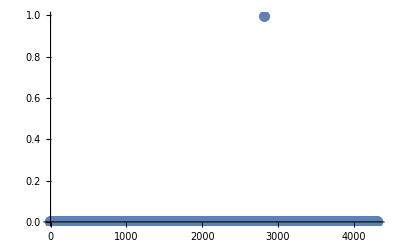

```mathematica
ListPlot[smlayer[llayerEnd[beforeLinear]],PlotRange->All,PlotStyle->PointSize[0.02]]
```

All values are essentially 0 besides one of them that takes value ~1. The latter is the probability for the “lion” class.

#### Implementation of Wolfram ImageIdentify Net V1 (only if interested):

* If you want to see more details on how this network is fully coded, please refer to the following notebook (not necessary for this course!):

```mathematica
NetModel["Wolfram ImageIdentify Net V1", "ConstructionNotebook"]
```

za853_shm19FrontEndObject[LinkObject["za853_shm", 3, 1]]19Untitled-1

### Net surgery for classification of mountain and beach images using Wolfram ImageIdentify Net V1

We now get mountain and beach landscape images from the web for training and test:

```mathematica
nimages=30;
```

```mathematica
mountain=WebImageSearch["Mountain",MaxItems->nimages];
```

```mathematica
beach=WebImageSearch["Beach",MaxItems->nimages];
```

```mathematica
ntraining=20;
```

```mathematica
trainingset=Join[Table[mountain[[i]]-> "mountain",{i,1,ntraining}],Table[beach[[i]]-> "beach",{i,1,ntraining}]];
```

```mathematica
testset=Join[Table[mountain[[i]]-> "mountain",{i,ntraining+1,nimages}],Table[beach[[i]]-> "beach",{i,ntraining+1,nimages}]];
```

The net model would predict the following for the test set:

```mathematica
Keys[testset]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
net[Keys[testset]]
```

{ridge,ridge,mount,mount,mount,mount,lake,valley,mount,mount,coast,snowfield,beach,beach,isle,beach,beach,coast,beach,beach}

It gives many possible classes. In contrast, we only want mountain and beach classes. We need to modify this model and re-train it to achieve what we want.

#### Modify the pre-built model to deal with our mountain/beach problem

We will basically modify the net at the final part where the probabilities of a certain object are calculated. 

More specifically, we drop the last two layers:

```mathematica
changedNet=NetDrop[net,-2]
```

NetChain[<>]

We now add a LinearLayer that will act as a classifier and a SoftmaxLayer to convert the result to probabilities.

Crucially, we specify in the Output that we want a decoder to 2 classes (mountain and beach) instead of the 4315 classes considered by Wolfram ImageIdentify Net V1:

```mathematica
newNet=NetJoin[changedNet,NetChain[Association["classifier"->LinearLayer[],"probabilities"->SoftmaxLayer[]],"Output"->NetDecoder[{"Class",{"mountain","beach"}}]]]
```

NetChain[<>]

Note that the newly added SoftmaxLayer and LinearLayer layers inherit the dimensionality from the number of classes specified in the input.

Train new net on training data:

,LearningRateMultipliers→{“classifier”→1,_→0}

```mathematica
trainedNet=NetTrain[newNet,trainingset]
```

NetChain[<>]

```mathematica
Keys[testset]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
trainedNet[Keys[testset]]
```

{mountain,beach,mountain,mountain,mountain,mountain,mountain,mountain,mountain,mountain,beach,beach,beach,beach,beach,beach,beach,beach,beach,beach}

Despite the fact that the training set was small, it does quite well (the number of classes is also small and this probably helps...):

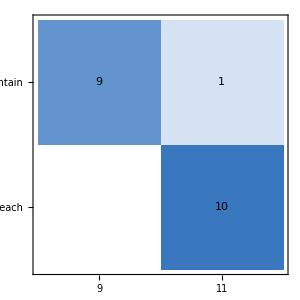
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[trainedNet,testset,"ConfusionMatrixPlot"]
```

```mathematica
N[(8+10)/20]
```

0.9

0.9